◼ "\◼ "2023-12-06v5 .32M. J. Steil[msteil@theorie.ikp.physik.tu-darmstadt.de](mailto:msteil@theorie.ikp.physik.tu-darmstadt.de)TU Darmstadt

# Field space and FRG flow equations

Martin Jakob Steil^1

^1Technische Universität Darmstadt

Evaluating the notebook (with all currently enabled cells) should take around 4 seconds.

Initialization

```mathematica
Clear["Global`*"]
SetDirectory[NotebookDirectory[]];
$DistributedContexts={};
(* Disable Notebookhistory, [https://mathematica.stackexchange.com/questions/11258/are-there-suitable-versioning-systems-for-mathematica-notebooks]*)
SetOptions[EvaluationNotebook[],PrivateNotebookOptions->{"FileOutlineCache"->False},System`TrackCellChangeTimes->False]

(* Display the Timing of an Evaluation in a Notebook Window [https://reference.wolfram.com/language/howto/DisplayTheTimingOfAnEvaluationInANotebookWindow.html] *)
SetOptions[EvaluationNotebook[],EvaluationCompletionAction->{"ShowTiming"}]
```

(** AutoSaveEvaluationNotebook using $Pre **)
Needs["AutoSaveEvaluationNotebook`","D:/Github/Mathematica/Packages/AutoSaveEvaluationNotebook/AutoSaveEvaluationNotebook.m"];
SetOptions[AutoSaveEvaluationNotebook,"minBackupInterval"->Quantity[30,"Minutes"]];
EnableAutoSaveEvaluationNotebookPreRead[];

(** Update embedded Stylesheet **)
Needs["StylesheetTools`","D:/Github/Mathematica/Packages/StylesheetTools/StylesheetTools.m"];
style=GetStyleDefinitions[];
files=FileNames["D:\Desktop\PhD-Thesis\appendix\*.nb"];
SetStyleDefinitions[files,style];

### Packages

```mathematica
(** Own packages: [https://raw.githubusercontent.com/MJSteil/Mathematica/master/] **)

(* Provides RGBfromCMYK colors form the corporate design of Goethe university. Use GUCD`showAll[] to see all colors. *)
GUCD`mode="RGBfromCMYK";
Get["D:/Github/Mathematica/Packages/CorporateDesigns/GUCD.m"]; 

(* Provides RGB or CMYK (if TUDaCD`TUDaCDuseCMYK=True) colors form the corporate design of Technische Universität Darmstadt.Use TUDaCD`showAll[] to see all colors. *)
TUDaCD`useCMYK=False;
Get["D:/Github/Mathematica/Packages/CorporateDesigns/TUDaCD.m"];
```

```mathematica
(** Notation Package: provides InfixNotation and more **)
Notation`AutoLoadNotationPalette=False;(* AutoLoadNotationPalette specifies whether the Notation palette is opened when the Notation Package is loaded. *)
Needs["Notation`"];

(* Open NotationPalette [in parts from Notation.m]*)
Notation`OpenNotationPalette[]:=Module[{
	nb = InputNotebook[], 
	filePath = $TopDirectory<>"\\AddOns\\Packages\\Notation\\LocalPalettes\\"<>$Language<>"\\NotationPalette.nb" (* This file can also be added in the "Palettes" menue. *)
	},
    If[$Linked,
    	NotebookPut[Get[filePath]],
    	NotebookOpen[filePath]
    ]; 
    SetSelectedNotebook[nb];
]
```

```mathematica
(** LaTeX **)
Needs["TeXUtilities`"]
ParallelNeeds["TeXUtilities`"] (* https://github.com/jkuczm/MathematicaTeXUtilities *)
```

### Tagged Methods

(** Update tagged methods **)
Needs["UpdateTaggedMethod`","D:/Github/Mathematica/Packages/UpdateTaggedMethod/UpdateTaggedMethod.m"];
UpdateTaggedMethods["D:/Github/Mathematica/tagged_methods.nb"]

#### Notebook/Frontend IO

```mathematica
(* SaveToCell | v2.0 | Save assigned value of symbol(s) to cell(s) | Modified Version of [http://szhorvat.net/pelican/save-data-in-notebooks.html] *)
ClearAll[SaveToCell];
SaveToCell[names_/;VectorQ[names,StringQ],suffix:Except[_?OptionQ]:"",comment:Except[_?OptionQ]:"",opt:OptionsPattern[]]:=Module[{
	data=Symbol[#]&/@names,
	label=Row[Flatten@{If[comment=!="",{Style[comment,Plain],", "},Nothing],DateString["ISODateTime"]}]
	},
	CellPrint@Cell[
		BoxData@MapThread[RowBox[{#2<>suffix,"=",ToBoxes[Iconize[#1,label,Method->Compress]],";"}]&,{data,names}],
		"Input",
		GeneratedCell->False,(*prevent deletion by Cell>Delete All Output:*)
		CellLabel->"(saved)",
		CellLabelAutoDelete->False,
		opt
	]
]

SetAttributes[SaveToCell,HoldFirst]
SaveToCell[var_,name:Except[_?OptionQ]:"",comment:Except[_?OptionQ]:"",opt:OptionsPattern[]]:=With[{
	data=Evaluate[var],
	label=Row[Flatten@{If[comment=!="",{Style[comment,Plain],", "},Nothing],DateString["ISODateTime"]}]
	},
	CellPrint@Cell[
		BoxData@RowBox[{If[name=!="",name,MakeBoxes[var]],"=",ToBoxes[Iconize[data,label,Method->Compress]],";"}],
		"Input",
		GeneratedCell->False,(*prevent deletion by Cell>Delete All Output:*)
		CellLabel->"(saved)",
		CellLabelAutoDelete->False,
		opt
	]
]
SaveToCell::usage="SaveToCell[var_,name:Except[_?OptionQ]:\"\",comment:Except[_?OptionQ]:\"\",opt:OptionsPattern[]]: saves the assignment of var/or the data in\
 var (under name if name=!=\"\") in a compressed iconized form with a label including comment and a time stamp.\n\
SaveToCell[names_/;VectorQ[names,StringQ],suffix_:Except[_?OptionQ]:\"\",comment:Except[_?OptionQ]:\"\",opt:OptionsPattern[]]: saves the assignments behind the elements of names in\
 in a compressed iconized form with suffix appended to the symbol names and a label including comment and a time stamp.";
```

```mathematica
(* AutoCollapse | v2.0 | Close CellGroup | [https://mathematica.stackexchange.com/a/683] *)
AutoCollapse[]:=Module[{},
	If[$FrontEnd=!=$Failed,
		SelectionMove[EvaluationNotebook[],All,GeneratedCell];
		FrontEndTokenExecute["SelectionCloseUnselectedCells"]
	];
]
AutoCollapse::usage="Collapse input cells by grouping them with the generated output cells.";
```

```mathematica
(* CellPrintDisplayFormulaNumbered | v2.3 | CellPrint a DisplayFormulaNumbered *)
ClearAll[CellPrintDisplayFormulaNumbered,CellPrintDisplayFormulaNumberedNAC];
CellPrintDisplayFormulaNumbered[exp_,tag_:None,comment_:"",generatedCellQ_:False,groupQ_:True,autoCollapseQ_:True]:=Module[{frameLabels,box},
	frameLabels=CellFrameLabels->{
		{None,Cell[TextData[{If[tag===None,"",ToString[tag]<>" "]<>"(",CounterBox["Chapter"],".",CounterBox["DisplayFormulaNumbered"],")"}],"DisplayFormulaEquationNumber"]},
		{None,None}
	};
	box=BoxData[RowBox[{ToBoxes[exp],RowBox[{comment}]}]];
	CellPrint[Cell[box,"DisplayFormulaNumberedPrinted",frameLabels,
		GeneratedCell->generatedCellQ,CellAutoOverwrite->True,ShowStringCharacters->False,CellGroupingRules->If[groupQ,"OutputGrouping",Inherited]]
	];
	If[autoCollapseQ,AutoCollapse[]];
]
CellPrintDisplayFormulaNumbered::usage="CellPrintDisplayFormulaNumbered[exp_,tag_:None,comment_:\"\",generatedCellQ_:False,groupQ_:True,autoCollapseQ_:True]:\
CellPrint exp to a DisplayFormulaNumberedPrinted output cell.";
CellPrintDisplayFormulaNumberedNAC[exp_,tag_:None,comment_:"",generatedCellQ_:False,groupQ_:True,autoCollapseQ_:False]:=CellPrintDisplayFormulaNumbered[exp,tag,comment,generatedCellQ,groupQ,autoCollapseQ]
CellPrintDisplayFormulaNumberedNAC::usage="Same as CellPrintDisplayFormulaNumbered[] but autoCollapseQ defaults to false.";
```

```mathematica
(* CellPrintTaggedMethodCell | v1.0 | CellPrint an Initialization Code Cell for a TaggedMethod *)
ClearAll[CellPrintTaggedMethodCell]
CellPrintTaggedMethodCell[name_String,version_:"1.0",description_:""]:=CellPrint[
	Cell[BoxData[RowBox[{"(* "<>name<>" | v"<>version<> " | "<>description<>" *)"}]],
	"Code",InitializationCell->True,CellTags->name]
]
CellPrintTaggedMethodCell::usage="CellPrintTaggedMethodCell[name_String,version_:\"1.0\",description_:\"\"]:\
CellPrint an Initialization Code Cell for a TaggedMethod with a given name (and versionand description).";
```

```mathematica
(* ToInterpretationBox | v1.0 | Generate an InterpretationBox *)
ToInterpretationBox[raw_][formatted_]:=With[{box=ToBoxes[formatted]},InterpretationBox[RowBox[{box}],raw]]
ToInterpretationBox::usage="ToInterpretationBox[raw_][formatted_]: Generate an InterpretationBox displaying formatted  using `ToBoxes[formatted]` while beeing\
interpreted as raw. Very usefull when setting custom Formats.";
ToInterpretationBox//SetReadProtected;
```

#### Notebook Style

```mathematica
(* NotebookHeaderUpdate | v1.1 | Update ISODateTime in NotebookHeader *)
ClearAll[NotebookHeaderUpdate];
NotebookHeaderUpdate[rule_:{}]:=Module[{header,separator},
	separator="\\[FilledSmallSquare] ";
	NotebookLocate["NB`Header"];
	(*https://mathematica.stackexchange.com/a/1411/42436*)
	header=First[FrontEndExecute[FrontEnd`ExportPacket[NotebookSelection[EvaluationNotebook[]],"PlainText"]]];
	header=StringSplit[header,separator];
	header[[1]]=StringDrop[DateString["ISODateTime"], -3];
	header=header//.rule/.{str_String/;StringContainsQ[str,"@"]:>TemplateBox[{str,"mailto:"<>str},"HyperlinkURL"]};
	header=BoxData[TemplateBox[Flatten@{"◼ ", "\"\\\◼ \"",header},"RowWithSeparators"]];
	NotebookWrite[EvaluationNotebook[],Cell[
		header,
		"NotebookHeader",
		CellTags->{"NB`Header"},
		FontFamily->"Source Sans Pro",
		FontSize->14,
		FontWeight->"Normal",
		FontSlant->"Plain"
	]]
]
NotebookHeaderUpdate::usage="NotebookHeaderUpdate[]: Update NotebookHeader using `rule` and update the ISODateTime.";
```

```mathematica
(* SetupPrintStyle | v1.0 | Setup style for notebook printout *)
SetupPrintStyle[]:=Module[{header},
	NotebookLocate["NB`Header"];
	(*https://mathematica.stackexchange.com/a/1411/42436*)
	header=First[FrontEndExecute[FrontEnd`ExportPacket[NotebookSelection[EvaluationNotebook[]],"PlainText"]]];
	
	SetOptions[EvaluationNotebook[],
		PageFooters->{
			{Cell[TextData[StyleBox[NotebookFileName[],"FooterText"]],"Header",CellMargins->{{0,Inherited},{Inherited,Inherited}}],
			None,
			Cell[TextData[StyleBox[header,"FooterText"]],"Header",CellMargins->{{0,Inherited},{Inherited,Inherited}}]},
			{Cell[TextData[StyleBox[NotebookFileName[],"FooterText"]],"Header",CellMargins->{{0,Inherited},{Inherited,Inherited}}],
			None,
			Cell[TextData[StyleBox[header,"FooterText"]],"Header",CellMargins->{{0,Inherited},{Inherited,Inherited}}]}
		},
		
		PageHeaderLines->{False,False},
		PageHeaders->{
			{Cell[
				TextData[{StyleBox[CounterBox["Page"],"PageNumber"],StyleBox["/","PageNumber"],StyleBox[CounterBox["LastPage",CounterFunction:>Identity],"PageNumber"]}],
				"Header",CellMargins->{{0,Inherited},{Inherited,Inherited}}
			],None,None},
			{Cell[
				TextData[{StyleBox[CounterBox["Page"],"PageNumber"],StyleBox["/","PageNumber"],StyleBox[CounterBox["LastPage",CounterFunction:>Identity],"PageNumber"]}],
				"Header",CellMargins->{{0,Inherited},{Inherited,Inherited}}
			],None,None}
		},
		
		PrintAction->"PrintToNotebook",
		PrintingCopies->1,
		PrintingOptions->{
			"FacingPages"->True,
			"FirstPageFace"->Right,
			"FirstPageFooter"->True,
			"FirstPageHeader"->True,
			"PageSize"->{595.32,841.92},
			"PaperOrientation"->"Portrait",
			"PaperSize"->{595.32,841.92},
			"PrintingMargins"->{{28.3465,28.3465},{50,50}}
		},
		PrintingStyleEnvironment->"Printout",
	
		ShowSyntaxStyles -> True
	]
]
```

#### Parallelization

```mathematica
(* UniqueParallel | v1.0 | Creates a unique identifier across kernels *)
ClearAll[UniqueParallel]
UniqueParallel[]:=Symbol[ToString[Unique[]]<>"$"<>ToString[$KernelID]]
UniqueParallel::usage="UniqueParallel[] creates a unique identifier across kernels using 'Symbol[ToString[Unique[]]<>\"$\"<>ToString[$KernelID]]'.";
```

```mathematica
(* EvaluateAll | v1.0 |  Wrapper to switch between Evaluate and *)
ClearAll[EvaluateAll]
SetAttributes[EvaluateAll,{HoldFirst,SequenceHold}]
EvaluateAll//Options={"parallelQ"->True};
EvaluateAll[exp_]/;OptionValue[EvaluateAll,"parallelQ"]:=ParallelEvaluate[exp]
EvaluateAll[exp_]:=Evaluate[exp]
EvaluateAll::usage="EvaluateAll[exp] evaluates the expression exp using ParallelEvaluate if OptionValue[EvaluateAll,\"parallelQ\"]\
 else Evaluate is used for evaluation.";
```

```mathematica
(* ContextQ | v1.0 | Return True if name is a context *)
ClearAll[ContextQ];
ContextQ[name_]:=If[Length[Names[ToString[name]<>"`*"]]==0,False,True]
ContextQ::usage="ContextQ[name_]: Return True if name is a context (has sub expressions 'name`...').";
```

```mathematica
(* GetSubContexts | v1.0 | Extract possible sub contexts 'name`*`...'  *)
ClearAll[GetSubContexts];
Options[GetSubContexts]={
	Depth->10
};
GetSubContexts[name_]:=Block[{names=((ToString[name]<>#)&/@Array[StringJoin@@ConstantArray["`*",#]&,LookupOption[GetSubContexts,Depth,10]])},
	StringReplace[Flatten[Names[#]&/@names],RegularExpression["(.*)`(.*[^`])"]->"$1`"]//DeleteDuplicates
]
GetSubContexts::usage="GetSubContexts[name_]: Extract possible sub contexts 'name`*`...' and return '{}' if name is not a context.";
```

```mathematica
(* GetDistributedContexts | v1.0 | Return $DistributedContexts *)
ClearAll[GetDistributedContexts];
GetDistributedContexts[]:=If[ListQ[$DistributedContexts]=!=True,{$Context},$DistributedContexts]
GetDistributedContexts::usage="GetDistributedContexts[]: Return $DistributedContexts if $DistributedContexts is a list and {$Context} if its not a list.";
```

```mathematica
(* AddToDistributedContexts | v1.0 | Add name(s) to $DistributedContexts *)
ClearAll[AddToDistributedContexts];
AddToDistributedContexts[name_String/;StringMatchQ[name,RegularExpression["(.*)`"]]]:=With[
	{contexts=DeleteDuplicates@Join[{},GetDistributedContexts[],{name}]},
	$DistributedContexts=contexts;Return[contexts]
]
AddToDistributedContexts[names_/;VectorQ[names,If[StringQ[#],StringMatchQ[#,RegularExpression["(.*)`"]],False]&]]:=With[
	{contexts=DeleteDuplicates@Join[{},GetDistributedContexts[],names]},
	$DistributedContexts=contexts;Return[contexts]
]

AddToDistributedContexts[names_List,includeSubContexts_:True]:=AddToDistributedContexts[#,includeSubContexts]&/@names;
AddToDistributedContexts[name_,includeSubContexts_:True]:=With[{
	contexts=If[includeSubContexts,GetSubContexts[name],If[ContextQ[name],{name},{}]]
},
	
	$DistributedContexts=Join[GetDistributedContexts[],contexts]//DeleteDuplicates;	
	Return[contexts]
]
AddToDistributedContexts::usage="AddToDistributedContexts[name_,OptionsPattern[],includeSubContexts_:True]:\
Add name to $DistributedContexts if name is a context and include sub contexts if includeSubContexts=True using GetSubContexts[...].";
```

#### Type checks

```mathematica
(* RuleQ | v1.0 |  *)
RuleQ[x_]:=VectorQ[x,MemberQ[{Rule,RuleDelayed},Head[#]]&]||MemberQ[{Rule,RuleDelayed},Head[x]]
RuleQ::usage="RuleQ[x_]: False except iff x is a list or a single element of Head Rule or RuleDelayed.";
```

```mathematica
(* NonNegativeIntegerQ | v1.0 |  *)
NonNegativeIntegerQ[x_]:=Element[x,NonNegativeIntegers]&&UnsameQ[Head[x],List]
NonNegativeIntegerQ::usage="NonNegativeIntegerQ[x_]: False except iff x is a single non negative integer.";
```

```mathematica
(* PositiveIntegerQ | v1.0 |  *)
PositiveIntegerQ[x_]:=NonNegativeIntegerQ[x]&&x>0
PositiveIntegerQ::usage="PositiveIntegerQ[x_]: False except iff x is a single positive integer.";
```

#### Options, Attributes, Information and VerificationTest

```mathematica
(* LookupOption | v1.0 |  Lookup the option value 'option' *)
LookupOption[x_,option_]:=Lookup[Options[If[Head[x]=!=Symbol,Head[x],x]],option]
LookupOption[x_,option_,default_]:=Lookup[Options[If[Head[x]=!=Symbol,Head[x],x]],option,default]

LookupOption::usage="LookupOption[x_,option_String]: Lookup the option value 'option' in the options attached to x or its head (if Head[x]===Symbol).\n\
LookupOption[x_,option_String,default_]: Use the value default if 'option' is not found attached to x.";
```

```mathematica
(* SetReadProtected | v1.0 |  Add ReadProtected to Attributes[exp] *)
SetReadProtected[exp_]:=With[{att=DeleteDuplicates[Attributes[exp]~Join~{ReadProtected}]},SetAttributes[exp,att]]
SetReadProtected::usage="SetReadProtected[exp_]: If not already set add ReadProtected to Attributes[exp].";
```

```mathematica
(* PrintDefinitions | v1.0 |  Wrapper for GeneralUtilities`PrintDefinitions[args] *)
PrintDefinitions[args___]:=GeneralUtilities`PrintDefinitions[args]
PrintDefinitions::usage="PrintDefinitions[args___]:=GeneralUtilities`PrintDefinitions[args]";
```

```mathematica
(* ShowProperties | v1.1 | List all AnnotationKeys and Properties *)
ClearAll[ShowProperties];
ShowProperties[exp_]:=Module[{annotations,properties},
	annotations=AnnotationKeys->Quiet[Check[exp//AnnotationKeys,{}]];
	properties=Properties->Quiet[Check[exp["Properties"],{}]];
	{annotations,properties}
]
ShowProperties::usage="ShowProperties[exp_]: List all AnnotationKeys and Properties of `exp`.";
```

```mathematica
(* ToVerificationTest | v1.0 | Generate a VerificationTest *)
ClearAll[ToVerificationTest];
ToVerificationTest[list_List]:=ToVerificationTest/@list
ToVerificationTest[{exp_Hold,res_,label_String:""}]:=VerificationTest[ReleaseHold@exp,res,TestID->label]
ToVerificationTest[{exp_Hold,res_,label_Style:Style[""]}]:=VerificationTest[ReleaseHold@exp,res,TestID->label]
ToVerificationTest::usage::"ToVerificationTest[{exp_Hold,res_,label_String:""}]: Generate a VerificationTest for 'exp' with the expected result 'res'.";
```

#### DebugPrint and Timing

```mathematica
(* DebugPrint | v1.0 |  Flexible DebugPrint Method *)
Through[{ClearAll,SetReadProtected}[DebugPrint]];
Options[DebugPrint]={
	"LastTime"->0,
	"MessageCount"->0,
	"MessageLimit"->20,
	"MessageLimitTime"->1
};

DebugPrint[][exp___]:=DebugPrint[True,{}][exp]
DebugPrint[printQ_][exp__]:=DebugPrint[printQ,{}][exp]
DebugPrint[printQ_,style_][exp__]/;BooleanQ[printQ]:=DebugPrint[printQ,style][{exp}]
DebugPrint[printQ_,style_][]:=Module[{},0;]

DebugPrint[printQ_,style_][exp_List]/;BooleanQ[printQ]:=Module[{},If[printQ,
	With[{
		t=AbsoluteTime[],
		Δt=AbsoluteTime[]-OptionValue[DebugPrint,"LastTime"],
		T=OptionValue[DebugPrint,"MessageLimitTime"],
		n=OptionValue[DebugPrint,"MessageLimit"]
	},
		If[Δt>T,
			SetOptions[DebugPrint,"MessageCount"->0](* Reset DebugPrint Option "MessageCount" *)
		];
		SetOptions[DebugPrint,"LastTime"->t,"MessageCount"->OptionValue[DebugPrint,"MessageCount"]+1];(* Iterate DebugPrint Options "LastTime" and "MessageCount" *)
	
		If[OptionValue[DebugPrint,"MessageCount"]>n,
			If[!ChoiceDialog["Warning: MessageLimit ("<>ToString[n]<>") in MessageLimitTime ("<>ToString[T]<>" s) reached!",
					{"Continue Evaluation"->True,"Abort Evaluation"->False},WindowTitle->"DebugPrint Warning"
				],
				SetOptions[DebugPrint,"MessageCount"->0];
				Abort[];
			];
		];
		Print[Style[Row[exp~Join~{" in Δt= ",If[Δt>10^9,0,Δt]}," "],style]]
	];
]];
DebugPrint[printQ_,style___][exp__]:=DebugPrint[LookupOption[printQ,"DebugPrint",False],style][{printQ,": ",exp}]
DebugPrint[printQ_,style___][]:=Module[{},0;]

DebugPrint::usage="DebugPrint[printQ_:True,style_:{}][exp_]: If printQ==True Print[Style[exp,style]]\n\
DebugPrint[printQ_:True,style_:{}][exp_List]: If printQ==True Print[Style[Row[exp,\" \"],style]]\n\
For non boolean arguments for printQ LookupOption[printQ,\"DebugPrint\",False] is used to generate an bool\
and falling back to the two boolean versions of the function.";

(* Enable Printing for given symbol(s) *)
Through[{ClearAll,SetReadProtected}[DebugPrintOn]];
DebugPrintOn[head__]:=Module[{},DebugPrintOn/@{head};]
DebugPrintOn[head_List]:=Module[{},DebugPrintOn/@head;]
DebugPrintOn[head_]:=If[MissingQ[LookupOption[head,"DebugPrint"]],
	Options[head]=Append[Options[head],"DebugPrint"->True];,
	SetOptions[head,"DebugPrint"->True];
]
DebugPrintOn::usage="DebugPrintOn[head_]: Set or if necessary add \"DebugPrint\"->True to Options[head].\
If head is a list or has multiple arguments (head__) apply DebugPrintOn on eacht element of head.";

(* Disable Printing for given symbol(s) *)
Through[{ClearAll,SetReadProtected}[DebugPrintOff]];
DebugPrintOff[head__]:=Module[{},DebugPrintOff/@{head};]
DebugPrintOff[head_List]:=Module[{},DebugPrintOff/@head;]
DebugPrintOff[head_]:=If[!MissingQ[LookupOption[head,"DebugPrint"]],
	SetOptions[head,"DebugPrint"->False];
]
DebugPrintOff::usage="Set \"DebugPrint\"->False in Options[head] iff \"DebugPrint\" is in Options[head].\
If head is a list or has multiple arguments (head__) apply DebugPrintOn on eacht element of head.";
```

```mathematica
(* AbsoluteTimer | v1.0 |  *)
Options[AbsoluteTimer]={"t"->0};
AbsoluteTimer[]:=OptionValue[AbsoluteTimer,"t"]
StartAbsoluteTimer[]:=With[{},Options[AbsoluteTimer]={"t"->-AbsoluteTime[]};]
StopAbsoluteTimer[]:=With[{t=OptionValue[AbsoluteTimer,"t"]},Options[AbsoluteTimer]={"t"->t+AbsoluteTime[]};AbsoluteTimer[]]

StartAbsoluteTimer[];
```

### Notebook Specific Methods

#### Replace and Rules

```mathematica
(** Replacements **)
ClearAll[ReplaceAllTwoWay]
ReplaceAllTwoWay[x_,rule_TwoWayRule]:=With[{temp=Unique[]},
	ReleaseHold@Fold[ReplaceAll,Hold[x],{rule[[1]]->temp,rule[[2]]->rule[[1]],temp->rule[[2]]}] (* (((x//.rule[[1]]->temp)//.rule[[2]]->rule[[1]])//.temp->rule[[2]]) *)
]
ReplaceAllTwoWay[x_,rules_/;VectorQ[rules,Head[#]===TwoWayRule&]]:=Fold[ReplaceAllTwoWay,x,rules]
ReplaceAllTwoWay::usage="ReplaceAllTwoWay[x_,rule_TwoWayRule]: Swap elements in x using the TwoWayRule rule (e.g. a↔b).
ReplaceAllTwoWay[x_,list_List]: Folds the elements of list onto x and using ReplaceAllTwoWay[...] in order to apply multiple TwoWayRules.";

ClearAll[ReplaceRepeatedOnLevel]
ReplaceRepeatedOnLevel[exp_,rules_,level_:{0},maxIterations_:100]/;RuleQ[rules]&&NonNegativeIntegerQ[maxIterations]:=Module[{i,a,b},
	a=exp;
	b=exp;
	For[i=0,i<maxIterations,i++,
		b=Fold[Replace[#1,#2,level]&,a,Flatten[{rules}]];
		If[SameQ[a,b],Break[]];
		a=b;
	];
	b
]
ReplaceRepeatedOnLevel::usage="ReplaceRepeatedOnLevel[exp_,rules_,level_:{0},maxIterations_:10]:\
exp=Fold[Replace[#1,#2,level]&,exp,Flatten[{rules}]] until exp stops changing or maxIterations tries are reached.";

ClearAll[ReplaceBasedOn]
ReplaceBasedOn[exp_,rules_List/;RuleQ[rules],crit_:LeafCount,process_:Expand]:=Module[{gatheredRules,r,res},
	gatheredRules=GatherBy[rules,First];
	res=exp;
	Do[
		res=First@SortBy[Map[ReplaceBasedOn[res,#,crit,process]&,r],{crit}],
	{r,gatheredRules}];
	Return[res]
]


ReplaceBasedOn[exp_,rule_Rule|rule_RuleDelayed,crit_:LeafCount,process_:Expand]:=Module[{exp0,exp1,exp0LC,exp1LC},
	exp0=process[exp];
	exp1=process[exp0/.rule];
	exp0LC=crit[exp0];
	exp1LC=crit[exp1];
	DebugPrint[ReplaceBasedOn]["Using: ",rule," | ",exp0," with "<>ToString[crit]<>"=",exp0LC, " vs ",exp1," with "<>ToString[crit]<>"=",exp1LC];
	If[exp1LC<=exp0LC,		
		Return[exp1];
	];
	Return[exp];
]
ReplaceBasedOn::usage="ReplaceBasedOn[exp_,rule_Rule|rule_RuleDelayed,crit_:LeafCount,process_:Expand]: Return process[exp/.rule] only if the result is smaller based on crit.\n\
ReplaceBasedOn[exp_,rules_List/;RuleQ[rules],crit_:LeafCount,process_:Expand]: Gather the rules by their LHS and choose the best result of ReplaceBasedOn[...] according to crit for each LHS.";
```

#### Associations and Lists

```mathematica
(** Methods related to List **)
(* List and Association *)
ClearAll[ListToAssociation];
ListToAssociation[list_List,rule_Rule:(({k1_,k2__}->v1_):>Sequence@@(Rule[#,v1]&/@{k1,k2}))]:=Association[list//.rule]
ListToAssociation::usage = "ListToAssociation[list_List,rule_Rule:(({k1_,k2__}→v1_):>Sequence@@(Rule[#,v1]&/@{k1,k2}))] converts a List to an Association using the Rule r on the list elements.\
 The default rule flattens out Key lists {k1,k2,...}→v1 ⇒ k1→v1,k2→v1,...\n This method with its default rule is usefull to create associations where multiple keys point to the same value.";

(* Postion lookup *)
ClearAll[FirstPositionNonSameQ,LastPositionNonSameQ]; 
FirstPositionNonSameQ[list_List]:=Block[{k},For[k=1,k<Length[list],k++,If[list[[k]]=!=list[[k+1]],Break[]];];k]
LastPositionNonSameQ[list_List]:=Block[{k},For[k=Length[list],k>1,k--,If[list[[k]]=!=list[[k-1]],Break[]];];k]

(* Split random shuffeled list/sum into n sublists of almost equal length *)
ClearAll[SplitRandomSample];
SplitRandomSample[list_List,n_]:=With[{rList=RandomSample[list],r=QuotientRemainder[Length[list],n][[2]]},
	Block[{res=Partition[rList,Floor[Length[rList]/n]],i},
		If[r>0,
			Do[
				res[[i]]=res[[i]]~Join~{rList[[-i]]};
			,{i,Range[r]}]
		];
		Return[res];
	];
]
SplitRandomSample[plus_Plus,n_]:=Total/@SplitRandomSample[List@@plus,n]
SplitRandomSample::usage="SplitRandomSample[list_List,n_]: Split random shuffeled list into n sublists of (almost) equal length.";

(** Methods related to Association **)
(* SummaryBox wrapper *)
ClearAll[AssociationSummaryBox];
AssociationSummaryBox[asoc_][args___]:=asoc[args];
AssociationSummaryBox/:f_[AssociationSummaryBox[asoc_],args___]/;f=!=StandardForm:=f[asoc,args]
AssociationSummaryBox/:MakeBoxes[AssociationSummaryBox[asoc_Association],StandardForm]/;BoxForm`UseIcons:=ToBoxes@Block[{nK,nV,Kn},
	nK=BoxForm`MakeSummaryItem[{"Number of Keys: ",Style[asoc//Keys//Length]},StandardForm];
	nV=BoxForm`MakeSummaryItem[{"Total number of Values: ",Style[asoc//Values//Flatten//Length]},StandardForm];
	Kn=BoxForm`MakeSummaryItem[{"",Style[Multicolumn[#->Skeleton@Length@asoc[#]&/@Keys[asoc],Floor[Sqrt[asoc//Keys//Length]]],Small]},StandardForm];
	
	(* [https://mathematica.stackexchange.com/a/99914] *)
	(* [https://mathematica.stackexchange.com/a/79891] *)
	RawBoxes[BoxForm`ArrangeSummaryBox[Association,
			Evaluate@asoc,
			None,
			{nK,nV},
			{Kn},
			StandardForm,
			"Interpretable"->True
	]]
]
AssociationSummaryBox::usage="AssociationSummaryBox[asoc_Association]: Wraps asoc affecting only the StandartForm output which is given by a summary box.";

ClearAll[AssociationSummary];
AssociationSummary[asoc_Association]:={
	asoc//Values//Flatten//Length,
	#->Skeleton@Length@asoc[#]&/@Keys[asoc]//Multicolumn,
	asoc//Keys//Length
}
AssociationSummary::usage="AssociationSummary[asoc_Association]: compute a summary of the dimensions of the Association";

ClearAll[AssociationLengthDifferences];
AssociationLengthDifferences[asoc1_Association,asoc2_Association]/;Keys[asoc1]===Keys[asoc2]:={
	Row[{#1-#2,##},","]&@@Map[(#//Values//Flatten//Length)&,{asoc1,asoc2}],
	#->{Length[asoc1[#]]-Length[asoc2[#]],Length[asoc1[#]],Length[asoc2[#]]}&/@Keys[asoc1]//Multicolumn,
	Row[{#1-#2,##},","]&@@Map[(#//Values//Flatten//Length)&,{asoc1,asoc2}]
}
AssociationPrintLengthDifferences::usage="AssociationLengthDifferences[asoc1_Association,asoc2_Association]/;Keys[asoc1]===Keys[asoc2]: compute differences in Value Lengths.";
```

### Variables

```mathematica
AddToDistributedContexts[{"Global`","TeXUtilities`"}];
StartupContexts=Contexts[];
```

```mathematica
(* Spacing Strings *)
NegativeThickSpaceString="";
NegativeMediumSpaceString="";
NegativeThinSpaceString="";
NegativeVeryThinSpaceString="";

VeryThinSpaceString="";
ThinSpaceString=" ";
MediumSpaceString=" ";
ThickSpaceSting=" ";

SpaceStrings={"\<\"\"\>","\<\"\"\>","\<\"\"\>","\<\"\"\>","\<\"\"\>","\<\" \"\>","\<\" \"\>","\<\" \"\>"};
```

(* [https://mathematica.stackexchange.com/a/91913] *)
NamedCharactersToStringsRules=(#[[1]]→StringTake[#[[2]],{4,-3}])&/@Select[
	Table[{#,ToString@FullForm@#}&@FromCharacterCode[i],{i,1114111}],StringMatchQ[#[[2]],""\["~~___~~"]""]&
];
NamedCharactersToStringsRules//SaveToCell[#,"NamedCharactersToStringsRules"]&

```mathematica
NamedCharactersToStringsRules=;
```

```mathematica
ToFilename[exp_,hashExp_:None]:=With[{labelString=StringReplace[ToString[exp],NamedCharactersToStringsRules]},
	StringReplace[
		If[labelString=!="None"&&PrintableASCIIQ[labelString],labelString,Hash[If[hashExp===None,exp,hashExp],"Expression","HexString"]],
		{" "->"","[{"->"_","}]"->"_", "]["->"_", "["->"", "]"->"", ","->"", "{"->"", "}"->"","`"->"-"}
	]
]
```

```mathematica
LaTeXSymbol = ;
```

## Basics

## Commutative multiply: CM[...]

Why not use Times[...] for commutative multiplication? 
→ Power[...,n]: Since Times[...] can evaluate to Power[...,n]. Sadly Mathematica can not apply expressions written for Times[...] on positive Integer Power[...,n]. This would make it necessary to implement the following overloaded, recursive functions for Power[...,n] and Times[...].
→ Sorting: There is no obvious way to manipulate the sorting of the elements in Times[...]. For readability of complex expressions a custom sorting is however highly advantageous. 
→ Full control: Times[...] as a core function of Mathematica has a non transparent behavior
→ Using Times[...] for the following applications would require modifications of its default behavior: Modifying protected core functions of Mathematica seems way too dangerous: performance or even functionality could no longer be guaranteed.

 We implement our own commutative multiplication CM[...] with no “simplification” to an integer power method. CM[] uses SortBy[...,{CM`sortLvL[#]&,CM`sortLvL2[#]&,#&}] for ordering.

```mathematica
AddToDistributedContexts[{"CM`","CM`format`"}];
```

### Basics

```mathematica
ClearAll[CM];

Options[CM]={
	"CM`format`compact"->True, (* If true CM[a,b,...] is displayed as ab... *)
	"CM`format`power"->True (* If true a sequence of repeating factors is displayed using a Superscript/Power notation: Eg. CM[...,a,a,...] is displayed 
						as ... a^2... . As a Formating option the expression itself is however not modified as we specificly designed CM to not "simplify" using a Power function.  *)
};

(* Documentation *)
CM::usage="Commutative multiplication using SortBy[...,{CM`sortLvL[#]&,CM`sortLvL2[#]&,#&}] for ordering and no 'simplification' to integer powers.";

(* Default values and OneIdentity *)
CM[]:=1;
Default[CM]:=1
CM[a_]:=a
Attributes[CM]={OneIdentity};

(* 0 as zero *)
CM[a___,0,b___]:=0

(* 1 as identity *)
CM[1,a__]:=CM[a]


(* Flatten out nested CM (CM is associative) *)
CM[a___,CM[b_,b2__],c___]:=CM[a,b,b2,c]

(* Distribute over *)
CM[x___,f_[y1_,y2___],z___]/;MemberQ[{Plus,List,Equal,Rule,RuleDelayed},f]:=f@@Map[CM[x,#,z]&,{y1,y2}]
CM[x___,f_[y1_,y2___],z___]/;MemberQ[{Association},f]:=Map[CM[x,#,z]&,f[y1,y2]]  

(* Flatten out nested Times and Power *)
CM[a___,Times[b1_,b2_],c___]:=CM[a,b1,b2,c]
CM[a___,Power[b_,n_Integer/;n>0],c___]:=CM[a,CM@@ConstantArray[b,n],c]

(* Combine Numeric factors if possible: e.g. CM[2,21]=CM[42] *)
CM[a___,b1_/;NumericQ[b1],b2_/;NumericQ[b2],c___]/;!SameQ[Head[Times[b1,b2]],Times]:=CM[Times[b1,b2],a,c]

(** Upvalues **)

(* Include Times and Power *)
CM/:Times[a_,b_CM]:=CM[a,b]
CM/:Power[a_CM,n_Integer/;n>0]:=CM@@ConstantArray[a,n]

(* Combine under Plus: e.g. CM[2,a,b]+CM[40,a,b] = CM[42,a,b] *)
CM/:Plus[CM[n1_/;NumericQ[n1],x__],CM[n2_/;NumericQ[n2],x__]]/;!SameQ[Head[Plus[n1,n2]],Plus]:=CM[n1+n2,x]
CM/:Plus[CM[x_],CM[n2_/;NumericQ[n2],x_]]/;!SameQ[Head[Plus[1,n2]],Plus]:=CM[1+n2,x]
CM/:Plus[CM[x_,y__],CM[n2_/;NumericQ[n2],x_,y__]]/;!SameQ[Head[Plus[1,n2]],Plus]:=CM[1+n2,x]
```

### Sorting using CM`sort[] and CM`sortLvL(2)[]

```mathematica
ClearAll[CM`sort,CM`sortLvL,CM`sortLvL2];

(** CM`sortLvL **)
CM`sortLvL[a_?NumberQ]:=-1000
CM`sortLvL[a_?NumericQ]:=-999
CM`sortLvL[a_]:=0

CM`sortLvL[Plus[a_,b__]]:=Max[Map[CM`sortLvL,{a,b}]]
CM`sortLvL[Power[a_,n_]]:=CM`sortLvL[a]

(* If a has CM`sortLvL(2)->Integer as option use it *)
CM`sortLvL[a_]:=With[{opts=LookupOption[a,"CM`sortLvL"]}, opts/;(IntegerQ[opts])]

(* If f has a CM`sortLvL(2) use either its Integer value or the supplied function to generate an Integer value *)
CM`sortLvL[f_[a___]]:=Module[{cmlvl},
	cmlvl=LookupOption[f,"CM`sortLvL"];
	If[IntegerQ[cmlvl],
		cmlvl,
		cmlvl[a]
	]/;(!MissingQ[cmlvl])
]

(** CM`sortLvL2 **)
CM`sortLvL2[a_]:=With[{opts=LookupOption[a,"CM`sortLvL2"]}, opts/;(IntegerQ[opts])]

CM`sortLvL2[Power[a_,n_]]:=n

CM`sortLvL2[f_[a___]]:=Module[{cmlvl},
	cmlvl=LookupOption[f,"CM`sortLvL2"];
	If[IntegerQ[cmlvl],
		cmlvl,
		cmlvl[a]
	]/;(!MissingQ[cmlvl])
]
CM`sortLvL2[a_]:=0 

(** CM`sort **)
CM`sort=x↦SortBy[x,{CM`sortLvL[#],CM`sortLvL2[#]}&];
(* Order using CM`sort *)
CM[a_,b__]:=With[{ab=CM`sort[{a,b}]},Return[CM@@ab]/;!SameQ[ab,{a,b}]]
```

Flatten[Names[#<>"*"]&/@$DistributedContexts];
Select[%,!MissingQ[LookupOption[Symbol[#],"CM`sortLvL"]]&];
Select[%,Symbol===Head[Evaluate@Symbol[#]]&];
ToString[Head[Symbol[#]]]&/@Complement[%%,%];
DeleteDuplicates[Join[%%,%]];
{LookupOption[Symbol[#],"CM`sortLvL"],#}&/@%;
SortBy[%,First]//TableForm

### Derived and related functions: CM`pow[...], CM`toTimes[...] and CM`TimesToCM[...]

```mathematica
ClearAll[CM`pow,CM`toTimes,CM`TimesToCM];

(* Derived power using CM (used for input only) *)
CM`pow[x_,n_Integer/;n>0]:=CM@@ConstantArray[x,n]
CM`pow[x_,0]:=1

(* Conversion CM to and from Times *)
CM`toTimes[c_CM]:=Times@@c
CM`toTimes[p_Plus]:=Plus@@Map[CM`toTimes,List@@p]
CM`toTimes[list_List]:=Map[CM`toTimes,list]
CM`toTimes[asoc_Association]:=Map[CM`toTimes,asoc]
CM`toTimes[x___]:=x

CM`TimesToCM[t_Times]:=CM@@t
CM`TimesToCM[p_Plus]:=Plus@@Map[CM`TimesToCM,List@@p]
CM`TimesToCM[list_List]:=Map[CM`TimesToCM,list]
CM`TimesToCM[asoc_Association]:=Map[CM`TimesToCM,asoc]
CM`TimesToCM[x___]:=x
```

### Format and Input

```mathematica
(** Formating **)

ClearAll[CM`format`rule];
CM`format`rule/:MakeBoxes[CM`format`rule[rules_],StandardForm]/;BoxForm`UseIcons:=ToBoxes@Iconize[rules,"CM`format`rule"]
CM`format`rule/:replace_[exp__,CM`format`rule[rule_]]/;MemberQ[{Replace,ReplaceAll,ReplaceRepeated},replace]:=replace[exp,rule]
CM`format`rule::usage="Iconize wrapper for a (formatting) rule/ list of rules.";

CM/:MakeBoxes[CM[a_/;LookupOption[CM,"CM`format`compact",False],b__],StandardForm]/;BoxForm`UseIcons:=ToInterpretationBox[CM[a,b]]@Module[{ab,rules},
	ab = {If[a===-1,"-",a],b};
	rules=Flatten[{DeleteDuplicates[(LookupOption[#,"CM`format`rules",Nothing]&/@ab)]}];
	ab = Fold[ReplaceRepeated,ab,rules];

	If[LookupOption[CM,"CM`format`power",False],
		Row[Power[#[[1]],#[[2]]]&/@({#,Count[ab,#]}&/@DeleteDuplicates[ab]),ThinSpaceString],
		Row[ab,ThinSpaceString]
	]
]
CM/:Format[CM[a_,b__],TeXForm]:=With[{rules=Flatten[{DeleteDuplicates[(LookupOption[#,"CM`format`rules",Nothing]&/@{a,b})]}]},
	TeXVerbatim[If[a===-1,"-",""]<>StringRiffle[(ToString[#,TeXForm]&/@Fold[ReplaceRepeated,{If[a===-1,Nothing,a],b},rules]),{"\\cm{",",","}"}]]
]

(** Notation **)

(* Use ESC * ESC = × as infix input for CM *)
InfixNotation[ParsedBoxWrapper["×"],CM];
```

Examples and Verification Tests

```mathematica
Options[a]={"CM`sortLvL"->2};
Options[b]={"CM`sortLvL"->3,"CM`sortLvL2"->Function[{a},a]};

{b[1],2,b[4],π,b,c,21,c,a};
Row[{"CM[",Row[%,","],"] = ",CM@@%}]//CellPrintDisplayFormula[#,None,", with Options[a]={\"CM`sortLvL\"→2}; Options[b]={\"CM`sortLvL\"→3,\"CM`sortLvL2\"→Function[{a},a]};"]&
```

"CM[",","b[1]2b[4]πbc21ca"] = " " "42πc^2abb[1]b[4], with Options[a]={"CM`sortLvL"→2}; Options[b]={"CM`sortLvL"→3,"CM`sortLvL2"→Function[{a},a]};

```mathematica
VerificationTest[CM[b[1],2,b[4],π,b,c,21,c,a],CM[42,Pi,c,c,a,b,b[1],b[4]],TestID->"Mixed CM"]
ClearAll[a,b]
```

```mathematica
Table[CM[b[1],2,b[4],π,b,c,21,c,a,m],{m,Range[2]}]
ParallelTable[CM[b[1],2,b[4],π,b,c,21,c,a,m],{m,Range[2]}]
```

## Noncommutative multiply: NCM[...]

Why not use NonCommutativeMultiply[...]? 
→ NonCommutativeMultiply[...] has no special feature which would justify using it over our custom implementation.

```mathematica
AddToDistributedContexts[{"NCM`"}];
```

### NCQ: Check if non-commuting

```mathematica
(* Non commutative symbols (all except NumericQ) *)
ClearAll[NCQ]
NCQ[a__]:=NCQ@List[a];
NCQ[a_List]:=NCQ[#]&/@a

(* Check for NCQ Option value {True,False,Function: [a___]->Boolean} *)
NCQ[f_[a___]]:=Module[{ncq},
	ncq=LookupOption[f,"NCQ"];
	If[BooleanQ[ncq],
		ncq,
		ncq[a]
	]/;(!MissingQ[ncq])
]

NCQ[a_]:=LookupOption[a,"NCQ",True] (* Defaults to True *)
NCQ[a_/;NumericQ[a]]:=False; (* Numeric Values are commutative *)
```

### Basics

```mathematica
ClearAll[NCM]

Options[NCM]={
	"NCM`format`compact"->True, (* If true NCM[a,b,...] is displayed as ab... *)
	"NCM`format`power"->True, (* If true a sequence of repeating factors is displayed using a Superscript/Power notation: Eg. NCM[...,a,a,...] is displayed 
						as ... a^2... . As a Formating option the expression itself is however not modified as we specificly designed NCM to not "simplify" using a Power function.  *)
	"CM`sortLvL"->900
};

(* Documentation *)
NCM::usage="Non-commutative multiplication.";

(* Default values and OneIdentity *)
NCM[]:=1;
Default[NCM]:=1
NCM[a_]:=a
Attributes[NCM]={OneIdentity};

(* Flatten out nested NCM *)
NCM/:NCM[x___,NCM[y1_,y2__],z___]:=NCM[x,y1,y2,z]

(* Distribute over *)
NCM[x___,f_[y1_,y2___],z___]/;MemberQ[{Plus,List,Equal,Rule,RuleDelayed},f]:=f@@Map[NCM[x,#,z]&,{y1,y2}]
NCM[x___,f_[y1_,y2___],z___]/;MemberQ[{Association},f]:=Map[NCM[x,#,z]&,f[y1,y2]]

(* Include Times and CM*)
NCM[x___,Times[y1_,y2__],z___]:=NCM[x,y1,y2,z]
NCM[x___,CM[y_,y2__],z___]:=NCM[x,y,y2,z]

(* NCM Factor out commutative parts using CM *)
NCM[x__/;MemberQ[NCQ[x],False](*contains commuting factors*)]:=Module[{s,nc},
	s=1;
	nc=If[NCQ[#],#,s=CM[s,#];Nothing]&/@{x};
	Return[CM[s,NCM@@nc]]
]


(** Upvalues **)

(* Include Times and Power *)
NCM/:Times[a_,b_NCM]:=NCM[a,b]
NCM/:Power[a_NCM,n_Integer/;n>0]:=NCM@@ConstantArray[a,n]
```

### Derived and related functions: NCM`pow[...], NCM`CMfactor[...], NCM`NCMfactor[...]

```mathematica
(* Derived power using NCM (used for input only) *)
ClearAll[NCM`pow];
NCM`pow[x_,n_Integer/;n>0]:=NCM@@ConstantArray[x,n]
NCM`pow[x_,0]:=1

(* NCM`CMfactor *)
ClearAll[NCM`CMfactor];
NCM`CMfactor[CM[a___,b_NCM]]:=CM[a]
NCM`CMfactor[b_NCM]:=1

(* NCM`CMfactor *)
ClearAll[NCM`NCMfactor];
NCM`NCMfactor[CM[a___,b_NCM]]:=b
NCM`NCMfactor[b_NCM]:=b
```

### Format and Input

```mathematica
(** Formating **)

NCM/:MakeBoxes[NCM[a_/;LookupOption[NCM,"NCM`format`compact",False],b__],StandardForm]/;BoxForm`UseIcons:=ToInterpretationBox[NCM[a,b]]@Module[{ab},
	ab = {a,b};
	
	If[LookupOption[NCM,"NCM`format`power",False],
		ab = ReplaceRepeatedOnLevel[ab,{
			{x___,y_,y_,z___}:>{x,Superscript[y,2],z},
			{x___,Superscript[y_,yn_],y_,z___}:>{x,Superscript[y,yn+1],z},
			{x___,Superscript[y_,yn1_],Superscript[y_,yn2_],z___}:>{x,Superscript[y,yn1+yn2],z}
		}];
	];
	
	Row[ab,ThinSpaceString]
]
NCM/:Format[NCM[a_,b__],TeXForm]:=TeXVerbatim[StringRiffle[(ToString[#,TeXForm]&/@{a,b}),{"\\ncm{",",","}"}]]

(** Notation **)

(* Use ** as infix input for NCM *)
InfixNotation[ParsedBoxWrapper["**"],NCM];
```

Examples and Verification Tests

```mathematica
Options[s]={"NCQ"->False};
Format[s[i_],StandardForm]:=Subscript["s",i];

test1={Hold@NCM[a,b+c,d],NCM[a,b,d]+NCM[a,c,d],"Distributive over Plus"};
test2={Hold@NCM[a,s[1],d],CM[s[1],NCM[a,d]],"Scalar factor"};
test3={Hold@NCM[a,NCM[c,f],d],NCM[a,c,f,d],"Nested NCM"};
test4={Hold@NCM[a,Times[s[1],f],d],CM[s[1],NCM[a,f,d]],"Faktor out Times"};
test5={Hold@Times[2,NCM[a,Times[s[1],f],d]],CM[2,s[1],NCM[a,f,d]],"Include Times"};

{StringReplace[#[[1]]//FullForm//ToString,RegularExpression["Hold\[(.*)\]"]->"$1"]," = ",#[[2]]," | ",ToVerificationTest[#]}&/@Symbol/@Names[RegularExpression["Global`test\\d"]];
Column[Row/@%,Spacings->1]//CellPrintDisplayFormula
%%[[All,-1]]//TestReport

ParallelTable[{$KernelID,ReleaseHold@test5},{m,Range[3]}]

ClearAll/@Names[RegularExpression["Global`test\\d"]];
ClearAll[s];
```

"NCM[a, Plus[b, c], d]"" = " " "abd+ " "acd" | "TestResultObject[…]
"NCM[a, s[1], d]"" = " " "("s")_1 " "ad" | "TestResultObject[…]
"NCM[a, NCM[c, f], d]"" = " " "acfd" | "TestResultObject[…]
"NCM[a, Times[s[1], f], d]"" = " " "("s")_1 " "afd" | "TestResultObject[…]
"Times[2, NCM[a, Times[s[1], f], d]]"" = " " "2("s")_1 " "afd" | "TestResultObject[…]

## Output wrappers: Frac[...], Divided[...], OrderedPlus[...], OrderedTimes[...], and PermutationsSum[...]

Output wrappers for fractions (and their derivatives), Plus and Times.

```mathematica
AddToDistributedContexts[{"Frac`","OrderedPlus`","PermutationsSum`"}];
```

### Frac[...] and Divided[...]

```mathematica
ClearAll[Frac];

Options[Frac]={
	"CM`sortLvL"->Function[{a,b,c,n},CM`sortLvL[a]],
	"FractionFormat"->(If[Head[#1]===Frac,{DisplayForm@FractionBox[1,#2],#1},DisplayForm@FractionBox[#1,#2],Tiny]&)
};

(** Constructors **)
Frac[a_,b_]:=Frac[a,b,b,0]
Frac[a_,b_,c_]:=Frac[a,b,c,1]
Frac[a_,b_][c_]:=Frac[a,b,c,1]
Frac[a_,b_][c_,n_]:=Frac[a,b,c,n]
Frac[a_,b_][c_,0]:=Frac[a,b,c,0]

Frac[0,b_,c_,n_]:=0

(** Methods **)
ClearAll[Frac`toTimes,Frac`LeafCount,Frac`simplify];

Frac`toTimes[exp_]:=Block[{x,d},exp/.Frac[a_,b_,c_,0]:>a/b/.Frac->x//.x[a_,b_,c_,n_]:>d[a/b,{c,n}]/.d->D]
Frac`LeafCount[exp_]:=Length[Level[exp/.Frac[a_,b_]:>a,{-1},Heads->True]]
Frac`simplify[exp_]:=exp//.{
	Times[t1___,Power[σ_,-1],t2___,Frac[x_,σ_,c_,n_],t3___]:>Times[t1,t2,Frac[Frac[x,σ,c,n],σ],t3],
	Times[t1___,σ_,t2___,Frac[x_,σ_,c_,0],t3___]:>Times[t1,t2,x,t3]
}

(** Formatting **)

(* StandardForm *)
Frac/:MakeBoxes[Frac[a_,1,c_,0],StandardForm]/;BoxForm`UseIcons:=ToBoxes@Style[DisplayForm@RowBox[Flatten@{"(",a,")"}],ScriptLevel->1]
Frac/:MakeBoxes[Frac[a_,1,c_,n_],StandardForm]/;BoxForm`UseIcons:=ToBoxes@Style[DisplayForm@RowBox[Flatten@{If[n===1,Subscript["∂",c],Subsuperscript["∂",c,n]],"(",a,")"}],ScriptLevel->1]
Frac/:MakeBoxes[Frac[a_,b_,c_,0],StandardForm]/;BoxForm`UseIcons:=ToBoxes@DisplayForm@RowBox[Flatten@{"(",LookupOption[Frac,"FractionFormat"][a,b],")"}]
Frac/:MakeBoxes[Frac[a_,b_,c_,n_],StandardForm]/;BoxForm`UseIcons:=ToBoxes@DisplayForm@RowBox[Flatten@{If[n===1,Subscript["∂",c],Subsuperscript["∂",c,n]],"(",LookupOption[Frac,"FractionFormat"][a,b],")"}]

(* TeXForm *)
Frac/:Format[Frac[a_,1,c_,0],TeXForm]:=TeXVerbatim[StringRiffle[ToString[#,TeXForm]&/@{a},{"(","",")"}]]
Frac/:Format[Frac[a_,1,c_,n_],TeXForm]:=TeXVerbatim[StringRiffle[{
	If[n===1,TeX`Subscript["\\partial",ToString[c,TeXForm]],TeX`Subsuperscript["\\partial",ToString[c,TeXForm],ToString[n,TeXForm]]],
	ToString[a,TeXForm]
},{"(","\,",")"}]]
Frac/:Format[Frac[a_,b_,c_,0],TeXForm]:=TeXVerbatim[StringRiffle[ToString[#,TeXForm]&/@If[Head[a]===Frac,{1/b,a},{a/b}],{"(","",")"}]]
Frac/:Format[Frac[a_,b_,c_,n_],TeXForm]:=TeXVerbatim[StringRiffle[{
	If[n===1,TeX`Subscript["\\partial",ToString[c,TeXForm]],TeX`Subsuperscript["\\partial",ToString[c,TeXForm],ToString[n,TeXForm]]],
	StringRiffle[ToString[#,TeXForm]&/@If[Head[a]===Frac,{1/b,a},{a/b}],""]
},{"(","\,",")"}]]
```

```mathematica
ClearAll[Divided];

(** Constructors **)
Divided[a_,1]:=a
Divided[0,b_]:=0

(** Formatting **)
Divided/:MakeBoxes[Divided[a_,b_],StandardForm]/;BoxForm`UseIcons:=ToBoxes@Style[Row[Flatten@{"(",a,"/",b,")"}],ScriptLevel->1]
Divided/:Format[Divided[a_,b_],TeXForm]:=TeXVerbatim[StringRiffle[ToString[#,TeXForm]&/@{a,b},{"{","/","}"}]]
```

### OrderedTimes[...]

```mathematica
ClearAll[OrderedTimes];
OrderedTimes::usage="OrderedTimes[exp_Times,SortFkt_Function]: Nonpersitend formatting wrapper for Times which outputs 'exp' ordered by using SortFkt[List@@exp]";

(** Generators **)
OrderedTimes[SortFkt_Function][Times[exp__]]:=OrderedTimes[Times[exp],SortFkt]
OrderedTimes[SortFkt_Function][Plus[exp__]]:=Plus@@Map[OrderedTimes[#,SortFkt]&,{exp}]

(** Constructors **)
OrderedTimes[a_,b__,SortFkt_Function]:=OrderedTimes[Times[a,b],SortFkt]
OrderedTimes[f_,SortFkt_Function][a__]:=OrderedTimes[f[a],SortFkt]
OrderedTimes[a_Equal,SortFkt_Function]:=Equal@@Map[OrderedTimes[#,SortFkt]&,List@@a]
OrderedTimes[a_List,SortFkt_Function]:=Map[OrderedTimes[#,SortFkt]&,a]
OrderedTimes[a_Association,SortFkt_Function]:=Map[OrderedTimes[#,SortFkt]&,a]
OrderedTimes[Labeled[a_,b__],SortFkt_Function]:=Labeled[OrderedTimes[a,SortFkt],b]
OrderedTimes[a_,SortFkt_Function]/;Head[a]=!=Times:=a

(** UpValues **)
OrderedTimes/:Times[a___,OrderedTimes[exp_Times,SortFkt_Function],b___]:=OrderedTimes[Times[a,exp,b],SortFkt]

(** Formatting **)
OrderedTimes/:MakeBoxes[OrderedTimes[exp_Times,SortFkt_Function],StandardForm]/;BoxForm`UseIcons:=ToInterpretationBox[exp]@DisplayForm@RowBox[
	Riffle[SortFkt[List@@exp]/.Frac[plus_Plus,1,1,0]:>plus/.plus_Plus:>DisplayForm@RowBox[{"(",plus,")"}],""]
]
```

### OrderedPlus[...]

```mathematica
ClearAll[OrderedPlus];
OrderedPlus//Options={"InfixPlus"->"+","InfixMinus"->"-"};
OrderedPlus::usage="OrderedPlus[summands_Plus,SortFkt_Function]: Nonpersitend formatting wrapper for Plus (on Level 0) which outputs 'summands' ordered by using SortFkt[List@@summands].\n\
Operations on OrderedPlus[summands_Plus,...] are applied to 'summands' and OrderedPlus evporates if 'summands' lose the Head Plus.";

(** Generators **)
OrderedPlus[SortFkt_Function][exp_]:=exp/.Plus->(OrderedPlus[##,SortFkt]&)

(** Constructors **)
OrderedPlus[a_,b__,SortFkt_Function]:=OrderedPlus[Plus[a,b],SortFkt]
OrderedPlus[f_,SortFkt_Function][a__]:=OrderedPlus[f[a],SortFkt]
OrderedPlus[a_Equal,SortFkt_Function]:=Equal@@Map[OrderedPlus[#,SortFkt]&,List@@a]
OrderedPlus[a_List,SortFkt_Function]:=Map[OrderedPlus[#,SortFkt]&,a]
OrderedPlus[a_Association,SortFkt_Function]:=Map[OrderedPlus[#,SortFkt]&,a]
OrderedPlus[a_,SortFkt_Function]/;Head[a]=!=Plus:=a

(** UpValues **)
OrderedPlus/:Times[a___,OrderedPlus[summands_Plus,SortFkt_Function],b___]:=OrderedPlus[Expand@Times[a,summands,b],SortFkt]
OrderedPlus/:Plus[OrderedPlus[s1_Plus,SortFkt_Function],OrderedPlus[s2_Plus,SortFkt_Function]]:=OrderedPlus[s1+s2,SortFkt]
OrderedPlus/:Plus[a_,OrderedPlus[summands_Plus,SortFkt_Function]]:=OrderedPlus[a+summands,SortFkt]
OrderedPlus/:Apply[f_,OrderedPlus[summands_Plus,SortFkt_Function]]:=OrderedPlus[Apply[f,summands],SortFkt]
OrderedPlus/:Map[f_,OrderedPlus[summands_Plus,SortFkt_Function]]:=OrderedPlus[Map[f,summands],SortFkt]
OrderedPlus/:f_[OrderedPlus[summands_Plus,SortFkt_Function]]:=OrderedPlus[f[summands],SortFkt]

(** Formatting **)
ClearAll[OrderedPlus`FormatRules];
OrderedPlus`FormatRules[]:={
	{a___,LookupOption[OrderedPlus,"InfixPlus"],f_[c_,d___],b___}/;c<0:>{a,LookupOption[OrderedPlus,"InfixMinus"],f[-c,d],b},
	{a___,LookupOption[OrderedPlus,"InfixPlus"],OrderedTimes[Times[c_,d___],sort_],b___}/;c<0:>{a,LookupOption[OrderedPlus,"InfixMinus"],OrderedTimes[Times[-c,d],sort],b}
};

OrderedPlus/:MakeBoxes[OrderedPlus[summands_Plus,SortFkt_Function],StandardForm]/;BoxForm`UseIcons:=ToInterpretationBox[summands]@DisplayForm@RowBox[
	Riffle[SortFkt[List@@summands],LookupOption[OrderedPlus,"InfixPlus"]]//.OrderedPlus`FormatRules[]
]

OrderedPlus/:Column[OrderedPlus[summands_Plus,SortFkt_Function]]:=With[{
		list=Riffle[SortFkt[List@@summands],LookupOption[OrderedPlus,"InfixPlus"]]//.OrderedPlus`FormatRules[],
		plus=LookupOption[OrderedPlus,"InfixPlus"]
	},
	Column@(Row/@(Flatten[#]&/@(Transpose[{#,ConstantArray[plus,Length[#]-1]~Join~{None}}]&@Prepend[Partition[list[[2;;]],2],{First@list}])/.None->Nothing))
]
```

### PermutationsSum[...]

```mathematica
ClearAll[PermutationsSum];
PermutationsSum/:MakeBoxes[PermutationsSum[head_,list_List,pattern_,sortFkt_],StandardForm]/;BoxForm`UseIcons:=ToBoxes@Style[DisplayForm@RowBox[Flatten@{"(",head,"+",Skeleton[Length[list]-1],")"}],ScriptLevel->1]
PermutationsSum[head_,list_List,pattern_,sortFkt_]/;Length[list]≤2:=Plus@@list
PermutationsSum[exp_,pattern_,sortFkt_:Sort]:=With[{},
	exp/.Plus[a_,b__]:>Block[{p,r,ab=List@@Expand[Plus[a,b]]},
		p=Cases[ab,pattern];
		r=Plus@@Complement[ab,p];
		r+If[Length[p]>0,PermutationsSum[First@sortFkt[p],p,pattern,sortFkt],0]
	]
]
PermutationsSum`toSum[exp_]:=exp/.PermutationsSum[head_,list_,args__]:>Plus@@list
```

## LabelValues[...]

```mathematica
ClearAll[LabelValues];

Options[LabelValues]={
	"LabelStyle"->{FontFamily->"Helvetica",FontSize->Medium,FontColor->Hue[0.57,0.6,0.575]},
	"LabelFunction"->Function[{tag,key,pos},If[tag=!=None,tag<>"["<>ToString[key]<>"]",ToString[key]]<>"[["<>ToString@@pos<>"]]"],
	"LabelPostion"->{{Left,Center}}
};

LabelValues[asoc_Association,tag_String:None,OptionsPattern[]]:=Module[{keys,values},
	keys=Keys[asoc];
	values=Values[asoc];

	values=MapThread[
		If[Head[values]===List,
			MapIndexed[Function[{exp,pos},Labeled[exp/.Labeled[a_,b___]:>a,OptionValue["LabelFunction"][tag,#2,pos],OptionValue["LabelPostion"],LabelStyle->OptionValue["LabelStyle"]]],#1],
			Nothing	
		]&
	,{values,keys}];
	Association[MapThread[#1->#2&,{keys,values}]]
]
LabelValues[list_List,tag_String,opts___]:=First@Values@LabelValues[<|tag->list|>,opts]
LabelValues[list_List,opts___]:=First@Values@LabelValues[<|ToString[UniqueParallel[]]->list|>,opts]
```

## TEX`...

```mathematica
AddToDistributedContexts[{"TeX`"}];
```

```mathematica
(* Methods *)
TeX`Overline[a_String]:="\\overline{"<>a<>"}";
TeX`Underline[a_String]:="\\underline{"<>a<>"}";
TeX`Subscript[a_String,b_String]:=a<>"_{"<>b<>"}"
TeX`Superscript[a_String,b_String]:=a<>"^{"<>b<>"}"
TeX`Subsuperscript[a_String,b_String,c_String]:=a<>"_{"<>b<>"}^{"<>c<>"}"

(* Constants and diff *)
System`Convert`TeXFormDump`maketex["ⅈ"]="\\mathrm{i}";
System`Convert`TeXFormDump`maketex["ⅉ"]="\\mathrm{j}";
System`Convert`TeXFormDump`maketex["ⅇ"]="\\mathrm{e}";
System`Convert`TeXFormDump`maketex["ⅆ"]="\\mathrm{d}";

(* Subscript boxes *)
System`Convert`TeXFormDump`maketex[SubscriptBox["\<\"\"\>",System`Convert`TeXFormDump`sub_]]:=StringJoin["{}_{",System`Convert`TeXFormDump`maketex[System`Convert`TeXFormDump`sub],"}"]
System`Convert`TeXFormDump`maketex[SubscriptBox[System`Convert`CommonDump`base_,System`Convert`TeXFormDump`sub_]]:=StringJoin[
	System`Convert`TeXFormDump`maketex[System`Convert`CommonDump`base],
	System`Convert`TeXFormDump`maketex[SubscriptBox["\<\"\"\>",System`Convert`TeXFormDump`sub]]
]/;MemberQ[SpaceStrings,System`Convert`CommonDump`base]
```

## UniqueKey[...]

UniqueKey[exp_,key_]: is used in the following to tag expressions (especially contracted indices) usually using UniqueParallel[] as key.

```mathematica
AddToDistributedContexts[{"UniqueKey`"}];
```

```mathematica
ClearAll[UniqueKey];

Options[UniqueKey]={
	"UniqueKey`format`hideKey"->False,
	"UniqueKey`format"->Function[{exp,key},Row[{exp,Style["["<>ToString@key<>"]"]}]]
};

(** Documentation **)
UniqueKey::usage="UniqueKey[exp_,key_]: tags exp with key identifier. Used in conjunction with UniqueParallel[] as key to generate unique expressions.\n\
UniqueKey[exp_,None]:=exp\n\
UniqueKey[exp_]:=UniqueKey[exp,UniqueParallel[]]";

(** Constructors **)
UniqueKey[UniqueKey[exp_,keyOld_],key_]:=UniqueKey[exp,key]
UniqueKey[exp_,None]:=exp
UniqueKey[exp_]:=UniqueKey[exp,UniqueParallel[]]

(** Getters **)
UniqueKey/:UniqueKey`key[UniqueKey[exp_,key_]]:=key
k_UniqueKey["key"]:=UniqueKey`key[k]

UniqueKey/:UniqueKey`exp[UniqueKey[exp_,key_]]:=exp
k_UniqueKey["exp"]:=UniqueKey`exp[k]

(** Formatting **)
UniqueKey/:MakeBoxes[UniqueKey[exp_,key_],StandardForm]/;BoxForm`UseIcons:=Module[{hideKeyQ,formatFkt,out,outQ,Label`end},
	outQ=False;
	
	hideKeyQ=LookupOption[UniqueKey,"UniqueKey`format`hideKey",False];
	If[hideKeyQ,
		outQ=True;
		out=exp;
		Goto[Label`end];
	];
	
	formatFkt=LookupOption[UniqueKey,"UniqueKey`format",None];
	If[formatFkt=!=None,
		outQ=True;
		out=formatFkt[exp,key];
		Goto[Label`end];
	];
	
	Label[Label`end];
	ToInterpretationBox[UniqueKey[exp,key]][out]/;(outQ)
]

UniqueKey/:Format[UniqueKey[exp_,key_],TeXForm]:=TeXVerbatim["{"<>ToString[exp,TeXForm]<>"["<>StringReplace[ToString[key],"$"->""]<>"]}"]

UniqueKey`HideKeys[]:=If[MissingQ[LookupOption[UniqueKey,"UniqueKey`format`hideKey"]],
	Options[UniqueKey]=Append[Options[UniqueKey],"UniqueKey`format`hideKey"->True];,
	SetOptions[UniqueKey,"UniqueKey`format`hideKey"->True];
]

UniqueKey`ShowKeys[]:=If[MissingQ[LookupOption[UniqueKey,"UniqueKey`format`hideKey"]],
	Options[UniqueKey]=Append[Options[UniqueKey],"UniqueKey`format`hideKey"->False];,
	SetOptions[UniqueKey,"UniqueKey`format`hideKey"->False];
]
```

## Index: idx[...]

idx is an object to encode an index i of a specific type which can be marked as contracted. Formatting and other properties can be attached to the type setting Options.

```mathematica
AddToDistributedContexts[{"idx`","idx`extend`","idx`format`","idx`formatTeX`","idx`range`","idx`range`format`","idx`range`set`","idx`type`","idx`δ`"}];
```

```mathematica
ClearAll[idx]

Options[idx]={
	"CM`sortLvL"->Function[{type,i,cQ},type],
	"CM`sortLvL2"->Function[{type,i,cQ},cQ]
};

(* Documentation *)
idx::usage="General purpose index object.";

(* Getters *)
idx/:idx`type[idx[type_,i_,cQ_]]:=type
i_idx["type"]:=idx`type[i]

idx/:idx`index[idx[type_,i_,cQ_]]:=i
i_idx["index"]:=idx`index[i]

idx/:idx`contractedQ[idx[type_,i_,cQ_]]:=cQ
i_idx["contractedQ"]:=idx`contractedQ[i]

(* idx`type specific information *)
idx`type`discreteQ[idx[type_,i_,cQ_]]:=LookupOption[type,"idx`discreteQ",True]
```

### Format using idx`format

```mathematica
(* Custom FormatFkt *)
ClearAll[idx`format];
idx`format/:MakeBoxes[idx`format[fkt_],StandardForm]/;BoxForm`UseIcons:=ToBoxes@Iconize[fkt,"idx`format"]
idx`format[fkt_][i_,cQ_]:=Evaluate[fkt[i,cQ]]

ClearAll[idx`formatTeX];
idx`formatTeX/:MakeBoxes[idx`formatTeX[fkt_],StandardForm]/;BoxForm`UseIcons:=ToBoxes@Iconize[fkt,"idx`formatTeX"]
idx`formatTeX[fkt_][i_,cQ_]:=Evaluate[fkt[i,cQ]]
```

```mathematica
(* Default idx`format *)
ClearAll[idx`format`default];
idx`format`default[default_]:=idx`format[Function[{i,cQ},
	If[Element[i,NonNegativeIntegers]===True,
		If[cQ,
			Subscript[default,i],
			Subscript[default,RomanNumeral[i+1]]
		],(* else *)
		If[cQ,Subscript[default,i],Subsuperscript[default,i,"e"]]
	]
]]
idx`format`default::usage="Generates an idx`format using Sub(super)script[default,(RomanNumeral[)i(+1]),\"e\"] for formatting depending on cQ and Element[i,NonNegativeIntegers].";
```

```mathematica
(* Default idx`format *)
ClearAll[idx`format`short];
idx`format`short[default_]:=idx`format[Function[{i,cQ},
	If[Element[i,NonNegativeIntegers]===True,
		If[cQ,
			If[i===0,default,Subscript[default,i]],
			Subscript[default,RomanNumeral[i+1]]
		],(* else *)
		If[cQ,Subscript[default,i],Subsuperscript[default,i,"e"]]
	]
]]
idx`format`short::usage="Same as idx`format`default except first contracted idx 0 gets no subscript .";
```

```mathematica
(* Alphabetic idx`format *)
ClearAll[idx`format`alphabetic];
idx`format`alphabetic[alphaC_List,alphaE_List,default_]:=Module[{lC,lE},
	lC=Length@alphaC;
	lE=Length@alphaE;
	idx`format[Function[{i,cQ},
		If[Element[i,NonNegativeIntegers]===True,
			If[cQ,
				With[{pq=QuotientRemainder[i,lC],alpha=alphaC},
					If[pq[[1]]==0&&lC>1,alpha[[pq[[2]]+1]],Subscript[alpha[[pq[[2]]+1]],If[lE>1,pq[[1]],i]]]
				],(* else *)
				With[{pq=QuotientRemainder[i,lE],alpha=alphaE},
					If[pq[[1]]==0&&lE>1,alpha[[pq[[2]]+1]],Subscript[alpha[[pq[[2]]+1]],RomanNumeral[If[lE>1,pq[[1]],i+1]]]]
				]
			],(* else *)
			If[!cQ,Subsuperscript[default,i,"e"],Subscript[default,i]]
		]
	]]
]
idx`format`alphabetic::usage="idx`format`alphabetic[alphaC_List,alphaE_List,default_]: Generates and idx`format iterating through alphaC for contracted NonNegativeIntegers indices, alphaE for non-contracted NonNegativeIntegers\ 
and If[!cQ,Subsuperscript[default,i,\"e\"],Subscript[default,i]] else.";
```

```mathematica
(* Alphabetic idx`formatTeX *)
ClearAll[idx`formatTeX`alphabetic];
idx`formatTeX`alphabetic[alphaC_List,alphaE_List,default_]:=Module[{lC,lE},
	lC=Length@alphaC;
	lE=Length@alphaE;
	idx`formatTeX[Function[{i,cQ},
		TeXVerbatim@If[Element[i,NonNegativeIntegers]===True,
			If[cQ,
				With[{pq=QuotientRemainder[i,lC],alpha=alphaC},
					If[pq[[1]]==0&&lC>1,alpha[[pq[[2]]+1]],TeX`Subscript[alpha[[pq[[2]]+1]],ToString@If[lE>1,pq[[1]],i]]]
				],(* else *)
				With[{pq=QuotientRemainder[i,lE],alpha=alphaE},
					If[pq[[1]]==0&&lE>1,alpha[[pq[[2]]+1]],TeX`Subscript[alpha[[pq[[2]]+1]],ToString@RomanNumeral[If[lE>1,pq[[1]],i+1]]]]
				]
			],(* else *)
			If[!cQ,TeX`Subsuperscript[default,ToString[i,TeXForm],"e"],TeX`Subscript[default,ToString[i,TeXForm]]]
		]
	]]
]
```

```mathematica
(* Default formating *)
idx/:MakeBoxes[idx[type_,i_,cQ_],StandardForm]/;BoxForm`UseIcons:=ToInterpretationBox[idx[type,i,cQ]]@Module[{format},
	format=LookupOption[type,"idx`format"];
	If[!MissingQ[format],
		format[i,cQ],
		idx`format`default[type][i,cQ]
	]
]
idx/:Format[idx[type_,i_,cQ_],TeXForm]:=With[{format=LookupOption[type,"idx`formatTeX"]},
	format[i,cQ]/;!MissingQ[format]
]
```

### idx`range

idx`range is an object to store a set of contracted indices of a specific type.

```mathematica
ClearAll[idx`range];

Options[idx`range]={
	"idx`range`format"->idx`range`format`summaryBox
};

(** Documentation **)
idx`range::usage="General purpose index range object.";

(** Constructor **)
idx`range[type_,{}]:=Nothing (* Empty constructor *)

(** Getters **)
idx`range/:idx`range`type[idx`range[type_,set_]]:=type
r_idx`range["type"]:=idx`range`type[r]

idx`range/:idx`range`set[idx`range[type_,set_]]:=set
r_idx`range["set"]:=idx`range`set[r]

idx`range/:idx`range`set`idxs[idx`range[type_,set_]]:=idx[type,#,True]&/@set
idx`range`set`idxs[Nothing]=Nothing;
r_idx`range["idxs"]:=idx`range`set`idxs[r]
idx`range`set`idxs::usage="idx`range`set`idxs[idx`range[type,set]] returns the list of contracted indicies 'idx[type,#,True]&/@set'.";

(** Setters **)
idx`range`set`remove[idx`range[type_,set_],i_idx]:=Module[{iNumber},
	iNumber=i/.idx[type,j_,cQ_]:>j;
	If[MemberQ[set,iNumber],
		Return@idx`range[type,DeleteCases[set,iNumber]];,(* else *)
		Message[idx`range`set`remove::iinvalid,FullForm@i,type,set];
		Abort[];
	]
]

idx`range`set`remove::iinvalid="`1` is not a valid contraction index for the range idx'range[`2`,`3`]";
idx`range`set`remove::usage="idx`range`set`remove[idx`range[type,set],i] removes the index i from set or throws idx`range`set`remove::iinvalid if the index is not found or is incompatibel with the range.";


(** Formatting **)
ClearAll[idx`range`format];
idx`range`format/:MakeBoxes[idx`range`format[fkt_],StandardForm]/;BoxForm`UseIcons:=ToBoxes@Iconize[fkt,"idx`range`format"]
idx`range`format[fkt_][type_,set_]:=Evaluate[fkt[type,set]]

idx`range`format`default=idx`range`format[Function[{type,set},
	ToInterpretationBox[idx`range[type,set]][Subscript[Row[{"{",Row[idx[type,#,True]&/@set,","],"}"}],type]]
]];

idx`range`format`summaryBox=idx`range`format[Function[{type,set},
	Module[{typeBox,setBox},
		(* [https://mathematica.stackexchange.com/a/99914] *)
		(* [https://mathematica.stackexchange.com/a/79891] *)
		
		typeBox=BoxForm`SummaryItem[{"type: ",type}];
		setBox=BoxForm`SummaryItem[{"set: ",
			If[Length@set>3,
				Join[idx[type,#,True]&/@(set[[1;;2]]),{Skeleton[Length[set]-3]},{idx[type,set[[-1]],True]}],
				idx[type,#,True]&/@set
			]
		}];
	
		Return[BoxForm`ArrangeSummaryBox[idx`range,
			idx`range[type,set],
			None,
			{{typeBox},{setBox}},
			{},
			StandardForm,
			"Interpretable"->True
		]];
	]
]];

MakeBoxes[idx`range[type_,set_],StandardForm]/;BoxForm`UseIcons:=With[{format=LookupOption[idx`range,"idx`range`format"]},
	format[type,set]/;(!MissingQ[format])
]
```

#### Relabeling and Join: idx`range`newKey[...], idx`range`ascending[...], idx`range`join[...]

```mathematica
idx`range`newKey[idx`range[type_,set_],key_]:=Module[{rangeNew,idxsOld,idxsNew,rule},
	idxsOld=idx`range`set`idxs[idx`range[type,set]];

	rangeNew=idx`range[type,UniqueKey[#,key]&/@set];
	idxsNew=idx`range`set`idxs[rangeNew];

	rule=MapThread[#1->#2&,{idxsOld,idxsNew}];
	{rangeNew,rule}
]
idx`range`newKey::usage="idx`range`newKey[idx`range[type,set],key] returns the range with the new set 'UniqueKey[#,key]&/@set' and the corresponding idx-lvl rule.";
```

```mathematica
idx`range`ascending[idx`range[type_,set_],key_]:=Module[{rangeNew,idxsOld,idxsNew,rule},
	idxsOld=idx`range`set`idxs[idx`range[type,set]];

	rangeNew=idx`range[type,UniqueKey[#,key]&/@Array[#-1&,Length@set]];
	idxsNew=idx`range`set`idxs[rangeNew];

	rule=MapThread[#1->#2&,{idxsOld,idxsNew}];
	{rangeNew,rule}
]
idx`range`ascending::usage="idx`range`ascending[idx`range[type,set],key] returns the range with the a set of ascending indicies ('UniqueKey[#,key]&/@Array[#-1&,Length@set]') and the corresponding idx-lvl rule.";
```

```mathematica
idx`range`join[ranges_List,key_]/;SameQ@@(idx`range`type[#]&/@ranges):=Module[{setLength,setOld,setNew,rule,type},
	type=idx`range`type[ranges[[1]]];

	setOld=Flatten[idx`range`set[#]&/@ranges];
	setLength=Length@setOld;
	setNew=Array[UniqueKey[#-1,key]&,setLength];
	
	rule=MapThread[idx[type,#1,True]->idx[type,#2,True]&,{setOld,setNew}];
	{idx`range[type,setNew],rule}
]
idx`range`join::join="idx`range`join[ranges,key] join the ranges if they have the same type and return a new range with a set of ascending indicies and the corresponding idx-lvl rule.";
```

Examples

### idx`δ

```mathematica
ClearAll[idx`δ]

Options[idx`δ]={
	"CM`sortLvL"->-400,
	"CM`sortLvL2"->Function[{a,b},Total[Boole@idx`contractedQ[#]&/@{a,b}]],
	"NCQ"->False
};

(* Documentation *)
idx`δ::usage="General purpose discrete delta for idx objects.";

(* Transmutations *)
idx`δ[a_,b_]/;SameQ[a,b]:=1
idx`δ[a_,b_]/;UnsameQ[CM`sort[{a,b}],{a,b}]:=idx`δ[b,a]
idx`δ/:f_[a___,d_idx`δ,d_idx`δ,b___]/;MemberQ[{CM,Times},f]:=f[a,d,b]
idx`δ/:Power[d_idx`δ,n_/;NonNegativeIntegerQ[n]&&n>0]:=d

idx`δ[a_idx,b_]:=0/;MemberQ[LookupOption[idx`type[a],"idx`rangeExclusion",{}],b]
idx`δ[b_,a_idx]:=0/;MemberQ[LookupOption[idx`type[a],"idx`rangeExclusion",{}],b]


(* Formatting *)
idx`δ/:MakeBoxes[idx`δ[a_,b_],StandardForm]/;BoxForm`UseIcons:=ToInterpretationBox[idx`δ[a,b]]@Subscript["δ",Row[{a,b},VeryThinSpaceString]]
idx`δ/:Format[idx`δ[a_,b_],TeXForm]:=TeXVerbatim@TeX`Subscript["\\delta",ToString[a,TeXForm]<>","<>ToString[b,TeXForm]]


(* Methods *)
idx`δ/:idx`δ`contractedQ[idx`δ[a_idx,b_idx]]:=idx`contractedQ[a]||idx`contractedQ[b]
idx`δ/:idx`δ`contractedQ[idx`δ[a_,b_idx]]:=idx`contractedQ[b]
idx`δ/:idx`δ`contractedQ[idx`δ[a_idx,b_]]:=idx`contractedQ[a]
idx`δ/:idx`δ`contractedQ[idx`δ[a_,b_]]:=False

idx`δ/: idx`δ`getFirstContractedIdxRule[idx`δ[a_,b_]]:=Module[{x,y,tx,ty,txSubRanges},
	{x,y}={a,b};
	If[True=!=idx`contractedQ[x],{x,y}={y,x};];(* x is allways a contracted index (y can be)*)
	tx=idx`type[x];
	ty=idx`type[y];
	
	If[idx`type[x]===idx`type[y],
		Return[x->y]; (* indices of same type *)
	];
	
	If[MemberQ[LookupOption[tx,"idx`rangeExplicit",{}],y],
		Return[x->y]; (* y is contained in the explicit index range of x, e.g., 1ϵ{0,1,2,3} *)
	];
	
	txSubRanges=LookupOption[tx,"idx`rangeSubRanges",{}];
	If[MemberQ[txSubRanges[[All,1]],ty],(* the index ranges of x and y have an overlap *)
		txSubRanges=SelectFirst[txSubRanges,#[[1]]===ty&];
		If[idx`contractedQ[y],
			Return[x->y]; 
			,(* else *)
			Return[x->comp[y,txSubRanges]];
		];
		Return[x->y]; 
	];
	
	Return[Nothing];

]/;idx`δ`contractedQ[idx`δ[a,b]];
idx`δ/:idx`δ`getFirstContractedIdxRule[idx`δ[a_,b_]]:=Nothing
```

### idx`extend

```mathematica
ClearAll[idx`extend];

Options[idx`extend]={
	"CM`sortLvL"->-990,
	"NCQ"->False
};

(* Documentation *)
idx`extend::usage="Index extend: number of indices for discrete and volume for continous indices.";

(* Constructors *)
idx`extend[type_]:=idx`extend[type,1]
idx`extend[type_,n_]:=With[{extend=LookupOption[type,"idx`extend",Missing[]],explicit=LookupOption[type,"idx`extendExplicit",True]},extend[n]/;(!MissingQ[extend]&&explicit)]

(* UpValues *)
idx`extend/:f_[a___,idx`extend[type_,n_],b___,idx`extend[type_,m_],c___]/;MemberQ[{CM,Times},f]:=f[a,idx`extend[type,n+m],b,c]
idx`extend/:Power[idx`extend[type_,m_],n_/;NonNegativeIntegerQ[n]&&n>0]:=idx`extend[type,m*n]
idx`extend/:f_[a___,idx`extend[type_,n_],b___,idx`extend[type_,m_],c___]/;MemberQ[{CM,Times},f]:=f[a,idx`extend[type,n+m],b,c]

(* Methods *)
ClearAll[idx`extend`setExplicit];
idx`extend`setExplicit[exp_]:=exp//.idx`extend[type_,n_]/;!MissingQ[LookupOption[type,"idx`extend",Missing[]]]:>LookupOption[type,"idx`extend"][n]

(* Formatting *)
ClearAll[idx`extend`formatDefault];
idx`extend`formatDefault[type_,n_]:=Power[Subscript[If[LookupOption[type,"idx`discreteQ",True],"N","V"],type],n]
idx`extend/:MakeBoxes[idx`extend[type_,n_],StandardForm]/;BoxForm`UseIcons:=ToInterpretationBox[idx`extend[type,n]]@LookupOption[type,"idx`extendFormat",idx`extend`formatDefault][type,n]
```

## Component: comp[...]

Method to denote components of a head. The main function of this method is its involved formatting capabilities.

```mathematica
AddToDistributedContexts[{"comp`","comp`headFormat`","comp`idxFormat`","comp`slot`","comp`slotFormat`"}];
```

```mathematica
ClearAll[comp];

Options[comp]={
	"NCQ"->Function[{head,idxs},NCQ[head]],
	"CM`sortLvL"->Function[{head,idxs},CM`sortLvL[head]]
};

(* Documentation *)
comp::usage="Method to denote components of a head. The main function of this method is its involved formatting capabilities.";

(* Getters *)
ClearAll[comp`head,comp`idxs];

comp/:comp`head[comp[head_,idxs_List]]:=head
c_comp["head"]:=comp`head[c]

comp/:comp`idxs[comp[head_,idxs_List]]:=idxs
c_comp["idxs"]:=comp`idxs[c]

(* Constructors *)
comp[head_,idxs_/;!SameQ[Head[idxs],List]]:=comp[head,{idxs}]
comp[head_,{}]:=head
```

### Format by using comp`headFormat, comp`idxFormat, comp`slot and comp`slotFormat

comp[x,{μ}] ⟶^Format[comp[...],StandardForm] comp`slotFormat[...][slot_-l]...comp`slotFormat[...][slot_0]xcomp`slotFormat[...][slot_1]...comp`slotFormat[...][slot_1]; slot_i=comp`idxFormat[...][x,μ_(slot_(1,1)),0]...comp`idxFormat[...][x,μ_(slot_(1,m)),0]

Component indices are grouped into slots (Default slot is 10), the slots are formatted using a comp`Slot`Format function. Slots are ordered ascending from left to right, where negative slots are on the l.h.s of the head (x). Indices/components within slots are formatted using a comp`argFormat[...] which has the head (x), the index to be formatted, the slot of the index to be formatted and the position in the slot of the index to be formatted as arguments. The idx`type (Head for non idx components) of a particular component is used to determine its slot, the corresponding comp`slotFormat and the  comp`argFormat. If idx`type (Head for non idx components) is contained in one of the associations comp`FormatFkts, comp`slots and/or comp`slotFormats attached to the head (x) it is used to format the component in question. If the head (x) does not provide the slot and formatting, information stored in the Options attached to the (idx`type) Symbol is used instead. If neither the head (x) nor the (idx`type) Symbol has a comp-Formatting information attached the defaults defined in this subsection are used.

```mathematica
(** Methods **)
comp`expand[c_]:=c//.{comp[f_[a_,b__],i_]:>f[comp[a,i],comp[f[b],i]]/;MemberQ[{Plus,Times,CM},f],comp[a_,i_]:>a/;NumberQ[a]}

(** Formatting for comp[] **)

(* Formatting of the head *)
ClearAll[comp`headFormat];
comp`headFormat/:MakeBoxes[comp`headFormat[fkt_],StandardForm]/;BoxForm`UseIcons:=ToBoxes@Iconize[fkt,"comp`headFormat"]
comp`headFormat[fkt_][head_,μ_]:=Evaluate[fkt[head,μ]]

comp`headFormat`default = comp`headFormat[Function[{head,μ},head]];
comp`headFormat`roundBrackets = comp`headFormat[Function[{head,μ},Row[{"(",head,")"}]]];

(* Formatting for the components/indicies *)
ClearAll[comp`argFormat];
comp`idxFormat/:MakeBoxes[comp`idxFormat[fkt_],StandardForm]/;BoxForm`UseIcons:=ToBoxes@Iconize[fkt,"comp`idxFormat"]
comp`idxFormat[fkt_][head_,index_,slot_,slot`position_]:=Evaluate[fkt[head,index,slot,slot`position]]

comp`idxFormat`default = comp`idxFormat[Function[{head,index,slot,slot`position},Subscript[If[slot`position>0,VeryThinSpaceString,""],index]]];
comp`idxFormat`plain   = comp`idxFormat[Function[{head,index,slot,slot`position},index]];

(* Slot *)
comp`slot`default=10;

(* Slot Format *)
ClearAll[comp`slotFormat];
comp`slotFormat/:MakeBoxes[comp`slotFormat[fkt_],StandardForm]/;BoxForm`UseIcons:=ToBoxes@Iconize[fkt,"comp`slot`Format"]
comp`slotFormat[fkt_][idxs_]:=Evaluate[fkt[idxs]]

comp`slotFormat`default = comp`slotFormat[Function[{a},Row[a]]];

(** Main formatting function **)
ClearAll[comp`format]
comp`format[x_,μ_List]:=With[{head=Which[Head[x]===idx,idx`type[x],Head[x]===comp,comp`head[x],Head[x]===Symbol,x,True,Head[x]]},
	With[{
		(* Lookup comp formatting information (in form of associations) attached to the head x *)
		xHeadFormat  = LookupOption[head,"comp`headFormat",Missing["NotFound"]],
		xFormatFkts  = LookupOption[head,"comp`idxFormats",<||>],
		xSlots       = LookupOption[head,"comp`slots",<||>],
		xSoltFormats = LookupOption[head,"comp`slotFormats",<||>]
	},
		Block[{types,fkts,slots,headFormat,idxs,rightSlots,leftSlots},
			(* Extract idx`types/Heads from the components μ and then choose comp`idxFormat and slots *)
			types = If[SameQ[Head[#],idx],idx`type[#],Head[#]]&/@(If[SameQ[Head[#],comp],comp`head[#],#]&/@μ);
			fkts  = xFormatFkts[#]/.Missing[__]:>LookupOption[#,"comp`idxFormat",comp`idxFormat`default]&/@types;
			slots = xSlots[#]/.Missing[__]:>LookupOption[#,"comp`slot",comp`slot`default]&/@types;
			If[!MissingQ[xHeadFormat],
				headFormat=xHeadFormat,
			(* Else *)
				headFormat=(LookupOption[#,"comp`headFormat",Nothing]&/@types);
				If[UnsameQ[headFormat,{}],
					headFormat=First[headFormat];,
					headFormat=comp`headFormat`default;
				];
			];	
			
			(* Gather indices by slot and format them *)
			idxs = GatherBy[Transpose[{slots,μ,fkts,types}],#[[1]]&];
			idxs = Transpose[{#[[All,3]](*index FormatFkts*),#[[All,2]](*indicies*),#[[All,1]](*slots*),Range[0,Length[#]-1](*slot positions*),#[[All,4]](*types*)}]&/@idxs;
			idxs = (({#[[1]][x,#[[2]],#[[3]],#[[4]]],#[[3]],#[[5]]}&/@#)&/@idxs);
			
			(* Format slots and split them into left (slot<0) and right (slot≥0) slots *)
			rightSlots = {#[[1,2]],(xSoltFormats[#[[1,3]]]/.Missing[__]:>LookupOption[#[[1,3]],"comp`slotFormat",comp`slotFormat`default])[#[[All,1]]]}&/@idxs;
			leftSlots=Select[rightSlots,#[[1]]<0&][[All,2]];
			rightSlots=Select[rightSlots,#[[1]]>=0&][[All,2]];
			
			Return[{leftSlots,headFormat[x,{μ}],rightSlots}]
		];	
	];
];

(** Formatting Upvalues **)
comp/:MakeBoxes[comp[x_,μ_List],StandardForm]/;BoxForm`UseIcons:=ToInterpretationBox[comp[x,μ]]@Block[{leftSlots,head,rightSlots},
	{leftSlots,head,rightSlots}=comp`format[x,μ];
	Row[Flatten[{leftSlots,head,rightSlots}]]
]
comp/:Format[comp[x_,μ__],TeXForm]:=Module[{leftSlots,head,rightSlots},
	{leftSlots,head,rightSlots}=comp`format[x,{μ}];
	TeXVerbatim[StringRiffle[ToString[#,TeXForm]&/@Flatten[{leftSlots,head,rightSlots}]]]
]
```

Examples

```mathematica
ClearAll[M,α,p]
c1=comp[M,{idx[α,0,True],idx[p,0,True],idx[α,1,True],idx[p,1,True]}]//StandardForm//ToString;

Options[α]={"comp`idxFormat"->Function[{head,index,slot,slot`position},If[slot`position==0,Superscript[ThinSpaceString,#]&,Subscript[ThinSpaceString,#]&][index]],"comp`slot"->0};
Options[p]={"comp`idxFormat"->Function[{head,index,slot,slot`position},index],"comp`slot"->1,"comp`slotFormat"->Function[{a},Row[{"[",Row[a,","],"]"}]]};

c2=comp[M,{idx[α,0,True],idx[p,0,True],idx[α,1,True],idx[p,1,True]}]//StandardForm//ToString;

Column[{c1,c2}]//CellPrintDisplayFormula
ClearAll[M,α,p,c1,c2]
```

"M"
"M"

```mathematica
Options[M]={
	"comp`idxFormats"-><|
			α->comp`idxFormat[Function[{head,index,slot,slot`position},If[slot`position==0,Superscript[ThinSpaceString,#]&,Subscript[ThinSpaceString,#]&][index]]],
		p->comp`idxFormat[Function[{head,index,slot,slot`position},index]]
		|>,
	"comp`slots"-><|α->-1,p->1|>,
	"comp`slotFormats"-><|p->comp`slotFormat[Function[{a},Row[{"[",Row[a,","],"]"}]]]|>
};

comp[M,{idx[α,0,True],idx[p,0,True],idx[α,1,True],idx[p,1,True],a,b}]//StandardForm//ToString//CellPrintDisplayFormula
ClearAll[M,α,p]
```

" "

```mathematica
Options[M]={"comp`headFormat"->comp`headFormat[Function[{x,μ},If[Length@μ≤2,x,Row[{"(",x,")"}]]]]};

Column[{comp[M,{a,b}]//StandardForm//ToString,comp[M,{a,b,c}]//StandardForm//ToString}]//CellPrintDisplayFormula
ClearAll[M,α,p]
```

"M"
"M"

## Contraction: contraction[...]

Data structure and related methods (under contraction`...) for the handling of symbolic contractions (sums and integrals).

```mathematica
AddToDistributedContexts[{"contraction`","contraction`body`swapii`","contraction`FormatFktDefault`","contraction`body`","contraction`simplify`"}];
```

```mathematica
ClearAll[contraction];

Options[contraction]={
	"NCQ"->True,
	"CM`sortLvL"->1000,
	"contraction`FormatFkt"->contraction`FormatFktDefault
};

(** Documentation **)
contraction::usage="Data structure and related methods (under contraction`...) for the handling of symbolic contractions (sums).";

(** Constructors **)
(* Trivial contractions *)
contraction[body_,{},key_]:=body
contraction[0,ranges_,key_]:=0

(* Non-trivial contractions *)
contraction[body_,ranges_List]:=contraction[body,ranges,None]
contraction[body_,ranges_]:=contraction[body,{ranges},None]
contraction[body_]:=With[{idxs=Select[Level[body,∞]~Join~Flatten[{body}],MatchQ[#,idx[_,_,True]]&]//DeleteDuplicates},
	If[Length[idxs]===0,
		Return[body];
	];
	Return[contraction[body,idx`range[#[[1]],#[[2]]/.idx[_,x_,True]:>x]&/@Normal[GroupBy[idxs,idx`type[#]&]],None]]
]

(** Getters **)
contraction/:contraction`body[contraction[body_,ranges_,key_]]:=body
c_contraction["body"]:=contraction`body[c]

contraction/:contraction`ranges[contraction[body_,ranges_,key_]]:=ranges
c_contraction["ranges"]:=contraction`ranges[c]

contraction/:contraction`key[contraction[body_,ranges_,key_]]:=key
c_contraction["key"]:=contraction`key[c]

(** Distribute over **)
contraction[f_[y1_,y2___],ranges_,key_]/;MemberQ[{Plus,List,Equal,Rule,RuleDelayed},f]:=f@@Map[contraction[#,ranges,key]&,{y1,y2}]
contraction[f_[y1_,y2___],ranges_,key_]/;MemberQ[{Association},f]:=Map[contraction[#,ranges,key]&,f[y1,y2]]

(** Simplifications **)
(* Join ranges which are identical in head and type *)
contraction[body_,ranges_,key_]/;!DuplicateFreeQ[idx`range`type[#]&/@ranges]:=Module[{types,dublicateRanges,newKey,rangesNew,idxRules,bodyNew},
	types=DeleteDuplicates[idx`range`type[#]&/@ranges];
	dublicateRanges=Table[Select[ranges,SameQ[idx`range`type[#],type]&],{type,types}];
	newKey=UniqueParallel[];
	{rangesNew,idxRules}=Transpose[idx`range`join[#,newKey]&/@dublicateRanges];
	bodyNew=body/.Flatten[idxRules];
	
	contraction[bodyNew,Flatten[rangesNew],newKey]
]

(** Format **)
(* StandartForm *)
contraction`FormatFktDefault`plain={body,ranges,key}↦body;
contraction`FormatFktDefault`sum={body,ranges,key}↦With[{s=First@(List@@body)},
	If[NumericQ[s],
	Row[{s,Style["∑ ",FontSize->18],body[[0]]@@body[[2;;]]}],
	Row[{Style["∑ ",FontSize->18],body}]]
];
contraction`FormatFktDefault`sumRange={body,ranges,key}↦With[{s=First@(List@@body),idxs=Flatten[#["idxs"]&/@ranges]},
	If[NumericQ[s],
	Row[{s,Underscript[Style["∑",FontSize->20],Row[idxs,","]],body[[0]]@@body[[2;;]]},ThinSpaceString],
	Row[{Underscript[Style["∑",FontSize->20],Row[idxs,","]],body},MediumSpaceString]]
];
contraction`FormatFktDefault`sumRangeCompact={body,ranges,key}↦With[{s=First@(List@@body),idxs=Flatten[#["idxs"]&/@ranges]},
	If[NumericQ[s],
	Row[{s,Underscript[Style["∑",FontSize->20],Row[If[Length[idxs]>4,Flatten@{idxs[[;;2]],Skeleton[Length[idxs]-4],idxs[[-2;;]]},idxs],","]],body[[0]]@@body[[2;;]]},ThinSpaceString],
	Row[{Underscript[Style["∑",FontSize->20],Row[If[Length[idxs]>4,Flatten@{idxs[[;;2]],Skeleton[Length[idxs]-4],idxs[[-2;;]]},idxs],","]],body},MediumSpaceString]]
];

contraction`FormatFktDefault=contraction`FormatFktDefault`plain;

contraction/:MakeBoxes[contraction[body_,ranges_,key_],StandardForm]/;BoxForm`UseIcons:=ToInterpretationBox[contraction[body,ranges,key]]@(
	LookupOption[contraction,"contraction`FormatFkt",contraction`FormatFktDefault][body,ranges,key]
)

(* TeXForm *)
contraction/:Format[contraction[body_,ranges_,key_],TeXForm]:=TeXVerbatim[ToString[body,TeXForm]]
```

### Relabeling of summation indices: contraction`newKey[...], contraction`ascendingRanges[...]

```mathematica
(** contraction`newKey **)
ClearAll[contraction`newKey];

(* Distribute over *)
contraction`newKey[f_[y1_,y2___],unique_:Unique]/;MemberQ[{Plus,List,Equal,Rule,RuleDelayed},f]:=f@@Map[contraction`newKey[#,unique]&,{y1,y2}]
contraction`newKey[f_[y1_,y2___],unique_:Unique]/;MemberQ[{Association},f]:=Map[contraction`newKey[#,unique]&,f[y1,y2]]

contraction`newKey[contraction[body_,ranges_,key_],unique_:Unique]:=Module[{rules,bodyNew,rangesNew,newKey},
	newKey=If[SameQ[Unique,unique],UniqueParallel[],unique];
	{rangesNew,rules}=Transpose[idx`range`newKey[#,newKey]&/@ranges];
	
	contraction[body//.Flatten[rules],rangesNew,newKey]
]

contraction`newKey[exp_,unique_:Unique]:=exp

contraction`newKey::usage="contraction`newKey[contraction[body_,ranges_,key_],unique_:Unique]: Relabel indicies in ranges using unique (default=UniqueKey[]) to generate unique summation indicies as default.";

(* contraction`newKeyNone *)
ClearAll[contraction`newKeyNone];
contraction`newKeyNone[exp_]:=contraction`newKey[exp,None]
contraction`newKeyNone::usage="contraction`newKeyNone[exp_]:=contraction`newKey[exp,None].";

(** contraction`ascendingRanges **)
ClearAll[contraction`ascendingRanges];

(* Distribute over *)
contraction`ascendingRanges[f_[y1_,y2___],unique_:Unique]/;MemberQ[{Plus,List,Equal,Rule,RuleDelayed},f]:=f@@Map[contraction`ascendingRanges[#,unique]&,{y1,y2}]
contraction`ascendingRanges[f_[y1_,y2___],unique_:Unique]/;MemberQ[{Association},f]:=Map[contraction`ascendingRanges[#,unique]&,f[y1,y2]]

contraction`ascendingRanges[contraction[body_,ranges_,key_],unique_:Unique]:=Module[{rules,bodyNew,rangesNew,newKey},
	newKey=If[SameQ[Unique,unique],UniqueParallel[],unique];
	{rangesNew,rules}=Transpose[idx`range`ascending[#,newKey]&/@ranges];
	
	contraction[body//.Flatten[rules],rangesNew,newKey]
]

contraction`ascendingRanges[exp_,unique_:Unique]:=exp

contraction`ascendingRanges::usage="Relabel indicies in ranges to archive ascending order of summation indicies.";
```

### Insertion, CM ,NCM and Times

```mathematica
(* Flatten nested contractions *)
contraction[x_contraction,ranges_,key_]:=Block[{c,c`body,c`ranges},
	c=contraction`newKey[x];
	c`body=contraction`body[c];
	c`ranges=Join[contraction`ranges[c],ranges];
	contraction[c`body,c`ranges,key]//contraction`newKey
]

contraction[F_[a___,x_contraction,b___],ranges_,key_]/;MemberQ[{Times,CM,NCM},F]:=Block[{c,c`body,c`ranges},
	c=contraction`newKey[x];
	c`body=F[a,contraction`body[c],b];
	c`ranges=Join[contraction`ranges[c],ranges];
	contraction[c`body,c`ranges,key]//contraction`newKey
]

(* Insert Times,CM,NCM *)
contraction/:F_[a___,x_contraction,b___]/;MemberQ[{CM,NCM},F]:=Block[{c,c`body},
	c=contraction`newKey[x];
	c`body=F[a,contraction`body[c],b];
	contraction[c`body,c["ranges"],c["key"]]
]
(* Insert Times,CM,NCM *)
contraction/:Times[a___,x_contraction,b___]:=contraction[Times[a,b,x["body"]],x["ranges"],x["key"]]
```

### Rename of summation indices based on appearance in body: contraction`swapii[...] and related functions

```mathematica
ClearAll[contraction`swapii,contraction`body`swapii,contraction`body`swapii`genRules];

(* Swap (relabel) internal indices such that they appear in body in ascending order eg. body= a_1 b_0 b_1 a_0 will be relabled to a_0 b_1 b_0 a_1*)
contraction`body`swapii[body_,range_idx`range,key_,filter_:NCM,ilistManipulate_:Identity]:=Module[{rangeType,rangeSet,rangeSetLength,idxs,rules},
	rangeType=idx`range`type[range];
	rangeSet=idx`range`set[range];
	rangeSetLength=Length@rangeSet;
	
	idxs={};
	If[!SameQ[filter,None],
		idxs=Select[Level[Select[body,SameQ[Head[#],filter]&],∞],MatchQ[#,idx[rangeType,_,True]]&];
	];
	If[SameQ[idxs,{}],
		idxs=Select[Level[body,∞],MatchQ[#,idx[rangeType,_,True]]&];
	];

	rules=contraction`body`swapii`genRules[idxs//.UniqueKey[x_,y_]:>x//.{idx[rangeType,x_,True]:>x},ilistManipulate]/.TwoWayRule[x_,y_]:>TwoWayRule[idx[rangeType,UniqueKey[x,key],True],idx[rangeType,UniqueKey[y,key],True]];
	ReplaceAllTwoWay[body,rules]
]

(* Core routine determening TwoWayRules for index sets eg. {42,42,0,0} yields the rule {42<->0} *)
contraction`body`swapii`genRules[{},ilistManipulate_:Identity]:={}
contraction`body`swapii`genRules[x_List,ilistManipulate_:Identity]:=Module[{ilist,itemp,iold,ioldpos,list,i,rules},
	ilist=ilistManipulate[DeleteDuplicates[x]//Sort];
	
	iold=First@ilist;
	ioldpos=1;
	list=x;
	rules={};
	
	For[i=1,i<=Length@list&&ioldpos<Length@ilist,i++,
		itemp=list[[i]];
		If[itemp<iold,
			Continue[]
		];
		If[itemp==iold,
			ioldpos+=1;
			iold=ilist[[ioldpos]];
			Continue[]
		];
		If[itemp>iold,
			list=ReplaceAllTwoWay[list,itemp<->iold];
			rules=Join[rules,{itemp<->iold}];
			i=0;
			Continue[];
		];
	];(* end For *)
	rules
]

(* Distribute over *)
contraction`swapii[f_[y1_,y2___],filter_:NCM,ilistManipulate_:Identity]/;MemberQ[{Plus,List,Equal,Rule,RuleDelayed},f]:=f@@Map[contraction`swapii[#,filter,ilistManipulate]&,{y1,y2}]
contraction`swapii[f_[y1_,y2___],filter_:NCM,ilistManipulate_:Identity]/;MemberQ[{Association},f]:=Map[contraction`swapii[#,filter,ilistManipulate]&,f[y1,y2]]

(* Apply onto contraction by Folding (applying repeatedly) for all ranges in ii*)
contraction`swapii[contraction[Aii_,ii_,key_],filter_:NCM,ilistManipulate_:Identity]:=contraction[Fold[contraction`body`swapii[##,key,filter,ilistManipulate]&,Aii,ii],ii,key];

contraction`swapii[exp_,filter_:NCM,ilistManipulate_:Identity]:=exp

contraction`swapii::usage="Swap (relabel) internal indices such that they appear in body in ascending order eg. body= a_1 b_0 b_1 a_0 will be relabled to a_0 b_1 b_0 a_1.";
```

### Contract external indices: contraction`contractExternal[...]

```mathematica
ClearAll[contraction`contractExternal];

contraction`contractExternal[c_,idxs1_,idxs2__]:=contraction`contractExternal[c,{idxs1,idxs2}]
contraction`contractExternal[c_,idxs_List]:=Fold[contraction`contractExternal,c,idxs]

contraction`contractExternal[c_,idx[ieType_,ieIndex_,False]]:=With[{newKey=UniqueParallel[]},
	contraction[c//.idx[ieType,ieIndex,False]->idx[ieType,newKey,True],{idx`range[ieType,{newKey}]},newKey]
]

(* Distribute over *)
contraction`contractExternal[f_[y1_,y2___],idxs__]/;MemberQ[{Plus,List,Equal,Rule,RuleDelayed},f]:=f@@Map[contraction`contractExternal[#,idxs]&,{y1,y2}]
contraction`contractExternal[f_[y1_,y2___],idxs__]/;MemberQ[{Association},f]:=Map[contraction`contractExternal[#,idxs]&,f[y1,y2]]

contraction`contractExternal[exp_,idxs__]:=exp

contraction`contractExternal::usage="contraction`contractExternal[c_,idxs]: contract the external indices idxs in c, where idxs can be a List, Sequence or single external (uncontraced) index: idx[ieType_,ieIndex_,False].";
```

### Summation over contracted indices: contraction`sum[...]

```mathematica
ClearAll[contraction`sum];

(* Distribute over *)
contraction`sum[f_[y1_,y2___],type_,idxs_]/;MemberQ[{Plus,List,Equal,Rule,RuleDelayed},f]:=f@@Map[contraction`sum[#,type,idxs]&,{y1,y2}]
contraction`sum[f_[y1_,y2___],type_,idxs_]/;MemberQ[{Association},f]:=Map[contraction`sum[#,type,idxs]&,f[y1,y2]]

(* Contract multiple types *)
contraction`sum[c_contraction,types_List,idxs_List]:=Fold[Function[{ct,ranges},contraction`sum[ct,##]&@@ranges],c,Transpose[{types,idxs}]]

(* Multi element sum including possible subindices TODO: Improve performance by reducing recursion/nesting and or using parallelization *)
contraction`sum[c_contraction,type_,idxs_List]/;Length[idxs]>0&&Length[Dimensions[idxs]]>1:=Module[{body,ranges,key,activeRange,i,set,m,mi,mikey,res,t},
	t=-AbsoluteTime[];
	ranges = contraction`ranges[c];	
	activeRange=Select[ranges,idx`range`type[#]===type&];
	If[Length[activeRange]≠1,
		Return[c];
	];
	
	ranges=DeleteCases[ranges,r_/;SameQ[idx`range`type[r],type]];
	{i,set}={#[[1]],#[[2;;]]}&@(idx`range`set[activeRange[[1]]]);
	ranges=Join[ranges,{idx`range[type,set]}];
	i=idx[type,i,True];
	DebugPrint[contraction`sum]["i=",i," t=",t+AbsoluteTime[]];
	
	body = contraction`body[c];
	key = contraction`key[c];
	DebugPrint[contraction`sum]["body=",body," t=",t+AbsoluteTime[]];
	
	mikey=UniqueParallel[];
	{m,mi}=Transpose[If[UnsameQ[Head[#],List],{#,{}},#]&/@idxs];
	mi=Flatten[{#}]&/@mi;
	m=MapThread[Function[{x,y},comp[x,Map[idx[#,UniqueKey[0,mikey],True]&,y]]],{m,mi}];
	
	
	DebugPrint[contraction`sum]["{m,mi}=",{m,mi}];
	res=contraction`sum[
		Plus@@MapThread[contraction[contraction[#1,#2,mikey],ranges,key]&,{
			body/.i->#&/@m,
			Map[Function[{x},idx`range[#,{UniqueKey[0,mikey]}]&/@x],mi]
		}]
	,type,idxs];
	DebugPrint[contraction`sum]["i=",i," done @t=",t+AbsoluteTime[]];
	res
]

(* Multi element sum without subindices *)
contraction`sum[c_contraction,type_,idxs_List]/;Length[idxs]>0&&Length[Dimensions[idxs]]==1:=Module[{body,ranges,key,activeRange,iList,t},
	t=-AbsoluteTime[];
	ranges = contraction`ranges[c];	
	activeRange=SelectFirst[ranges,idx`range`type[#]===type&];
	If[MissingQ[activeRange],
		Return[c];
	];
	ranges=Complement[ranges,{activeRange}];
	body = contraction`body[c];
	key = contraction`key[c];
	
	iList={#,idxs}&/@idx`range`set`idxs[activeRange];
	DebugPrint[contraction`sum]["i=",iList," t=",t+AbsoluteTime[]];
	
	Sum[contraction[body,ranges,key],##]&@@iList
]

(* Trivial sum over a single element *)
contraction`sum[c_contraction,type_,i_]:=Module[{body,ranges,activeRange,set,rule,key},
	ranges = contraction`ranges[c];	
	activeRange=SelectFirst[ranges,idx`range`type[#]===type&];
	If[MissingQ[activeRange],
		Return[c];
	];
	ranges=Complement[ranges,{activeRange}];
	set=idx`range`set[activeRange];
	rule=idx[type,#,True]->i&/@set;
	
	body = contraction`body[c]/.rule;
	key = contraction`key[c];
	
	contraction[body,ranges,key]
]

contraction`sum[exp_,type_,idxs_]:=exp

contraction`sum::usage="contraction`sum[c_,type_,idxs_List]: Sum the contracted indices in 'c' of 'type' over the set 'idxs'.\
 The set 'idx' can contain elements with subindices e.g. 'idxs'={...,{0,{i,...}},...} which results in new contractions over the internal indices {i,...}.\n\
 contraction`sum[c_,types_List,idxs_List]: Sum the contracted indices in 'c' of all 'types' by folding (Fold[Function[{ct,ranges},contraction`sum[ct,##]&@@ranges],c,Transpose[{types,idxs}]]).";
```

### Collapse over discrete deltas: contraction`collapseIdxδ[...]

```mathematica
ClearAll[contraction`collapseIdxδ];

(* Distribute over *)
contraction`collapseIdxδ[f_[y1_,y2___]]/;MemberQ[{Plus,List,Equal,Rule,RuleDelayed},f]:=f@@Map[contraction`collapseIdxδ[#]&,{y1,y2}]
contraction`collapseIdxδ[f_[y1_,y2___]]/;MemberQ[{Association},f]:=Map[contraction`collapseIdxδ[#]&,f[y1,y2]]


contraction`collapseIdxδ[c_contraction]:=Module[{body,δ,mRule,m,mType,mIdx,ranges,activeRange,inactiveRanges},
	body=contraction`body[c];
	δ=Cases[Level[body,-1,Heads->True],idx`δ[___]];
	δ=(idx`δ`getFirstContractedIdxRule[#]&/@δ);
	
	If[Length[δ]==0,
		Return[c];
	];
	
	mRule=First@δ;
	m=mRule[[1]];
	mType=idx`type[m];
	mIdx=idx`index[m];
	
	ranges=contraction`ranges[c];
	activeRange=SelectFirst[ranges,idx`range`type[#]===mType&];
	inactiveRanges=Select[ranges,UnsameQ[idx`range`type[#],mType]&];
	activeRange=idx`range`set`remove[activeRange,m];
	
	Return[contraction`collapseIdxδ[contraction[body/.mRule,Join[{activeRange},inactiveRanges],contraction`key[c]]]]
]

contraction`collapseIdxδ[exp_]:=exp

contraction`collapseIdxδ::usage="contraction`collapseIdxδ[c_contraction]: If 'c' contains an idx`δ with a contraced index (idx`δ`contractedQ[...]→True) sum over it by collapsing the contraction over the particular index. ";
```

### Collapse over trivial contraction indices: contraction`collapseTrivial[...]

```mathematica
ClearAll[contraction`collapseTrivial];

(* Distribute over *)
contraction`collapseTrivial[f_[y1_,y2___]]/;MemberQ[{Plus,List,Equal,Rule,RuleDelayed},f]:=f@@Map[contraction`collapseTrivial[#]&,{y1,y2}]
contraction`collapseTrivial[f_[y1_,y2___]]/;MemberQ[{Association},f]:=Map[contraction`collapseTrivial[#]&,f[y1,y2]]

(* Sum over trivial contraction indices (not appearing in the contraction body) *)
contraction`collapseTrivial[c_contraction]:=With[{body=c["body"],ranges=c["ranges"],key=c["key"]},
	If[!DuplicateFreeQ[#["type"]&/@ranges],
		Return[c];
	];

	If[Count[Level[body,∞],idx[_,_,True]]===0,
		Return[CM[##,body]&@@(idx`extend[idx`range`type[#],Length[idx`range`set[#]]]&/@ranges)];
	];
	
	Block[{rangesIdxs,trivialIdxs},
		rangesIdxs=Flatten[idx`range`set`idxs/@ranges];
		trivialIdxs=Complement[rangesIdxs,Select[Level[body,∞],MatchQ[#,idx[_,_,True]]&]];
		
		If[Length[trivialIdxs]=!=0,
			Return[contraction[
				CM[##,body]&@@(idx`extend[idx`type[#]]&/@trivialIdxs),
				idx`range[#[[1]],#[[2]]/.idx[_,$x_,_]:>$x]&/@(Normal@GroupBy[Complement[rangesIdxs,trivialIdxs],idx`type]),
			key]],
			Return[c];
		];
	
	];
]

contraction`collapseTrivial[exp_]:=exp
```

### Simplifications: contraction`simplify[...]

```mathematica
ClearAll[contraction`simplify];

(** Rules **) 
(* Combine under Plus (lightweight version without contraction index simplification|a more potent but potentially rather expensive version would apply contraction`simplify before addition) *)
contraction`simplify`rulePlus=Plus[c1_contraction,c2_contraction]:>With[{b=c1["body"]+c2["body"]},contraction[b,c1["ranges"],c1["key"]]/;(Head[b]=!=Plus&&c1["key"]===c1["key"]&&c1["ranges"]===c1["ranges"])];

Options[contraction`simplify]={
	"Methods"->{contraction`ascendingRanges,contraction`swapii,contraction`newKeyNone,contraction`collapseIdxδ,contraction`collapseTrivial,contraction`ascendingRanges,contraction`swapii,contraction`newKeyNone},
	"RulesInner"->{contraction`simplify`rulePlus},
	"RulesOuter"->{}
};

contraction`simplify[exp_]:=With[{RulesInner=LookupOption[contraction`simplify,"RulesInner",{}],RulesOuter=LookupOption[contraction`simplify,"RulesOuter",{}]},
	Fold[#2[#1]&,exp//.RulesInner,LookupOption[contraction`simplify,"Methods",{}]]//.RulesOuter
]
contraction`simplify::usage="contraction`simplify[exp_]: Applies the functions stored in the OptionValue 'Methods' in order.";
```

[WIP] Postion and momentum space: pms`...

Elements and methods related to position and momentum space — Work in progress

### Discrete indices pms`Lorentz`idx, pms`spatial`idx, and pms`nonspatial`comp

```mathematica
ClearAll[pms`Lorentz`idx,pms`spatial`idx,pms`nonspatial`comp];

Options[pms`Lorentz`idx]={
	"idx`discreteQ"->True,
	"idx`format"->idx`format`short["μ"],
	"idx`rangeExplicit"->{pms`nonspatial`comp,1,2,3},
	"idx`rangeSubRanges"->{pms`spatial`idx->pms`spatial`idx},
	
	"comp`idxFormat"->comp`idxFormat[Function[{head,index,slot,slot`position},
		If[idx`type[head]===pms`p`idx,Return@Superscript["",index];];
		If[idx`type[head]===pms`x`idx,Return@Subscript["",index];];
		Return[index];
	]],
	"comp`slot"->0,
	
	"pms`δdistStyle"->4
};
pms`Lorentz`idx[i_,cQ_:True]:=idx[pms`Lorentz`idx,i,cQ]

Options[pms`spatial`idx]={
	"idx`discreteQ"->True,
	"idx`format"->idx`format`short["i"],
	"idx`rangeExplicit"->{1,2,3},
	"idx`rangeExclusion"->{pms`nonspatial`comp},
	"idx`rangeSubRanges"->{pms`Lorentz`idx->pms`spatial`idx},
	
	"comp`idxFormat"->comp`idxFormat[Function[{head,index,slot,slot`position},
		If[idx`type[head]===pms`p`idx,Return@Superscript["",index];];
		If[idx`type[head]===pms`x`idx,Return@Subscript["",index];];
		Return[index];
	]],
	"comp`slot"->0,
	
	"pms`δdistStyle"->3
};
pms`spatial`idx[i_,cQ_:True]:=idx[pms`spatial`idx,i,cQ]

Options[pms`nonspatial`comp]={
	"comp`idxFormat"->comp`idxFormat[Function[{head,index,slot,slot`position},
		If[idx`type[head]===pms`p`idx,Return@Superscript["",index];];
		If[idx`type[head]===pms`x`idx,Return@Subscript["",index];];
		Return[index];
	]],
	"comp`slot"->0,
	"value"->4,
	
	"pms`δdistStyle"->""
};
pms`nonspatial`comp/:MakeBoxes[pms`nonspatial`comp,StandardForm]/;BoxForm`UseIcons:=ToInterpretationBox[pms`nonspatial`comp][LookupOption[pms`nonspatial`comp,"value",4]]
```

### Matsubara frequencies: pms`ω

```mathematica
ClearAll[pms`ω,pms`ν];
Options[pms`ω]={
	"pms`δdistStyle"->"ω"
};
pms`ω/:MakeBoxes[pms`ω[bosonicQ_],StandardForm]/;BoxForm`UseIcons:=ToInterpretationBox[pms`ω[bosonicQ]][If[bosonicQ,"ω","ν"]]
pms`ω[]:=pms`ω[True]
pms`ω[i_]:=comp[pms`ω[],pms`ω`idx[i]]/;!BooleanQ[i]
pms`ω[i_,cQ_]:=comp[pms`ω[],pms`ω`idx[i,cQ]]

pms`ν[]:=pms`ω[False]
pms`ν[i_]:=comp[pms`ω[False],pms`ω`idx[i]]/;!BooleanQ[i]
pms`ν[i_,cQ_]:=comp[pms`ω[False],pms`ω`idx[i,cQ]]

ClearAll[pms`ω`idx];
Options[pms`ω`idx]={
	"idx`discreteQ"->True,
	"idx`format"->idx`format`short["n"],
	
	"comp`slot"->0
};
pms`ω`idx[i_,cQ_:True]:=idx[pms`ω`idx,i,cQ]
```

### Momentum space index: pms`p`idx

```mathematica
ClearAll[pms`p`idx];
Options[pms`p`idx]={
	"idx`discreteQ"->False,
	"idx`format"->idx`format`alphabetic[{"p","p1","p2","p3"},{"p"},"p"],
	"comp`idxFormat"->comp`idxFormat[Function[{head,index,slot,slot`position},
		If[Head[head]===FS`field,
			If[FS`type`adjointQ[head],
				Return@Subscript["",index],
				Return@Superscript["",index]
			];
		];
		Return[index];
	]],
	
	"comp`slot"->0,
	
	"pms`δdistStyle"->"p"
};
pms`p`idx[i_,cQ_:True]:=idx[pms`p`idx,i,cQ]/;BooleanQ[cQ]
pms`p`idx[i_,j_,icQ_:True,jcQ_:True]:=comp[idx[pms`p`idx,i,icQ],idx[pms`Lorentz`idx,j,jcQ]]
```

### Position space index: pms`x`idx

```mathematica
ClearAll[pms`x`idx];
Options[pms`x`idx]={
	"idx`discreteQ"->False,
	"idx`format"->idx`format`alphabetic[{"x","y","z"},{"X","Y","Z"},"x"],
	"comp`idxFormat"->comp`idxFormat[Function[{head,index,slot,slot`position},
		If[Head[head]===FS`field,
			If[FS`type`adjointQ[head],
				Return@Subscript["",index],
				Return@Superscript["",index]
			];
		];
		Return[index];
	]],
	
	"comp`slot"->0,
	
	"pms`δdistStyle"->"x"
};
pms`x`idx[i_,cQ_:True]:=idx[pms`x`idx,i,cQ]/;BooleanQ[cQ]
pms`x`idx[i_,j_,icQ_:True,jcQ_:True]:=comp[idx[pms`x`idx,i,icQ],idx[pms`Lorentz`idx,j,jcQ]]
```

### Derived objects

```mathematica
ClearAll[pms`sp,pms`spSplit];
pms`sp[p_,x_,idx_:pms`Lorentz`idx]:=With[{k=UniqueKey[0]},contraction[
	CM[comp[p,idx[k,True]],comp[x,idx[k,True]]]//comp`expand
	,{idx`range[idx,{k}]},None
]]
pms`spSplit[p_,x_]:=pms`sp[p,x,pms`spatial`idx]+comp`expand[CM[comp[p,pms`nonspatial`comp],comp[x,pms`nonspatial`comp]]]
pms`spSplit[p_,x_,ω_]:=pms`sp[p,x,pms`spatial`idx]+comp`expand[CM[ω,comp[x,pms`nonspatial`comp]]]
```

```mathematica
ClearAll[pms`exp];
pms`exp[Plus[a_,b__]]:=CM@@(pms`exp[#]&/@{a,b})
pms`exp/:CM[a___,x_pms`exp,x_pms`exp,b___]:=CM[a,pms`exp[CM[2,pms`exp`arg[x]]],b]
pms`exp`arg[pms`exp[arg_]]:=arg

pms`exp/:MakeBoxes[pms`exp[arg_],StandardForm]/;BoxForm`UseIcons:=ToInterpretationBox[pms`exp[arg]][Superscript["e",I*arg]]
```

```mathematica
ClearAll[pms`pd];
pms`pd/:MakeBoxes[pms`pd[f_,x_,μ_],StandardForm]/;BoxForm`UseIcons:=ToInterpretationBox[pms`pd[f,x,μ]][
	Row[{Subsuperscript["∂",x,μ],If[MemberQ[{comp,pms`exp},Head[f]],f,DisplayForm@RowBox[Flatten@{"(",f,")"}]]}]
]

pms`pd[f_,x_,μ_]/;NumberQ[f]:=0
pms`pd[f_,x_,μ_]/;!MemberQ[Level[f,-1],x]:=0
pms`pd[f_pms`exp,x_,μ_]:=CM[I,pms`pd[pms`exp`arg[f],x,μ],f]
pms`pd[y_comp,x_,μ_]/;comp`head[y]===x:=Times@@(idx`δ[#,μ]&/@comp`idxs[y])
pms`pd[c_contraction,x_,μ_]:=With[{cNew=c//contraction`newKey},contraction[pms`pd[contraction`body@cNew,x,μ],contraction`ranges@cNew,contraction`key@cNew]]

pms`pd[f_[a_,b__],x_,μ_]/;MemberQ[{CM,NCM,Times},f]:=f[pms`pd[a,x,μ],b]+f[a,pms`pd[f[b],x,μ]](* Distribute over CM, NCM, and Times *)

pms`pd[f_[y1_,y2___],x_,μ_]/;MemberQ[{Plus,List,Equal,Rule,RuleDelayed},f]:=f@@Map[pms`pd[#,x,μ]&,{y1,y2}]
pms`pd[f_[y1_,y2___],x_,μ_]/;MemberQ[{Association},f]:=Map[pms`pd[#,x,μ]&,f[y1,y2]]
```

```mathematica
ClearAll[pms`exp`collapse]
(* Distribute over *)
pms`exp`collapse[f_[y1_,y2___]]/;MemberQ[{Plus,List,Equal,Rule,RuleDelayed},f]:=f@@Map[pms`exp`collapse[#]&,{y1,y2}]
pms`exp`collapse[f_[y1_,y2___]]/;MemberQ[{Association},f]:=Map[pms`exp`collapse[#]&,f[y1,y2]]

pms`exp`collapse[c_contraction,pm_:pms`x`idx]:=Module[{body,ranges,activeRange,inactiveRanges,key,bodyExpList,bodyRest,idxs},
	ranges=contraction`ranges[c];
	If[!MemberQ[idx`range`type[#]&/@ranges,pm],Return[c];];	
	activeRange=SelectFirst[ranges,idx`range`type[#]===pm&];
	inactiveRanges=Complement[ranges,{activeRange}];
	
	body=contraction`body[c];
	key=contraction`key[c];
	
	bodyExpList=Cases[Level[body,-1,Heads->True],pms`exp[___]];
	idxs=DeleteDuplicates@Cases[Level[bodyExpList,-1,Heads->True],idx[pm,__]];
	
	If[Length[idxs]==0,Return[c];];
	bodyRest=body/.(#->1&/@bodyExpList);
	Block[{i,iidx,iexps,sp,iδdists},
		For[i=1,i≤Length[idxs],i++,
			iidx=idxs[[i]];
			
			If[ContainsAny[Level[bodyExpList,-1,Heads->True],{iidx}]&&ContainsNone[Level[bodyRest,-1,Heads->True],{iidx}],
				idxs=Drop[idxs,{i}];
				iexps=Select[bodyExpList,ContainsAny[Level[#,-1,Heads->True],{iidx}]&];
				bodyExpList=Complement[bodyExpList,iexps];
				
				iexps=(pms`exp`arg[#]&/@iexps)/.contraction[a_,{r_},k_]:>a/;MemberQ[{pms`Lorentz`idx,pms`spatial`idx},idx`range`type[r]];
				iexps=iexps//.CM[a___,x_comp,b___]:>(sp[a*b,iidx,First@comp`idxs[x]]/.comp[y_,comp`idxs[x]]:>y)/;comp`head[x]===iidx;
				
				iexps=GroupBy[iexps,#/.sp[x_,y_,z_]:>(z/.idx[t_,i_,k_]:>t)&];
				Print[iexps];
				iδdists=CM@@KeyValueMap[pms`δdist[#1,Total[#2/.sp[x_,y_,z_]:>sp[x,y]/.iidx->Sequence[]/.sp[x_]:>x]]&,iexps];
				bodyRest=CM[iδdists,bodyRest];
				activeRange = idx`range`set`remove[activeRange, iidx];
				If[activeRange===Nothing,Break[];];
				,(*else*)
				Continue[];
			];(*end If*)		
		];(*end For*)
	];(*end Block*)
	contraction[CM[CM@@bodyExpList,bodyRest],Flatten@{inactiveRanges,activeRange},key]
]
```

```mathematica
ClearAll[pms`δdist];
Options[pms`δdist]={
	"pms`δdist`SympilfyQ"->True
};

(* Determine argType *)
pms`δdist[type_,arg_]:=With[{argType=With[{h=Head[#]},If[h===idx,idx`type[#],h]]&/@(Flatten[arg/.{Times->List,Plus->List}/.comp[x_,y_]:>x]/.x_?NumberQ:>Nothing)},
	pms`δdist[type,arg,First@argType]/;SameQ@@argType
]
pms`δdist[type_,arg_]:=pms`δdist[type,arg,Indeterminate]

(* Symplify arg if possible *)
pms`δdist[type_,arg_,argType_]:=Module[{sarg,sQ},
	sQ=False;
	sarg=Simplify[arg];
	If[!sQ&&Head[sarg]===Times,
		If[NumberQ[sarg[[1]]],
			sQ=True;
			sarg=sarg/sarg[[1]];
		];
	];
	
	Return[pms`δdist[type,sarg,argType]]/;sQ
	
]/;argType=!=Indeterminate&&LookupOption[pms`δdist,"pms`δdist`SympilfyQ",True]

pms`δdist/:MakeBoxes[pms`δdist[type_,arg_,argType_],StandardForm]/;BoxForm`UseIcons:=ToInterpretationBox[pms`δdist[type,arg]][
	Row[Flatten@{"δ",Subsuperscript["",LookupOption[argType,"pms`δdistStyle",argType],LookupOption[type,"pms`δdistStyle",Row[{"(",type,")"}]]],"(",arg,")"}]
]
```

```mathematica
pms`δdist[None,-5x+15y]
```

δ_Symbol^(None)(x-3 y)

```mathematica
Inactive[pms`pd][pms`exp[pms`spSplit[pms`p`idx[0],pms`x`idx[0],pms`ω[0]]],pms`x`idx[0],pms`Lorentz`idx[0]]
contraction[CM[%,%],{idx`range[pms`x`idx,{0}],idx`range[pms`Lorentz`idx,{0}]}]//Activate
%//contraction`collapseIdxδ
%//pms`exp`collapse
```

pms`pd[  e^ⅈω_nx_4e^(ⅈp^(i_(0[$1788$0]))x_(i_(0[$1788$0]))),x,μ]

-δ_(4μ)ω_n^2e^(2 ⅈω_nx_4)e^(2 ⅈp^(i_(0[$1795$0]))x_(i_(0[$1795$0])))+  -δ_(μ_(0[$1806$0])i_(0[$1806$0]))δ_(4μ_(0[$1806$0]))ω_ne^(2 ⅈω_nx_(0[$1806$0])_4)e^(2 ⅈp^(i_(0[$1797$0]))x_(0[$1806$0])_(i_(0[$1797$0])))p^(i_(0[$1806$0]))+  -δ_(μ_(0[$1808$0])i_(0[$1808$0]))δ_(4μ_(0[$1808$0]))ω_ne^(2 ⅈω_nx_(0[$1808$0])_4)e^(2 ⅈp^(i_(0[$1799$0]))x_(0[$1808$0])_(i_(0[$1799$0])))p^(i_(0[$1808$0]))+  -δ_(μ_(0[$1810$0])i_(0[$1810$0]))δ_(μ_(0[$1810$0])i_(1[$1810$0]))e^(2 ⅈω_nx_(0[$1810$0])_4)e^(2 ⅈp^(i_(0[$1801$0]))x_(0[$1810$0])_(i_(0[$1801$0])))p^(i_(0[$1810$0]))p^(i_(1[$1810$0]))

-ω_n^2e^(2 ⅈω_nx_4)e^(2 ⅈp^(i_(0[$1795$0]))x_(i_(0[$1795$0])))+  -e^(2 ⅈω_nx_(0[$1810$0])_4)e^(2 ⅈp^(i_(0[$1801$0]))x_(0[$1810$0])_(i_(0[$1801$0])))(p^(i_(1[$1810$0])))^2

<|4→{sp[2 ω_n,x,4]},pms`spatial`idx→{sp[2 p,x,i_(0[$1795$0])]}|>

<|4→{sp[2 ω_n,x_(0[$1810$0]),4]},pms`spatial`idx→{sp[2 p,x_(0[$1810$0]),i_(0[$1801$0])]}|>

-ω_n^2δ_ω^(ω_n)δ_p^3(p)+  -δ_ω^(ω_n)δ_p^3(p)(p^(i_(1[$1810$0])))^2

```mathematica
Inactive[pms`pd][pms`exp[pms`spSplit[pms`p`idx[0],pms`x`idx[0]]],pms`x`idx[0],pms`Lorentz`idx[0]]
contraction[CM[%,%],{idx`range[pms`Lorentz`idx,{0}]}]
contraction[%//Activate//contraction`collapseIdxδ,{idx`range[pms`x`idx,{0}]},None]
%[[1]]//pms`exp`collapse
```

pms`pd[  e^ⅈp_4x_4e^(ⅈp^(i_(0[$1811$0]))x_(i_(0[$1811$0]))),x,μ]

(pms`pd[  e^ⅈp_4x_4e^(ⅈp^(i_(0[$1811$0]))x_(i_(0[$1811$0]))),x,μ])^2

-e^(2 ⅈp_4x_4)e^(2 ⅈp^(i_(0[$1818$0]))x_(i_(0[$1818$0])))p_4^2+  -e^(2 ⅈp_4x_(0[$1835$0])_4)e^(2 ⅈp^(i_(0[$1824$0]))x_(0[$1835$0])_(i_(0[$1824$0])))(p^(i_(1[$1835$0])))^2

<|4→{sp[2 p,x,4]},pms`spatial`idx→{sp[2 p,x,i_(0[$1818$0])]}|>

-δ_p^(p)δ_p^3(p)p_4^2

```mathematica
contraction[CM[Inactive[pms`pd][pms`exp[pms`sp[pms`p`idx[0],pms`x`idx[0]]],pms`x`idx[0],pms`Lorentz`idx[0]],Inactive[pms`pd][pms`exp[pms`sp[pms`p`idx[1],pms`x`idx[0]]],pms`x`idx[0],pms`Lorentz`idx[0]]],{idx`range[pms`Lorentz`idx,{0}]}]
contraction[%//Activate//contraction`collapseIdxδ,{idx`range[pms`x`idx,{0}]},None]
%//pms`exp`collapse
```

pms`pd[e^(ⅈp^(μ_(0[$1836$0]))x_(μ_(0[$1836$0]))),x,μ]pms`pd[e^(ⅈp1^(μ_(0[$1837$0]))x_(μ_(0[$1837$0]))),x,μ]

-e^(ⅈp^(μ_(0[$1836$0]))x_(0[$1851$0])_(μ_(0[$1836$0])))e^(ⅈp1^(μ_(0[$1837$0]))x_(0[$1851$0])_(μ_(0[$1837$0])))p^(μ_(2[$1851$0]))p1^(μ_(2[$1851$0]))

<|pms`Lorentz`idx→{sp[p,x_(0[$1851$0]),μ_(0[$1836$0])],sp[p1,x_(0[$1851$0]),μ_(0[$1837$0])]}|>

-δ_p^4(p+p1)p^(μ_(2[$1851$0]))p1^(μ_(2[$1851$0]))

```mathematica
contraction[CM[Inactive[pms`pd][pms`exp[pms`spSplit[pms`p`idx[0],pms`x`idx[0]]],pms`x`idx[0],pms`Lorentz`idx[0]],Inactive[pms`pd][pms`exp[pms`spSplit[pms`p`idx[1],pms`x`idx[0]]],pms`x`idx[0],pms`Lorentz`idx[0]]],{idx`range[pms`Lorentz`idx,{0}]}]
contraction[%//Activate//contraction`collapseIdxδ,{idx`range[pms`x`idx,{0}]},None]
%//pms`exp`collapse
%//FullForm
```

pms`pd[  e^ⅈp_4x_4e^(ⅈp^(i_(0[$1852$0]))x_(i_(0[$1852$0]))),x,μ]pms`pd[  e^ⅈp1_4x_4e^(ⅈp1^(i_(0[$1853$0]))x_(i_(0[$1853$0]))),x,μ]

-e^ⅈp_4x_4e^ⅈp1_4x_4e^(ⅈp^(i_(0[$1852$0]))x_(i_(0[$1852$0])))e^(ⅈp1^(i_(0[$1853$0]))x_(i_(0[$1853$0])))p_4p1_4+  -e^(ⅈp_4x_(0[$1873$0])_4)e^(ⅈp1_4x_(0[$1873$0])_4)e^(ⅈp^(i_(0[$1852$0]))x_(0[$1873$0])_(i_(0[$1852$0])))e^(ⅈp1^(i_(0[$1853$0]))x_(0[$1873$0])_(i_(0[$1853$0])))p^(i_(1[$1873$0]))p1^(i_(1[$1873$0]))

<|4→{sp[p,x,4],sp[p1,x,4]},pms`spatial`idx→{sp[p,x,i_(0[$1852$0])],sp[p1,x,i_(0[$1853$0])]}|>

<|4→{sp[p,x_(0[$1873$0]),4],sp[p1,x_(0[$1873$0]),4]},pms`spatial`idx→{sp[p,x_(0[$1873$0]),i_(0[$1852$0])],sp[p1,x_(0[$1873$0]),i_(0[$1853$0])]}|>

-δ_p^(p+p1)δ_p^3(p+p1)p_4p1_4+  -δ_p^(p+p1)δ_p^3(p+p1)p^(i_(1[$1873$0]))p1^(i_(1[$1873$0]))

Plus[CM[-1,pms`δdist[pms`nonspatial`comp,Plus[idx[pms`p`idx,0,True],idx[pms`p`idx,1,True]],pms`p`idx],pms`δdist[pms`spatial`idx,Plus[idx[pms`p`idx,0,True],idx[pms`p`idx,1,True]],pms`p`idx],comp[idx[pms`p`idx,0,True],List[pms`nonspatial`comp]],comp[idx[pms`p`idx,1,True],List[pms`nonspatial`comp]]],contraction[CM[-1,pms`δdist[pms`nonspatial`comp,Plus[idx[pms`p`idx,0,True],idx[pms`p`idx,1,True]],pms`p`idx],pms`δdist[pms`spatial`idx,Plus[idx[pms`p`idx,0,True],idx[pms`p`idx,1,True]],pms`p`idx],comp[idx[pms`p`idx,0,True],List[idx[pms`spatial`idx,UniqueKey[1,$1873$0],True]]],comp[idx[pms`p`idx,1,True],List[idx[pms`spatial`idx,UniqueKey[1,$1873$0],True]]]],List[idx`range[pms`spatial`idx,List[UniqueKey[1,$1873$0]]]],$1873$0]]

```mathematica
comp[FS`field["ψ",{FS`type`fermionic}],{pms`x`idx[0]}]
comp[FS`field["ψ",{FS`type`fermionic}],{pms`x`idx[1]}]
FS`derivative[%%,%]
%//FullForm
```

ψ^x

ψ^y

δ_x^x(x-y)

pms`δdist[pms`x`idx,Plus[idx[pms`x`idx,0,True],Times[-1,idx[pms`x`idx,1,True]]],pms`x`idx]

## Field Space

```mathematica
AddToDistributedContexts[{"FS`","FS`type`","FS`coupling`","FS`propagator`","FS`vertex`","FS`c`","FS`dk`","FS`idx`pos`","FS`idx`","FS`c`comp`","FS`c`idx`"}];
```

## Basics

### FS`type

```mathematica
ClearAll[FS`type`fermionic,FS`type`adjoint,FS`type`bosonic];
FS`type`bosonic; FS`type`bosonic::usage="FS`type`bosonic: commuting fields or sources.";
FS`type`fermionic; FS`type`fermionic::usage="FS`type`fermionic: anti-commuting/grassmann valued fields or sources.";
FS`type`adjoint; FS`type`adjoint::usage="FS`type`adjoint: associated anti-commuting/grassmann valued fields or sources.";

FS`type`bosonicQ[x_]:=MemberQ[FS`type[x],FS`type`bosonic]
FS`type`fermionicQ[x_]:=MemberQ[FS`type[x],FS`type`fermionic]
FS`type`adjointQ[x_]:=MemberQ[FS`type[x],FS`type`adjoint]
FS`type`nonAdjointFermionicQ[x_]:=FS`type`fermionicQ[x]&&!FS`type`adjointQ[x]

ClearAll[FS`type];
FS`type[comp[x_,μ__]]:=Module[{xType,μTypes,types},
	xType={If[LookupOption[x,"FS`typeQ",False],FS`type[x],Nothing]};
	μTypes=If[LookupOption[#,"FS`typeQ",False],FS`type[#],Nothing]&/@{μ};
	
	types=Join[xType,μTypes];
	
	If[Length[types]==1,types[[1]],types]/;(Length[types]>0)
]
```

### FS`idx, FS`idxQ and FS`idxs

```mathematica
ClearAll[FS`idx];

Options[FS`idx]={
	"idx`format"->idx`format`alphabetic[Style[#,Bold]&/@Alphabet[][[1;;20]],Style[#,Underlined,Bold]&/@Alphabet[][[21;;]],"m"],
	"idx`formatTeX"->idx`formatTeX`alphabetic[StringRiffle[{#},{"\\FSidxI{","","}"}]&/@Alphabet[][[1;;20]],StringRiffle[{#},{"\\FSidxE{","","}"}]&/@Alphabet[][[21;;]],"m"]
};

(* Constructors *)
FS`idx[i_,cQ_]:=idx[FS`idx,i,cQ](* Multi FS index *)
FS`idx[i_]:=idx[FS`idx,i,True](* Contracted Multi FS index *)

(* Values *)
ClearAll[FS`idx`pos`upper,FS`idx`pos`lower];
FS`idx`pos`upper/:Format[FS`idx`pos`upper[index_],TeXForm]:=TeXVerbatim@TeX`Superscript["{}",ToString[index,TeXForm]];
FS`idx`pos`upper/:MakeBoxes[FS`idx`pos`upper[index_],StandardForm]/;BoxForm`UseIcons:=ToBoxes@Superscript[VeryThinSpaceString,index];

FS`idx`pos`lower/:Format[FS`idx`pos`lower[index_],TeXForm]:=TeXVerbatim@TeX`Subscript["{}",ToString[index,TeXForm]];
FS`idx`pos`lower/:MakeBoxes[FS`idx`pos`lower[index_],StandardForm]/;BoxForm`UseIcons:=ToBoxes@Subscript[VeryThinSpaceString,index];

(** Methods **)

(* Check for FS`idx *)
ClearAll[FS`idxQ];

FS`idxQ[idx[FS`idx,i_,cQ_]]:=True
FS`idxQ[x_]:=False;

(* Extract FS`idx from comp[...] *)
ClearAll[FS`idxs];

FS`idxs[x_comp]:=Select[comp`idxs[x]/.comp[idx[FS`idx,i_,cQ_],μ_]:>idx[FS`idx,i,cQ],FS`idxQ]
FS`idxs[x_]:={}
```

### FS`field and FS`source

```mathematica
ClearAll[FS`field];

Options[FS`field]={
	"FS`typeQ"->True,
	
	"CM`sortLvL"->({symbol,types}↦If[MemberQ[types,FS`type`bosonic],800,801])
};

(* Constructors *)
FS`field[symbol_]:=FS`field[symbol,{FS`type`bosonic}]
FS`field[symbol_,type_List,μ_List]:=comp[FS`field[symbol,type],μ]
FS`field[symbol_,type_List,μ_]:=comp[FS`field[symbol,type],{μ}]

(* UpValues *)
FS`field/:FS`symbol[FS`field[symbol_,type_List]]:=symbol
FS`field/:FS`type[FS`field[symbol_,type_List]]:=type

(* Format *)
FS`field/:MakeBoxes[FS`field[symbol_,type_List],StandardForm]/;BoxForm`UseIcons:=ToInterpretationBox[
	FS`field[symbol,type]]@If[!MemberQ[type,FS`type`adjoint],symbol,OverBar[symbol]
]
FS`field/:Format[FS`field[symbol_,type_List],TeXForm]:=TeXVerbatim[If[MemberQ[type,FS`type`adjoint],"\\overline{","{"]<>ToString[symbol,TeXForm]<>"}"]
```

```mathematica
ClearAll[FS`source];

Options[FS`source]={
	"FS`typeQ"->True
};

(* UpValues *)
FS`source/:FS`symbol[FS`source[FS`field[symbol_,type_List]]]:=symbol
FS`source/:FS`type[FS`source[FS`field[symbol_,type_List]]]:=type

(* Format *)
FS`source/:MakeBoxes[FS`source[FS`field[symbol_,type_List]],StandardForm]/;BoxForm`UseIcons:=ToInterpretationBox[FS`source[FS`field[symbol,type]]]@Row[{"J[",FS`field[symbol,type],"]"}]
```

### FS`multiField and FS`multiSource

```mathematica
ClearAll[FS`multiField];

Options[FS`multiField]={
	"comp`idxFormats"-><|FS`idx->comp`idxFormat[Function[{head,index,slot,slot`position},FS`idx`pos[head][index]]]|>,
	"comp`slots"-><|FS`idx->0|>
};

(* Constructors *)
FS`multiField[]:=FS`multiField[FS`idx`pos`upper]
FS`multiField[idxpos_:FS`idx`pos`upper][μ_,cQ_:True]:=comp[FS`multiField[idxpos],{FS`idx[μ,cQ]}]

(* UpValues *)
FS`multiField/:FS`idx`pos[FS`multiField[idxpos_]]:=idxpos

FS`multiField/:comp[FS`multiField[idxpos_],{FS`field[symbol_,type_]}]:=
	If[type==={FS`type`bosonic},
		FS`field[symbol,type],
		If[type==={FS`type`fermionic},
			If[idxpos===FS`idx`pos`lower,
				FS`field[symbol,{FS`type`fermionic}],
				FS`field[symbol,{FS`type`fermionic,FS`type`adjoint}]
			],(* else: type==={FS`type`fermionic,FS`type`adjoint} *)
			If[idxpos===FS`idx`pos`lower,
				FS`field[symbol,{FS`type`fermionic,FS`type`adjoint}],
				-FS`field[symbol,{FS`type`fermionic}]
			]
		]
	]
FS`multiField/:comp[FS`multiField[idxpos_],{comp[f_FS`field,μ__]}]:=comp[comp[FS`multiField[idxpos],f],{μ}]/.comp[-a_,ν__]:>-comp[a,ν]	

(* Format *)
FS`multiField/:MakeBoxes[f_FS`multiField,StandardForm]/;BoxForm`UseIcons:=ToInterpretationBox[f]["χ"]
FS`multiField/:Format[f_FS`multiField,TeXForm]:=TeXVerbatim["\\FSmf{\\FSsf}"]
```

```mathematica
ClearAll[FS`multiSource];

Options[FS`multiSource]={
	"comp`idxFormats"-><|FS`idx->comp`idxFormat[Function[{head,index,slot,slot`position},FS`idx`pos[head][index]]]|>,
	"comp`slots"-><|FS`idx->0|>
};

(* Constructors *)
FS`multiSource[]:=FS`multiSource[FS`idx`pos`lower]
FS`multiSource[idxpos_:FS`idx`pos`lower][μ_,cQ_:True]:=comp[FS`multiSource[idxpos],{FS`idx[μ,cQ]}]

(* UpValues *)
FS`multiSource/:FS`idx`pos[FS`multiSource[idxpos_]]:=idxpos

FS`multiSource/:comp[FS`multiSource[idxpos_],FS`field[symbol_,type_]]:=
	If[type==={FS`type`bosonic},
		FS`source[FS`field[symbol,type]],
		If[type==={FS`type`fermionic},
			If[idxpos===FS`idx`pos`lower,
				FS`source[FS`field[symbol,{FS`type`fermionic,FS`type`adjoint}]],
				FS`source[FS`field[symbol,{FS`type`fermionic}]]
			],(* else: type==={FS`type`fermionic,FS`type`adjoint} *)
			If[idxpos===FS`idx`pos`lower,
				FS`source[FS`field[symbol,{FS`type`fermionic}]],
				-FS`source[FS`field[symbol,{FS`type`fermionic,FS`type`adjoint}]]
			]
		]
	]

(* Format *)
FS`multiSource/:MakeBoxes[J_FS`multiSource,StandardForm]/;BoxForm`UseIcons:=ToInterpretationBox[J]["J"]
```

Examples and Formulas

```mathematica
{FS`field["ϕ",{FS`type`bosonic}],FS`field["ψ",{FS`type`fermionic}],FS`field["ψ",{FS`type`fermionic,FS`type`adjoint}]};
Table[Row[{comp[FS`multiField[FS`idx`pos`lower],Row[{a}]],"=",comp[FS`multiField[FS`idx`pos`lower],a]}],{a,%}];
Table[Row[{Superscript[FS`multiField[FS`idx`pos`upper],Row[{a}]],"=",comp[FS`multiField[FS`idx`pos`upper],a]}],{a,%%}];
Column[{Row[{"(χ_a)=",%%}],Row[{"(χ^a)=",%}]}]//CellPrintDisplayFormulaNumbered
```

"(χ_a)="{"χ"("")_{"ϕ"}"=""ϕ","χ"("")_{"ψ"}"=""ψ","χ"("")_{OverBar["ψ"]}"="OverBar["ψ"]}
"(χ^a)="{("χ")^("ϕ")"=""ϕ",("χ")^("ψ")"="OverBar["ψ"],("χ")^OverBar["ψ"]"="-"ψ"}

```mathematica
{FS`field["ϕ",{FS`type`bosonic}],FS`field["ψ",{FS`type`fermionic}],FS`field["ψ",{FS`type`fermionic,FS`type`adjoint}]};
Table[Row[{comp[FS`multiSource[FS`idx`pos`lower],a]}],{a,%}];
Table[Row[{comp[FS`multiSource[FS`idx`pos`upper],a]}],{a,%%}];
Column[{Row[{"(J_a)=",%%}],Row[{"(J^a)=",%}]}]//CellPrintDisplayFormulaNumbered
```

"(J_a)="{"J[""ϕ""]","J["OverBar["ψ"]"]","J[""ψ""]"}
"(J^a)="{"J[""ϕ""]","J[""ψ""]",-"J["OverBar["ψ"]"]"}

```mathematica
{FS`field["ϕ",{FS`type`bosonic}],FS`field["ψ",{FS`type`fermionic}],FS`field["ψ",{FS`type`fermionic,FS`type`adjoint}]};
Plus@@(comp[FS`multiField[FS`idx`pos`upper],#]**comp[FS`multiField[FS`idx`pos`lower],#]&/@%);
Plus@@(comp[FS`multiSource[FS`idx`pos`upper],#]**comp[FS`multiField[FS`idx`pos`lower],#]&/@%%);
Column[{"Fermion-Boson model (e.g. QQM or (d=0) SU(2) model):",Row[{"χ^aχ_a = ",%%," = ",%%/.(NCM[f1_,f2_/;FS`type`adjointQ[f2]]):>-f2**f1}],Row[{"J^aχ_a = ",%," = ",%/.(NCM[j_,f_/;FS`type`adjointQ[f]]):>-f**j}]}]//CellPrintDisplayFormulaNumbered
```

"Fermion-Boson model (e.g. QQM or (d=0) SU(2) model):"
"χ^aχ_a = " " "-1 " ""ψ"OverBar["ψ"]+ " "("ϕ")^2+ " "OverBar["ψ"]"ψ"" = " " "2 " "OverBar["ψ"]"ψ"+ " "("ϕ")^2
"J^aχ_a = " " "-1 " ""J["OverBar["ψ"]"]"OverBar["ψ"]+ " ""J[""ϕ""]""ϕ"+ " ""J[""ψ""]""ψ"" = " " "OverBar["ψ"]"J["OverBar["ψ"]"]"+ " ""J[""ϕ""]""ϕ"+ " ""J[""ψ""]""ψ"

```mathematica
{FS`field["ϕ̂",{FS`type`bosonic}],FS`field["ψ",{FS`type`fermionic}],FS`field["ψ",{FS`type`fermionic,FS`type`adjoint}],FS`field["A",{FS`type`bosonic}],FS`field["c",{FS`type`fermionic}],FS`field["c",{FS`type`fermionic,FS`type`adjoint}]};
Plus@@(comp[FS`multiField[FS`idx`pos`upper],#]**comp[FS`multiField[FS`idx`pos`lower],#]&/@%);
Plus@@(comp[FS`multiSource[FS`idx`pos`upper],#]**comp[FS`multiField[FS`idx`pos`lower],#]&/@%%);
Column[{"QCD including composite bosons ϕ̂:",Row[{"χ^aχ_a = ",%%," = ",%%/.(NCM[f1_,f2_/;FS`type`adjointQ[f2]]):>-f2**f1}],Row[{"J^aχ_a = ",%," = ",%/.(NCM[j_,f_/;FS`type`adjointQ[f]]):>-f**j}]}]//CellPrintDisplayFormulaNumbered
```

"QCD including composite bosons ϕ̂:"
"χ^aχ_a = " " "-1 " ""c"OverBar["c"]+ " "-1 " ""ψ"OverBar["ψ"]+ " "("A")^2+ " "OverBar["c"]"c"+ " "("ϕ̂")^2+ " "OverBar["ψ"]"ψ"" = " " "2 " "OverBar["c"]"c"+ " "2 " "OverBar["ψ"]"ψ"+ " "("A")^2+ " "("ϕ̂")^2
"J^aχ_a = " " "-1 " ""J["OverBar["c"]"]"OverBar["c"]+ " "-1 " ""J["OverBar["ψ"]"]"OverBar["ψ"]+ " ""J[""A""]""A"+ " ""J[""c""]""c"+ " ""J[""ϕ̂""]""ϕ̂"+ " ""J[""ψ""]""ψ"" = " " "OverBar["c"]"J["OverBar["c"]"]"+ " "OverBar["ψ"]"J["OverBar["ψ"]"]"+ " ""J[""A""]""A"+ " ""J[""c""]""c"+ " ""J[""ϕ̂""]""ϕ̂"+ " ""J[""ψ""]""ψ"

### FS`metric

```mathematica
ClearAll[FS`metric];

Options[FS`metric]={
	"CM`sortLvL"->-490,
	"NCQ"->False,
	
	"comp`idxFormats"-><|FS`idx->comp`idxFormat[Function[{head,index,slot,slot`position},FS`idx`pos[head][[slot`position+1]][index]]]|>,
	"comp`slots"-><|FS`idx->0|>
};

(* Constructors *)
FS`metric[]:=FS`metric[FS`idx`pos`upper,FS`idx`pos`upper]
FS`metric[][a_,b_]:=comp[FS`metric[FS`idx`pos`upper,FS`idx`pos`upper],{a,b}]
FS`metric[ip1_,ip2_][a_,b_]:=comp[FS`metric[ip1,ip2],{a,b}]

(* UpValues *)
FS`metric/:FS`idx`pos[FS`metric[ip1_,ip2_]]:={ip1,ip2}
FS`metric/:comp[FS`metric[ip1_,ip2_],{a_FS`field,b_FS`field}]:=Block[{},
	(* Metric components of unsame symbol are set to 0 *)
	If[UnsameQ[FS`symbol[a],FS`symbol[b]],
		Return[0];
	];
	
	(* γuu and γll *)
	If[ip1===ip2,
		If[FS`type`bosonicQ[a]&&FS`type`bosonicQ[b],
			Return[1];
		];
		If[(FS`type`fermionicQ[a]&&!FS`type`adjointQ[a])&&(FS`type`fermionicQ[b]&&FS`type`adjointQ[b]),
			Return[1];
		];
		If[(FS`type`fermionicQ[a]&&FS`type`adjointQ[a])&&(FS`type`fermionicQ[b]&&!FS`type`adjointQ[b]),
			Return[-1];
		];
		Return[0];
	];
	
	(* γlu *)
	If[ip1===FS`idx`pos`lower,
		If[SameQ[FS`type[a],FS`type[b]],
			Return[1],
			Return[0]
		];
		Return[0];
	];
	
	(* γlu *)
	If[ip1===FS`idx`pos`upper,
		If[SameQ[FS`type[a],FS`type[b]],
			If[FS`type`bosonicQ[a],Return[1],Return[-1]],
			Return[0]
		];
		Return[0];
	];
]


(* Format *)
FS`metric/:MakeBoxes[γ_FS`metric,StandardForm]/;BoxForm`UseIcons:=ToInterpretationBox[γ]["γ"]
FS`metric/:Format[γ_FS`metric,TeXForm]:=TeXVerbatim["γ"]
```

Examples

```mathematica
χ={FS`field["ϕ",{FS`type`bosonic}],FS`field["ψ",{FS`type`fermionic}],FS`field["ψ",{FS`type`fermionic,FS`type`adjoint}]};
metrics=Flatten[Table[{FS`metric[p1,p2][FS`idx[0],FS`idx[1]],FS`metric[p1,p2]},{p1,{FS`idx`pos`upper,FS`idx`pos`lower}},{p2,{FS`idx`pos`upper,FS`idx`pos`lower}}],1];
χlower=Row[Join[{"(χ_a)=("},{Row[Table[comp[FS`multiField[FS`idx`pos`lower],a],{a,χ}],","]},{")"}]];

Row[Join[{Row[Table[Row[{"(",m[[1]],")=",MatrixForm@Table[m[[2]][a,b],{a,χ},{b,χ}]}],{m,metrics}],", "]},{", with ",χlower}]]//CellPrintDisplayFormulaNumbered

ClearAll[χ,χlower,metrics];
```

, ", ""(""γ"("")_{"a","b"}")="(1 | 0 | 0
0 | 0 | 1
0 | -1 | 0)"(""γ"("")_{"a","b"}")="(1 | 0 | 0
0 | -1 | 0
0 | 0 | -1)"(""γ"("")_{"a","b"}")="(1 | 0 | 0
0 | 1 | 0
0 | 0 | 1)"(""γ"("")_{"a","b"}")="(1 | 0 | 0
0 | 0 | 1
0 | -1 | 0)", with ""(χ_a)=(",",""ϕ""ψ"OverBar["ψ"]")"

```mathematica
χ={FS`field["ϕ̂",{FS`type`bosonic}],FS`field["ψ",{FS`type`fermionic}],FS`field["ψ",{FS`type`fermionic,FS`type`adjoint}],FS`field["A",{FS`type`bosonic}],FS`field["c",{FS`type`fermionic}],FS`field["c",{FS`type`fermionic,FS`type`adjoint}]};
metrics=Flatten[Table[{FS`metric[p1,p2][FS`idx[0],FS`idx[1]],FS`metric[p1,p2]},{p1,{FS`idx`pos`upper,FS`idx`pos`lower}},{p2,{FS`idx`pos`upper,FS`idx`pos`lower}}],1];
χlower=Row[Join[{"(χ_a)=("},{Row[Table[comp[FS`multiField[FS`idx`pos`lower],a],{a,χ}],","]},{")"}]];

Column[{"QCD (composite bosons ϕ̂) FS metric [F. Rennecke, 2015, The Chiral Phase Transition of QCD - Ph.D. Thesis, eq. (A.1)]:","",Row[Join[{Row[Table[Row[{"(",m[[1]],")=",MatrixForm@Table[m[[2]][a,b],{a,χ},{b,χ}]}],{m,metrics}],", "]},{", with ",χlower}]]}]//CellPrintDisplayFormulaNumbered

ClearAll[χ,χlower,metrics];
```

"QCD (composite bosons ϕ̂) FS metric [F. Rennecke, 2015, The Chiral Phase Transition of QCD - Ph.D. Thesis, eq. (A.1)]:"
""
, ", ""(""γ"("")_{"a","b"}")="(1 | 0 | 0 | 0 | 0 | 0
0 | 0 | 1 | 0 | 0 | 0
0 | -1 | 0 | 0 | 0 | 0
0 | 0 | 0 | 1 | 0 | 0
0 | 0 | 0 | 0 | 0 | 1
0 | 0 | 0 | 0 | -1 | 0)"(""γ"("")_{"a","b"}")="(1 | 0 | 0 | 0 | 0 | 0
0 | -1 | 0 | 0 | 0 | 0
0 | 0 | -1 | 0 | 0 | 0
0 | 0 | 0 | 1 | 0 | 0
0 | 0 | 0 | 0 | -1 | 0
0 | 0 | 0 | 0 | 0 | -1)"(""γ"("")_{"a","b"}")="(1 | 0 | 0 | 0 | 0 | 0
0 | 1 | 0 | 0 | 0 | 0
0 | 0 | 1 | 0 | 0 | 0
0 | 0 | 0 | 1 | 0 | 0
0 | 0 | 0 | 0 | 1 | 0
0 | 0 | 0 | 0 | 0 | 1)"(""γ"("")_{"a","b"}")="(1 | 0 | 0 | 0 | 0 | 0
0 | 0 | 1 | 0 | 0 | 0
0 | -1 | 0 | 0 | 0 | 0
0 | 0 | 0 | 1 | 0 | 0
0 | 0 | 0 | 0 | 0 | 1
0 | 0 | 0 | 0 | -1 | 0)", with ""(χ_a)=(",",""ϕ̂""ψ"OverBar["ψ"]"A""c"OverBar["c"]")"

### FS`c

```mathematica
ClearAll[FS`c];

Options[FS`c]={
	"CM`sortLvL"->-500,
	"CM`sortLvL2"->Function[{a,b},Total[Boole@idx`contractedQ[#]&/@{a,b}]],
	"CM`format`rules`th"->4,
	"CM`format`rules"->CM`format`rule[{a___,b_FS`c,c___}:>({a,b,c}//.{x___,FS`c[y1__],FS`c[y2__],z___}:>{x,FS`c[y1,y2],z})],
	"NCQ"->False
};

(* Getter *)
FS`c`idx[FS`c[x_,y_]]:={x,y}

(* Formatting *)
FS`c/:Format[FS`c[x__],TeXForm]:=With[{
	th=LookupOption[FS`c,"CM`format`rules`th",4],
	idxs=ToString[#,TeXForm]&/@{x}
	},
	If[Length[idxs]/2>th,
		TeXVerbatim["\\FScSkeleton"<>StringRiffle[idxs[[1;;2*Ceiling[th/2]]],{"{",",","}"}]<>"{"<>ToString[Length[idxs]/2-th,TeXForm]<>"}"<>StringRiffle[idxs[[-2*Floor[th/2];;]],{"{",",","}"}]],
		TeXVerbatim["\\FSc"<>StringRiffle[idxs,{"{",",","}"}]]		
	]
]

FS`c/:MakeBoxes[FS`c[x__],StandardForm]/;BoxForm`UseIcons:=With[{
	th=LookupOption[FS`c,"CM`format`rules`th",4],
	idxs=Row[#,VeryThinSpaceString]&/@Partition[{x},2]
	},
	If[Length[idxs]>th,
		ToBoxes@Superscript["(-1)",Row[{idxs[[1;;Ceiling[th/2]]],Skeleton[Length[idxs]-th],idxs[[-Floor[th/2];;]]}//Flatten,","]],
		ToBoxes@Superscript["(-1)",Row[idxs,","]]		
	]
]

(* Canoncial ordering in FS`c using CMSort *)
FS`c[x_,y_]/;x=!=y:=FS`c[y,x]/;!SameQ[CM`sort[{x,y}],{x,y}]

(* The anticommutator has a square of 1 *)
FS`c/:CM[a___,FS`c[x_,y_],FS`c[x_,y_],b___]:=CM[a,b]

(* Evaluation to integer when applied to FS`fields *)
FS`c[x_FS`field,y_FS`field]:=If[FS`type`fermionicQ[x]&&FS`type`fermionicQ[y],-1,1]
FS`c[x_FS`field/;FS`type`bosonicQ[x],y_]:=1;
FS`c[x_,y_FS`field/;FS`type`bosonicQ[y]]:=1;

(** Extraction from components **)
FS`c`comp`rules={
	comp[h_,μ__]:>Module[{rule=LookupOption[h,"FS`c`comp`rules",{}]},(comp[h,{μ}]/.rule)/;(rule=!={})],
	comp[i_,μ__]/;FS`idxQ[i]:>i,
	comp[f_FS`field,μ__]:>f,
	comp[j_FS`source,μ__]:>j,
	comp[f_FS`multiField,μ__]:>μ
};
FS`c`idx`rules={
	f_FS`field:>True,
	i_/;FS`idxQ[i]:>True
};
	
FS`c[x_,y_]/;MemberQ[{Head[x],Head[y]},comp]:=Module[{xi,yj,i,j},
	xi={x//.FS`c`comp`rules}//Flatten;
	yj={y//.FS`c`comp`rules}//Flatten;
	
	xi=Select[xi,#/.FS`c`idx`rules&];
	yj=Select[yj,#/.FS`c`idx`rules&];

	CM@@Flatten@Table[FS`c[i,j],{i,xi},{j,yj}]/;!(Length[xi]===0||Length[yj]===0)
]

FS`c[x_,y_]/;!((FS`idxQ[x]||MemberQ[{FS`field,Pattern},Head[x]])&&(FS`idxQ[y]||MemberQ[{FS`field,Pattern},Head[y]])):=1
```

Examples

```mathematica
χ={FS`field["ϕ",{FS`type`bosonic}],FS`field["ψ",{FS`type`fermionic}],FS`field["ψ",{FS`type`fermionic,FS`type`adjoint}]};
Table[Row[{Superscript["(-1)",Row[{a,b},VeryThinSpaceString]],"= ",FS`c[a,b]}],{a,χ},{b,χ}]//TableForm//CellPrintDisplayFormulaNumbered
ClearAll[χ]
```

("(-1)")^("""ϕ""ϕ")"= "1 | ("(-1)")^("""ϕ""ψ")"= "1 | ("(-1)")^("""ϕ"OverBar["ψ"])"= "1
("(-1)")^("""ψ""ϕ")"= "1 | ("(-1)")^("""ψ""ψ")"= "-1 | ("(-1)")^("""ψ"OverBar["ψ"])"= "-1
("(-1)")^(""OverBar["ψ"]"ϕ")"= "1 | ("(-1)")^(""OverBar["ψ"]"ψ")"= "-1 | ("(-1)")^(""OverBar["ψ"]OverBar["ψ"])"= "-1

```mathematica
FS`field["ϕ"];
FS`idx[0];
a=Row[{Superscript["(-1)",Row[{%%,%},VeryThinSpaceString]],"=",FS`c[%,%%]}];

FS`field["ψ",{FS`type`fermionic}];
FS`idx[0];
b=Row[{Superscript["(-1)",Row[{%%,%},VeryThinSpaceString]],"=",FS`c[%,%%]}];

FS`c[FS`multiField[][0],FS`multiField[][1]];
c=Row[{%,%,"=",CM[%,%]}];

FS`c[FS`idx[0],FS`idx[0]];
FS`c[FS`idx[0],FS`idx[0,False]];
FS`c[FS`idx[1,False],FS`idx[0,False]];
d=Row[{%,%%,%%%,"=",CM[%,%%,%%%]}];

Array[FS`c[FS`idx[2(#-1)],FS`idx[2(#-1)+1]]&,2];
e=Row[{Row[%]," ⟶^Format[...,StandardForm] ",CM@@%}];

Array[FS`c[FS`idx[2(#-1)],FS`idx[2(#-1)+1]]&,6];
f=Row[{Row[%]," ⟶^Format[...,StandardForm] ",CM@@%}];

Column[{a,b,c,d,e,f}]//CellPrintDisplayFormulaNumbered
ClearAll[a,b,c,d,e,f]
```

("(-1)")^("""ϕ""a")"="1
("(-1)")^("""ψ""a")"="("(-1)")^("""ψ""a")
("(-1)")^("""a""b")("(-1)")^("""a""b")"=" " "("(-1)")^(,",""""a""b""""a""b")
("(-1)")^("""u""v")("(-1)")^("""u""a")("(-1)")^("""a""a")"=" " "("(-1)")^(,",""""u""v""""u""a""""a""a")
("(-1)")^("""a""b")("(-1)")^("""c""d")" ⟶^Format[...,StandardForm] " " "("(-1)")^(,",""""a""b""""c""d")
("(-1)")^("""a""b")("(-1)")^("""c""d")("(-1)")^("""e""f")("(-1)")^("""g""h")("(-1)")^("""i""j")("(-1)")^("""k""l")" ⟶^Format[...,StandardForm] " " "("(-1)")^(,",""""a""b""""c""d"«2»"""i""j""""k""l")

### FS`dk

```mathematica
(* Formatting wrapper for partial derivatives in RG-scale/-time *)
ClearAll[FS`dk];
Options[FS`dk]={
	"k"->"t"
};

(** Constructors **)
FS`dk[symbol_]:=FS`dk[symbol,0]

(** Formatting **)
FS`dk`k[]=OptionValue[FS`dk,"k"];

FS`dk/:MakeBoxes[FS`dk[symbol_,0],StandardForm]/;BoxForm`UseIcons:=ToBoxes@Subscript[symbol,FS`dk`k[]]
FS`dk/:MakeBoxes[FS`dk[symbol_,1],StandardForm]/;BoxForm`UseIcons:=ToBoxes@Row[{Subscript["∂",FS`dk`k[]],Subscript[symbol,FS`dk`k[]]}]
FS`dk/:MakeBoxes[FS`dk[symbol_,n_],StandardForm]/;BoxForm`UseIcons:=ToBoxes@Row[{Subsuperscript["∂",FS`dk`k[],n],Subscript[symbol,FS`dk`k[]]}]

FS`dk/:MakeBoxes[FS`dk[symbol_,0][sub_,super_],StandardForm]/;BoxForm`UseIcons:=ToBoxes@Subsuperscript[symbol,Row[{FS`dk`k[]<>";",sub}],super]
FS`dk/:MakeBoxes[FS`dk[symbol_,1][sub_,super_],StandardForm]/;BoxForm`UseIcons:=ToBoxes@Row[{Subscript["∂",FS`dk`k[]],Subsuperscript[symbol,Row[{FS`dk`k[]<>";",sub}],super]}]
FS`dk/:MakeBoxes[FS`dk[symbol_,n_][sub_,super_],StandardForm]/;BoxForm`UseIcons:=ToBoxes@Row[{Subsuperscript["∂",FS`dk`k[],n],Subsuperscript[symbol,Row[{FS`dk`k[]<>";",sub}],super]}]

FS`dk/:MakeBoxes[FS`dk[symbol_,0][None|""|Nothing,super_],StandardForm]/;BoxForm`UseIcons:=ToBoxes@Subsuperscript[symbol,FS`dk`k[],super]
FS`dk/:MakeBoxes[FS`dk[symbol_,1][None|""|Nothing,super_],StandardForm]/;BoxForm`UseIcons:=ToBoxes@Row[{Subscript["∂",FS`dk`k[]],Subsuperscript[symbol,FS`dk`k[],super]}]
FS`dk/:MakeBoxes[FS`dk[symbol_,n_][None|""|Nothing,super_],StandardForm]/;BoxForm`UseIcons:=ToBoxes@Row[{Subsuperscript["∂",FS`dk`k[],n],Subsuperscript[symbol,FS`dk`k[],super]}]

FS`dk/:MakeBoxes[FS`dk[symbol_,0][sub_,None|""|Nothing],StandardForm]/;BoxForm`UseIcons:=ToBoxes@Subscript[symbol,Row[{FS`dk`k[]<>";",sub}]]
FS`dk/:MakeBoxes[FS`dk[symbol_,1][sub_,None|""|Nothing],StandardForm]/;BoxForm`UseIcons:=ToBoxes@Row[{Subscript["∂",FS`dk`k[]],Subscript[symbol,Row[{FS`dk`k[]<>";",sub}]]}]
FS`dk/:MakeBoxes[FS`dk[symbol_,n_][sub_,None|""|Nothing],StandardForm]/;BoxForm`UseIcons:=ToBoxes@Row[{Subscript["∂",FS`dk`k[],n],Subscript[symbol,Row[{FS`dk`k[]<>";",sub}]]}]
```

## FS`propagator

```mathematica
ClearAll[FS`propagator];

Options[FS`propagator]={
	"FS`propagator`fermionicBilinearQ"->True, (* If True: Set all (partially) fermionic propagators to zero apart from G[ψ,ψ̄] and G[ψ̄,ψ] *)
	"FS`propagator`bosonicQ"->True, (* If False: Set all (partially) bosonic propagators to zero (usefull for large-N/Mean-Field computations) *)
	"FS`propagator`bosonicDiagonalQ"->True, (* If True: Set all mixed bosonic propagators to zero (e.g. G[σ,π]=0) *)
	
	"FS`c`comp`rules"->comp[G_,μ__]:>{μ}, (* FS`propagator[] itself carries no relevant information for FS`c (only components of FS`propagator do) *)
	
	"comp`idxFormats"->ListToAssociation@{
		{FS`field, FS`idx}->comp`idxFormat[Function[{head,index,slot,slot`position},index]]
	},
	"comp`slots"->ListToAssociation@{
		{FS`field, FS`idx}->0
	},
	"comp`slotFormats" ->ListToAssociation@{
		{FS`field, FS`idx} -> comp`slotFormat[Function[{a}, Subscript["", Row[{";",Row[a,VeryThinSpaceString]}]]]]
	}
};

(* Formatting *)
FS`propagator/:MakeBoxes[g_FS`propagator,StandardForm]/;BoxForm`UseIcons:=ToInterpretationBox[g][Subscript["G",FS`dk`k[]<>NegativeThickSpaceString]];

(* TypeCheck *)
FS`propagatorQ[g_FS`propagator]:=True;
FS`propagatorQ[comp[g_FS`propagator,μ__]]:=True;
FS`propagatorQ[args___]:=False;

(** UpValues **)
(* comp simplification *)
FS`propagator/:comp[g_FS`propagator,μ__]/;(SameQ@@(μ/.comp[f_FS`field,fμ__]:>True/.f_FS`field->True)&&Length[μ]===2):=Module[{zeroQ,Label`end,x,y},
	zeroQ = False;
	{x,y}= μ/.comp[f_FS`field,μf_]:>f;
	
	(* If True: Set all (partially) fermionic propagators to zero apart from G[ψ,ψ̄] and G[ψ̄,ψ] *)
	If[OptionValue[FS`propagator,"FS`propagator`fermionicBilinearQ"],
		If[FS`type`fermionicQ[x]&&FS`type`fermionicQ[y],
			If[SameQ[FS`symbol[x],FS`symbol[y]],
				If[!Xor[FS`type`adjointQ[x],FS`type`adjointQ[y]],
					zeroQ=True; Goto[Label`end];
				];,
				zeroQ=True; Goto[Label`end];
			];
		];
		
		If[Xor[FS`type`fermionicQ[x],FS`type`fermionicQ[y]],
			zeroQ=True; Goto[Label`end];
		];
	];
	
	(* If True: Set all (partially) bosonic propagators to zero (usefull for large-N/Mean-Field computations) *)
	If[!OptionValue[FS`propagator,"FS`propagator`bosonicQ"],
		If[FS`type`bosonicQ[x]||FS`type`bosonicQ[y],
			zeroQ=True; Goto[Label`end];
		];
	];
	
	(* If True: Set all mixed bosonic propagators to zero (e.g. G[σ,π]=0) *)
	If[OptionValue[FS`propagator,"FS`propagator`bosonicDiagonalQ"],
		If[FS`type`bosonicQ[x]||FS`type`bosonicQ[y],
			If[UnsameQ[FS`symbol[x],FS`symbol[y]],
				zeroQ=True; Goto[Label`end];
			];
		];
	];
	
	Label[Label`end];
	Return[0]/;(zeroQ)
]
```

```mathematica
ClearAll[FS`propagator`count,FS`propagator`gatherBy,FS`propagator`groupBy,FS`propagator`sortBy];

FS`propagator`count[c_contraction,f_:None]:=FS`propagator`count[contraction`body[c],f]
FS`propagator`count[n_NCM|n_CM|n_Times,f_:None]:=With[{nlist=n/.NCM->CM/.Times->CM/.CM->List},
	If[ListQ[f],
		Block[{fdistinct,patterns,regulatorRule},
			fdistinct=f;
			patterns=Table[comp[_FS`propagator,{comp[i,__],_}]|comp[_FS`propagator,{i,_}],{i,fdistinct}];
			regulatorRule=Table[comp[_FS`regulator,{comp[fdistinct[[i]],__],_}]|comp[_FS`regulator,{fdistinct[[i]],_}]->i,{i,Range@Length@fdistinct}];
			Return[Table[Count[nlist,p],{p,patterns}]~Join~(Cases[nlist,comp[_FS`regulator,__]]/.regulatorRule)];
		],
		Return[{Count[nlist,comp[_FS`propagator,__]]}];
	]
]

FS`propagator`gatherBy[list_List,f_:None]:=GatherBy[list,{FS`propagator`count[#,f]&}]
FS`propagator`groupBy[list_List,f_:None]:=GroupBy[list,{FS`propagator`count[#,f]&}]
FS`propagator`sortBy[list_List,f_:None]:=SortBy[list,{FS`propagator`count[#,f]&}]

(* Distribute over *)
FS`propagator`gatherBy[f_[y1_,y2___],g_:None]/;MemberQ[{Plus,Equal,Rule,RuleDelayed},f]:=FS`propagator`gatherBy[{y1,y2},g]
FS`propagator`groupBy[f_[y1_,y2___],g_:None]/;MemberQ[{Plus,Equal,Rule,RuleDelayed},f]:=FS`propagator`groupBy[{y1,y2},g]
FS`propagator`sortBy[f_[y1_,y2___],g_:None]/;MemberQ[{Plus,Equal,Rule,RuleDelayed},f]:=FS`propagator`sortBy[{y1,y2},g]
```

Examples

```mathematica
{FS`field["ϕ̂",{FS`type`bosonic}],FS`field["ψ",{FS`type`fermionic}],FS`field["ψ",{FS`type`fermionic,FS`type`adjoint}],FS`field["A",{FS`type`bosonic}],FS`field["c",{FS`type`fermionic}],FS`field["c",{FS`type`fermionic,FS`type`adjoint}]};
Table[comp[FS`propagator[],{i,j}],{i,%},{j,%}];
Row[{"(",comp[FS`propagator[],{FS`idx[0],FS`idx[1]}],")=",MatrixForm@%}]//CellPrintDisplayFormulaNumbered
```

"("("G")_("k")("")_(";""""a""b")")="(("G")_("k")("")_(";""""ϕ̂""ϕ̂") | 0 | 0 | 0 | 0 | 0
0 | 0 | ("G")_("k")("")_(";""""ψ"OverBar["ψ"]) | 0 | 0 | 0
0 | ("G")_("k")("")_(";"""OverBar["ψ"]"ψ") | 0 | 0 | 0 | 0
0 | 0 | 0 | ("G")_("k")("")_(";""""A""A") | 0 | 0
0 | 0 | 0 | 0 | 0 | ("G")_("k")("")_(";""""c"OverBar["c"])
0 | 0 | 0 | 0 | ("G")_("k")("")_(";"""OverBar["c"]"c") | 0)

```mathematica
comp[FS`propagator[],{FS`idx[0],FS`idx[1]}];
FS`idx[0,False];
a=Row[{Superscript["(-1)",Row[{%%,%},VeryThinSpaceString]],"=",FS`c[%,%%]}];

comp[FS`propagator[],{FS`field["ψ",{FS`type`fermionic}],FS`field["ψ",{FS`type`fermionic,FS`type`adjoint}]}];
FS`idx[0,False];
b=Row[{Superscript["(-1)",Row[{%%,%},VeryThinSpaceString]],"=",FS`c[%,%%]}];

comp[FS`propagator[],{FS`idx[0],FS`idx[1]}];
comp[FS`propagator[],{FS`idx[2],FS`idx[3]}];
c=Row[{Superscript["(-1)",Row[{%%,%},VeryThinSpaceString]],"=",FS`c[%,%%]}];

Column[{a,b,c}]//CellPrintDisplayFormulaNumbered
ClearAll[a,b,c]
```

("(-1)")^(""("G")_("k")("")_(";""""a""b")"u")"=" " "("(-1)")^(,",""""u""a""""u""b")
("(-1)")^(""("G")_("k")("")_(";""""ψ"OverBar["ψ"])"u")"=" " "("(-1)")^(,",""""ψ""u"""OverBar["ψ"]"u")
("(-1)")^(""("G")_("k")("")_(";""""a""b")("G")_("k")("")_(";""""c""d"))"=" " "("(-1)")^(,",""""a""c""""a""d""""b""c""""b""d")

## FS`regulator

```mathematica
ClearAll[FS`regulator];

Options[FS`regulator]={
	"FS`regulator`fermionicBilinearQ"->True, (* If True: Set all (partially) fermionic regulators to zero apart from Rk[ψ,ψ̄] and Rk[ψ̄,ψ] *)
	"FS`regulator`bosonicDiagonalQ"->True, (* If True: Set all mixed bosonic regulators to zero (e.g. Rk[σ,π]=0) *)
	
	"FS`c`comp`rules"->comp[G_,μ__]:>{μ},
	
	"comp`idxFormats"->ListToAssociation@{
		{FS`field, FS`idx}->comp`idxFormat[Function[{head,index,slot,slot`position},index]]
	},
	"comp`slots"->ListToAssociation@{
		{FS`field, FS`idx}->0
	},
	"comp`slotFormats" ->ListToAssociation@{
		{FS`field, FS`idx} -> comp`slotFormat[Function[{a}, Subsuperscript["",FS`dk`k[], Row[Join[{";"},a],VeryThinSpaceString]]]]
	},
	"comp`headFormat"->comp`headFormat[Function[{head,μ},head/.FS`dk[symbol_,n_]:>If[n===0,symbol,If[n===1,Row[{Subscript["∂",FS`dk`k[]],symbol}],Row[{Subsuperscript["∂",FS`dk`k[],n],symbol}]]]]]
};

(* Constructor *)
FS`regulator[]:=FS`regulator[FS`dk["R",1]]

(* Formatting *)
FS`regulator/:MakeBoxes[FS`regulator[type_],StandardForm]/;BoxForm`UseIcons:=ToInterpretationBox[FS`regulator[type]][type];
FS`regulator/:Format[FS`regulator[FS`dk[symbol_String,n_]],TeXForm]:=TeXVerbatim[StringRiffle[{"{",If[n===1,"\\partial_k",Nothing],symbol,"}"}]];

(* TypeCheck *)
FS`regulatorQ[g_FS`regulator]:=True;
FS`regulatorQ[comp[g_FS`regulator,μ__]]:=True;
FS`regulatorQ[args___]:=False;

(** UpValues **)
(* comp simplification *)
FS`regulator/:comp[r_FS`regulator,μ__]/;(SameQ@@(μ/.comp[f_FS`field,fμ__]:>True/.f_FS`field->True)&&Length[μ]===2):=Module[{zeroQ,Label`end,x,y},
	zeroQ = False;
	{x,y}= μ/.comp[f_FS`field,μf_]:>f;
	
	(* If True: Set all (partially) fermionic propagators to zero apart from Rk[ψ,ψ̄] and Rk[ψ̄,ψ] *)
	If[OptionValue[FS`regulator,"FS`regulator`fermionicBilinearQ"],
		If[FS`type`fermionicQ[x]&&FS`type`fermionicQ[y],
			If[SameQ[FS`symbol[x],FS`symbol[y]],
				If[!Xor[FS`type`adjointQ[x],FS`type`adjointQ[y]],
					zeroQ=True; Goto[Label`end];
				];,
				zeroQ=True; Goto[Label`end];
			];
		];
		
		If[Xor[FS`type`fermionicQ[x],FS`type`fermionicQ[y]],
			zeroQ=True; Goto[Label`end];
		];
	];
	
	(* If True: Set all mixed bosonic propagators to zero (e.g. Rk[σ,π]=0) *)
	If[OptionValue[FS`regulator,"FS`regulator`bosonicDiagonalQ"],
		If[FS`type`bosonicQ[x]||FS`type`bosonicQ[y],
			If[UnsameQ[FS`symbol[x],FS`symbol[y]],
				zeroQ=True; Goto[Label`end];
			];
		];
	];
	
	Label[Label`end];
	Return[0]/;(zeroQ)
]
```

Examples

```mathematica
{FS`field["ϕ̂",{FS`type`bosonic}],FS`field["ψ",{FS`type`fermionic}],FS`field["ψ",{FS`type`fermionic,FS`type`adjoint}],FS`field["A",{FS`type`bosonic}],FS`field["c",{FS`type`fermionic}],FS`field["c",{FS`type`fermionic,FS`type`adjoint}]};
Table[comp[FS`regulator[],{i,j}],{i,%},{j,%}];
Row[{"(",comp[FS`regulator[],{FS`idx[0],FS`idx[1]}],")=",MatrixForm@%}]//CellPrintDisplayFormulaNumbered
```

"("("∂")_("k")"R"("")_("k")^(""";""a""b")")="(("∂")_("k")"R"("")_("k")^(""";""ϕ̂""ϕ̂") | 0 | 0 | 0 | 0 | 0
0 | 0 | ("∂")_("k")"R"("")_("k")^(""";""ψ"OverBar["ψ"]) | 0 | 0 | 0
0 | ("∂")_("k")"R"("")_("k")^(""";"OverBar["ψ"]"ψ") | 0 | 0 | 0 | 0
0 | 0 | 0 | ("∂")_("k")"R"("")_("k")^(""";""A""A") | 0 | 0
0 | 0 | 0 | 0 | 0 | ("∂")_("k")"R"("")_("k")^(""";""c"OverBar["c"])
0 | 0 | 0 | 0 | ("∂")_("k")"R"("")_("k")^(""";"OverBar["c"]"c") | 0)

```mathematica
comp[FS`regulator[],{FS`idx[0],FS`idx[1]}];
FS`idx[0,False];
a=Row[{Superscript["(-1)",Row[{%%,%},VeryThinSpaceString]],"=",FS`c[%,%%]}];

comp[FS`regulator[],{FS`field["ψ",{FS`type`fermionic}],FS`field["ψ",{FS`type`fermionic,FS`type`adjoint}]}];
FS`idx[0,False];
b=Row[{Superscript["(-1)",Row[{%%,%},VeryThinSpaceString]],"=",FS`c[%,%%]}];

comp[FS`regulator[],{FS`idx[0],FS`idx[1]}];
comp[FS`regulator[],{FS`idx[2],FS`idx[3]}];
c=Row[{Superscript["(-1)",Row[{%%,%},VeryThinSpaceString]],"=",FS`c[%,%%]}];

comp[FS`propagator[],{FS`idx[0],FS`idx[1]}];
comp[FS`regulator[],{FS`idx[2],FS`idx[3]}];
d=Row[{Superscript["(-1)",Row[{%%,%},VeryThinSpaceString]],"=",FS`c[%,%%]}];

Column[{a,b,c,d}]//CellPrintDisplayFormulaNumbered
ClearAll[a,b,c,d]
```

("(-1)")^(""("∂")_("k")"R"("")_("k")^(""";""a""b")"u")"=" " "("(-1)")^(,",""""u""a""""u""b")
("(-1)")^(""("∂")_("k")"R"("")_("k")^(""";""ψ"OverBar["ψ"])"u")"=" " "("(-1)")^(,",""""ψ""u"""OverBar["ψ"]"u")
("(-1)")^(""("∂")_("k")"R"("")_("k")^(""";""a""b")("∂")_("k")"R"("")_("k")^(""";""c""d"))"=" " "("(-1)")^(,",""""a""c""""a""d""""b""c""""b""d")
("(-1)")^(""("G")_("k")("")_(";""""a""b")("∂")_("k")"R"("")_("k")^(""";""c""d"))"=" " "("(-1)")^(,",""""a""c""""a""d""""b""c""""b""d")

## FS`vertex

```mathematica
ClearAll[FS`vertex];

Options[FS`vertex]={
	"FS`vertex`fermionicAdjointPairedQ"->True, (* If True: Set all (partially) fermionic vertices to zero apart from the ones in which fermionic indices come in adjoint tupels of the same symbol (e.g. Γ[ψ,ϕ,ψ̄] )*)
	"FS`vertex`fermionicMaxLength"->4,(* If in n∈NonNegativeIntegers: Set all (partially) fermionic vertices to zero which have more then n fermionic indices *)
    "FS`vertex`defaultType"->FS`dk[Overscript["Γ",Style["_",Medium]],0],

	"FS`c`comp`rules"->comp[G_,μ__]:>{μ},
	
	"CM`sortLvL"->200,
	
	"comp`idxFormats"->ListToAssociation@{
		{FS`field, FS`idx}->comp`idxFormat[Function[{head,index,slot,slot`position},index]]
	},
	"comp`slots"->ListToAssociation@{
		{FS`field, FS`idx}->0
	},
	"comp`slotFormats" ->ListToAssociation@{
		{FS`field, FS`idx} -> comp`slotFormat[Function[{a}, Subsuperscript["",FS`dk`k[], Row[Join[{","},a],VeryThinSpaceString]]]]
	},
	"comp`headFormat"->comp`headFormat[Function[{head,μ},head/.FS`dk[symbol_,n_]:>If[n===0,symbol,If[n===1,Row[{Subscript["∂",FS`dk`k[]],symbol}],Row[{Subsuperscript["∂",FS`dk`k[],n],symbol}]]]]]
};

FS`vertex`holdQ[FS`vertex[type_,holdQ_]]:=holdQ
FS`vertex`releaseHold[FS`vertex[type_,holdQ_]]:=FS`vertex[type,False]
FS`vertex`releaseHold[comp[FS`vertex[type_,holdQ_],μ__]]:=comp[FS`vertex[type,False],{μ}]

(* Constructor *)
FS`vertex[]:=FS`vertex[LookupOption[FS`vertex,"FS`vertex`defaultType",FS`dk[Overscript["Γ",Style["_",Medium]],0]],False]
FS`vertex[Hold]:=FS`vertex[LookupOption[FS`vertex,"FS`vertex`defaultType",FS`dk[Overscript["Γ",Style["_",Medium]],0]],True]
FS`vertex[holdQ_]/;BooleanQ[holdQ]:=FS`vertex[LookupOption[FS`vertex,"FS`vertex`defaultType",FS`dk[Overscript["Γ",Style["_",Medium]],0]],holdQ]
FS`vertex[type_]/;StringQ[type]:=FS`vertex[type,False]

(* Formatting *)
FS`vertex/:MakeBoxes[FS`vertex[type_,holdQ_],StandardForm]/;BoxForm`UseIcons:=ToInterpretationBox[FS`vertex[type,holdQ]][type];

(* TypeCheck *)
FS`vertexQ[g_FS`vertex] := True;
FS`vertexQ[comp[g_FS`vertex, μ__]] := True;
FS`vertexQ[args___] := False;

(* Classification *)
Attributes[FS`vertex`idxFStypes]={Listable};
FS`vertex`idxFStypes[comp[v_FS`vertex,μ__]]:=FS`type/@{μ}

(** UpValues **)
(* comp simplification *)
FS`vertex/:comp[Γ_FS`vertex,μ_List]/;(SameQ@@(μ/.comp[f_FS`field,fμ_]:>True/.f_FS`field->True))&&!FS`vertex`holdQ[Γ]:=Module[{zeroQ,Label`end,fields,fermionicMaxLength,fermionicFields},
	zeroQ = False;
	fields= μ/.comp[f_FS`field,μf_]:>f;
	
	(* If in n∈NonNegativeIntegers: Set all (partially) fermionic vertices to zero which have more then n fermionic indices*)
	fermionicMaxLength=LookupOption[FS`vertex,"FS`vertex`fermionicMaxLength",4];
	If[fermionicMaxLength∈NonNegativeIntegers,
		If[Count[fields, f_ /;FS`type`fermionicQ[f]]>fermionicMaxLength,
			zeroQ=True; Goto[Label`end];
		];
	];
	
	(* If True: Set all (partially) fermionic vertices to zero apart from the ones in which fermionic indices come in adjoint tupels of the same symbol (e.g. Γ[ψ,ϕ,ψ̄] )*)
	If[LookupOption[FS`vertex,"FS`vertex`fermionicAdjointPairedQ",True],
		fermionicFields=Select[fields,FS`type`fermionicQ[#]&]; 
		If[fermionicFields==={}, (* No fermionic indices *)
			Goto[Label`end];
		];
		
		fermionicFields=GatherBy[fermionicFields,FS`symbol[#]&];
	    If[And@@(OddQ[Length[#]]&/@fermionicFields), (* Odd number of fermionic indices with the same symbol *)
	    	zeroQ=True; Goto[Label`end];
		];
		
		fermionicFields=GatherBy[#,FS`type`adjointQ]&/@fermionicFields;
		If[Or@@(UnsameQ[Length[#],2]&/@fermionicFields),(* Not all fermions have adjoint/non-adjoint counter parts *)
			zeroQ=True; Goto[Label`end];,
	    	If[Or@@(UnsameQ[Length[#[[1]]],Length[#[[2]]]]&/@fermionicFields),(* Not all fermions come in adjoint tupels of the same symbol *)
	    		zeroQ=True; Goto[Label`end]; 
	    	];
		];
	];
		
	Label[Label`end];
	Return[0]/;(zeroQ)
]
```

```mathematica
ClearAll[FS`vertex`swapOuterIndices];
FS`vertex`swapOuterIndices[comp[v_FS`vertex,{x_,z___,y_}]]:=CM[CM@@(FS`c@@#&/@Join[Thread[List[{y,z},x]],Thread[List[{z},y]]]),comp[v,{y,z,x}]]

ClearAll[FS`vertex`canoncialOrder];
FS`vertex`canoncialOrder[comp[v_FS`vertex,idxs__]]:=Module[{fF,fB,i,f,k,x,y},
	If[Length[{idxs}]<=1,
		Return[comp[v,idxs]];
	];
	fF=Select[{idxs},FS`type`fermionicQ[#]&];
	fB=Select[{idxs},FS`type`bosonicQ[#]&];
	f=1;
	If[Length[fF]!=0,
		For[k=1,k<Length[fF],k++,
			x=SelectFirst[fF[[k;;]],If[OddQ[k],True,False]==FS`type`adjointQ[#]&];
			i=First@FirstPosition[fF[[k;;]],x]+k-1;
			f*=(-1)^(i-k);
			DebugPrint[FS`vertex`canoncialOrder][{k,x,i,fF,f}];
			y=fF[[k]];
			fF[[k]]=x;
			fF[[i]]=y;
		];
		
	];
	Return[CM[f,comp[v,fF~Join~Sort@fB]]]
]
FS`vertex`canoncialOrder[exp_]:=exp/.v_/;FS`vertexQ[v]:>FS`vertex`canoncialOrder[v]
```

```mathematica
ClearAll[FS`vertex`count,FS`vertex`gatherBy,FS`vertex`groupBy,FS`vertex`sortBy];

FS`vertex`count[c_contraction]:=FS`vertex`count[contraction`body[c]]
FS`vertex`count[n_NCM|n_CM|n_Times]:=With[{nlist=n/.NCM->CM/.Times->CM/.CM->List},
	Length/@GroupBy[Cases[nlist, HoldPattern[comp[FS`vertex[___], __]]]/.comp[_,μ__]:>{μ},Length]
]
FS`vertex`count[f_[y__]]/;MemberQ[{List,Association},f]:=Map[FS`vertex`count,{y}]


FS`vertex`gatherBy[list_List]:=GatherBy[list,{FS`vertex`count[#]&}]
FS`vertex`groupBy[list_List]:=GroupBy[list,{FS`vertex`count[#]&}]
FS`vertex`sortBy[list_List]:=SortBy[list,{FS`vertex`count[#]&}]

(* Distribute over *)
FS`vertex`gatherBy[f_[y1_,y2___]]/;MemberQ[{Plus,Equal,Rule,RuleDelayed},f]:=FS`vertex`gatherBy[{y1,y2}]
FS`vertex`groupBy[f_[y1_,y2___]]/;MemberQ[{Plus,Equal,Rule,RuleDelayed},f]:=FS`vertex`groupBy[{y1,y2}]
FS`vertex`sortBy[f_[y1_,y2___]]/;MemberQ[{Plus,Equal,Rule,RuleDelayed},f]:=FS`vertex`sortBy[{y1,y2}]
```

Examples

```mathematica
b=FS`field["ϕ̂",{FS`type`bosonic}];
f=FS`field["ψ",{FS`type`fermionic}];
fb=FS`field["ψ",{FS`type`fermionic,FS`type`adjoint}];
```

```mathematica
comp[FS`vertex[],{f,b,fb}]
%//FS`vertex`swapOuterIndices
```

```mathematica
ClearAll[b,f,fb]
```

## FS`coupling

```mathematica
ClearAll[FS`coupling];

Options[FS`coupling]={
	"CM`sortLvL"->Function[{symbol,order,arg,argFormat},If[arg===None,-900,100]],
	"CM`sortLvL2"->Function[{symbol,order,arg,argFormat},order],
	"NCQ"->False
};

(* Constructors *)
FS`coupling[symbol_]:=FS`coupling[FS`dk[symbol],0,None,None]
FS`coupling[symbol_][arg_]:=FS`coupling[FS`dk[symbol],0,arg,#&]
FS`coupling[symbol_,order_][arg_]:=FS`coupling[FS`dk[symbol],order,arg,#&]
FS`coupling[symbol_,order_,arg_]:=FS`coupling[FS`dk[symbol],order,arg,#&]

(* Getters *)
FS`coupling`symbol[FS`coupling[symbol_,order_,arg_,argFormat_]]:=symbol
FS`coupling`order[FS`coupling[symbol_,order_,arg_,argFormat_]]:=order
FS`coupling`arg[FS`coupling[symbol_,order_,arg_,argFormat_]]:=arg
FS`coupling`argFormat[FS`coupling[symbol_,order_,arg_,argFormat_]]:=argFormat

(* Derivatives *)
(* Add FS`coupling to "DifferentiationOptions"->"ExcludedFunctions" to ensure the proper application of the following DownValues [https://mathematica.stackexchange.com/a/233600]*)
SetSystemOptions["DifferentiationOptions"->"ExcludedFunctions"->DeleteDuplicates[Append[OptionValue[SystemOptions[],"DifferentiationOptions"->"ExcludedFunctions"],FS`coupling]]];
FS`coupling/:D[FS`coupling[symbol_,order_,None,None],arg__]:=0
FS`coupling/:D[FS`coupling[symbol_,order_,arg_,argFormat_],arg_]:=FS`coupling[symbol,order+1,arg,argFormat]
FS`coupling/:D[FS`coupling[symbol_,order_,arg_,argFormat_],{arg_,n_}]:=FS`coupling[symbol,order+n,arg,argFormat]

(* Format *)
FS`coupling/:MakeBoxes[FS`coupling[symbol_FS`dk,0,None,None],StandardForm]/;BoxForm`UseIcons:=ToBoxes@symbol
FS`coupling/:MakeBoxes[FS`coupling[symbol_FS`dk,order_,arg_,argFormat_],StandardForm]/;BoxForm`UseIcons:=ToBoxes@With[{argBox=Style[DisplayForm@RowBox[{"[",argFormat@arg,"]"}],SpanMaxSize->Infinity]},
	If[order===0,Row[{symbol,argBox}],Row[{symbol[None,Row[{"(",order,")"}]],argBox}]]
]
```

## FS`derivative

```mathematica
ClearAll[FS`derivative];
Options[FS`derivative]={
	"FS`derivative`propagatorDerivative"->True, (* If True: Perform FS derivatives of propagators explicitly *)
	"FS`derivative`propagatorDerivativeMetricSum"->False, (* If True: Include FS`metric contraction in explicit propagator derivative *)
	"FS`derivative`regulatorZero"->True, (*If True: FS derivatives of the regulator are zero *)
	"FS`derivative`vertexSwapExternal"->True (*If True: Swap FS derivative index with last index in Vertex (keeps the contraced index on the left) *)
};

(* Fold higher derivatives *)
FS`derivative[exp_,x_,y__]:=FS`derivative[exp,{x,y}]
FS`derivative[exp_,x_List]:=Fold[FS`derivative,exp,x]

(* Stripe FS`idx from FS`multiField *)
FS`derivative[exp_,comp[FS`multiField[FS`idx`pos`lower],{idx[FS`idx,i_,cQ_]}]]:=FS`derivative[exp,idx[FS`idx,i,cQ]]

(* Distribute over *)
FS`derivative[NCM[a_,b__],x_]:=NCM[FS`derivative[a,x],b]+CM[FS`c[x,a],NCM[a,FS`derivative[NCM[b],x]]] (* Distribute over NCM *)

FS`derivative[CM[a_,b__],x_]:=CM[FS`derivative[a,x],b]+CM[FS`c[x,a],a,FS`derivative[CM[b],x]]  (* Distribute over CM *)
FS`derivative[CM[a_],x_]:=CM[FS`derivative[a,x]]  (* Distribute over CM *)
FS`derivative[CM[],x_]:=0 (* Distribute over CM *)

FS`derivative[f_[y1_,y2___],x_]/;MemberQ[{Plus,List,Equal,Rule,RuleDelayed},f]:=f@@Map[FS`derivative[#,x]&,{y1,y2}]
FS`derivative[f_[y1_,y2___],x_]/;MemberQ[{Association},f]:=Map[FS`derivative[#,x]&,f[y1,y2]]

(* Insert into contraction *)
FS`derivative[c_contraction,x_]:=Module[{δcBodyδz,cRanges,cKey},
	δcBodyδz=FS`derivative[contraction`body[c],x];
	cRanges=contraction`ranges[c];
	cKey=contraction`key[c];
	contraction[δcBodyδz,cRanges,cKey]
]
```

### Explicit FS`derivates of FS`field and FS`coupling

```mathematica
(* Explicit FS`derivate of FS`field *)
FS`derivative[f_FS`field,g_FS`field]/;f===g:=1

FS`derivative[comp[f_FS`field,fμ__],comp[g_FS`field,gμ__]]/;f===g&&MemberQ[idx`type[#]&/@{fμ},pms`x`idx]&&MemberQ[idx`type[#]&/@{gμ},pms`x`idx]:=Module[{fx,fi,gx,gi},
	fx=Select[{fμ},idx`type[#]===pms`x`idx&];
	fi=Complement[{fμ},fx];
	gx=Select[{gμ},idx`type[#]===pms`x`idx&];
	gi=Complement[{gμ},gx];
	
	CM[pms`δdist[pms`x`idx,fx[[1]]-gx[[1]]],CM@@MapThread[idx`δ[#1,#2]&,{{fi},{gi}}]]/;((idx`type[#]&/@{fi})===(idx`type[#]&/@{gi}))
]

FS`derivative[comp[f_FS`field,fμ__],comp[g_FS`field,gμ__]]/;f===g&&((idx`type[#]&/@{fμ})===(idx`type[#]&/@{gμ})):=CM@@MapThread[idx`δ[#1,#2]&,{{fμ},{gμ}}]

(* Explicit FS`derivate of FS`coupling *)
FS`derivative[FS`coupling[symbol_,order_,arg_,argFormat_],x_]:=Return[CM[FS`derivative[arg,x],FS`coupling[symbol,order+1,arg,argFormat]]]
FS`derivative[FS`coupling[symbol_,0,None,None],x_]:=0
```

### Explicit FS`derivates of FS`multiField

```mathematica
FS`derivative[comp[FS`multiField[FS`idx`pos`lower],fμ__],comp[FS`multiField[FS`idx`pos`lower],gμ__]]:=CM@@MapThread[idx`δ[#1,#2]&,{{fμ},{gμ}}]
FS`derivative[comp[FS`multiField[FS`idx`pos`lower],fμ__],x_]:=CM@@MapThread[idx`δ[#1,#2]&,{{fμ},{x}}]
```

### Explicit FS`derivates of FS`propagator, FS`regulator and FS`vertex

δ_x G_ab≡G_ab^x⟶^("...`propagatorDerivative"→True) -(-1)^ax γ_n_2^n_3 G_an_1 Γ^(n_1 xn_2)G_(n_3 b)⟶^("...`propagatorDerivativeMetricSum"→False) -(-1)^ax(-1)^(n_2 n_2)G_an_1 Γ^(n_1 xn_2)G_(n_2 b)  ;
δ_x R^ab≡R^xab ⟶^("...`regulatorZero"→True) 0
δ_x Γ^ab≡Γ^xab ⟶^("...`vertexSwapExternal"→True) (-1)^xa Γ^axb

```mathematica
(* Explicit FS`derivates of FS`propagator[], FS`regulator[...] and FS`vertex[] *)
FS`derivative[comp[G_FS`propagator,μ__],x_]/;LookupOption[FS`derivative,"FS`derivative`propagatorDerivative"]:=Module[{a,b,key,n1,n2,n3,γ,range,δGδx},
	key=UniqueParallel[];
	{a,b}={μ};
	
	If[!LookupOption[FS`derivative,"FS`derivative`propagatorDerivativeMetricSum",False],
		n1 = FS`idx[UniqueKey[0, key], True];
		n2 = FS`idx[UniqueKey[1, key], True];
		range = {idx`range[FS`idx,idx`index/@{n1,n2}]};
	
		δGδx=CM[-1,
			FS`c[a,x],
			FS`c[n2,n2],
			NCM[
				comp[FS`propagator[],{a,n1}],
				comp[FS`vertex[],{n1,x,n2}],
				comp[FS`propagator[],{n2,b}]
			]
		];
		Return[contraction[δGδx,range,key]];,
		(* else: Including FS`metric[FS`idx`pos`upper,FS`idx`pos`lower] *)
		n1 = FS`idx[UniqueKey[0, key], True];
		n2 = FS`idx[UniqueKey[1, key], True];
		n3 = FS`idx[UniqueKey[2, key], True];
		range = {idx`range[FS`idx,idx`index/@{n1,n2,n3}]};
		
		γ=FS`metric[FS`idx`pos`upper,FS`idx`pos`lower];
		δGδx=CM[-1,
			FS`c[a,x],
			comp[γ,{n3,n2}],
			NCM[
				comp[FS`propagator[],{a,n1}],
				comp[FS`vertex[],{n1,x,n2}],
				comp[FS`propagator[],{n3,b}]
			]
		];
		Return[contraction[δGδx,range,key]];
	];(* end if *)
]

FS`derivative[comp[R_FS`regulator,μ__],x_]/;LookupOption[FS`derivative,"FS`derivative`regulatorZero"]:=0

FS`derivative[comp[Γ_FS`vertex,μ__],x_]:=Block[{
	μ1={μ}[[1]],
	μ2={μ}[[2;;]]
	},
	
	If[LookupOption[FS`derivative,"FS`derivative`vertexSwapExternal"],
		If[True===(μ1/.{comp[f_,{fμ1___,idx[fμT_,fμ_,True],fμ2___}]->False,idx[fμT_,fμ_,True]->True}),
			Return[CM[FS`c[x,μ1],comp[Γ,Join[{μ1},{x},μ2]]]];
		]
	];
	Return[comp[Γ,Join[{x},{μ1},μ2]]];
]

FS`derivative[Γ_FS`vertex,x_]:=Module[{},
	Return[comp[Γ,{x}]];
]
```

Examples (for TEX export run FRG`diagramTeX[...] commands first from FRG` context)

```mathematica
g=comp[FS`propagator[],{FS`idx[3,False],FS`idx[4,False]}];
x=FS`idx[5,False];
gx1=Row[{"δ"/Row[{"δ",comp[FS`multiField[FS`idx`pos`lower],x]}],g}];
gx2=Row[{"(",g,")",Superscript["",Row[{","x}]]}];
SetOptions[FS`derivative,"FS`derivative`propagatorDerivativeMetricSum"->True];
gx3=FS`derivative[g,x]//contraction`newKeyNone;
SetOptions[FS`derivative,"FS`derivative`propagatorDerivativeMetricSum"->False];
gx4=FS`derivative[g,x]//contraction`newKeyNone;

{gx1,gx2,gx3,gx4}/.Times["δ",b_]:>Frac["δ",1/b];
StringRiffle[ToString[#/.LookupOption[FRG`diagramTeX`generate,"rules",{}],TeXForm]&/@%,"=\n"];
%//CopyToClipboard;
%%%//Row[#," = "]&//CellPrintDisplayFormula
ClearAll[gx1,gx2,gx3,gx4,x]
```

= " = "(δ/("δ""χ"("")_("z")))("G")_("t")("")_(";""""x""y")"("("G")_("t")("")_(";""""x""y")")"("")^("," "z") " ""-"("(-1)")^(,",""""x""z")"γ"("")^("c")("")_("b") " "("G")_("t")("")_(";""""x""a")("Γ")^("_")("")_("t")^(""",""a""z""b")("G")_("t")("")_(";""""c""y") " ""-"("(-1)")^(,",""""x""z""""b""b") " "("G")_("t")("")_(";""""x""a")("Γ")^("_")("")_("t")^(""",""a""z""b")("G")_("t")("")_(";""""b""y")

```mathematica
g=comp[FS`regulator[],{FS`idx[3,False],FS`idx[4,False]}];
x=FS`idx[5,False];
gx1=Row[{"δ"/Row[{"δ",comp[FS`multiField[FS`idx`pos`lower],x]}],g}];
gx2=Row[{"(",g,")",Superscript["",Row[{","x}]]}];
gx3=FS`derivative[g,x]//contraction`newKeyNone;

{gx1,gx2,gx3}/.Times["δ",b_]:>Frac["δ",1/b];
StringRiffle[ToString[#/.LookupOption[FRG`diagramTeX`generate,"rules",{}],TeXForm]&/@%,"=\n"];
%//CopyToClipboard;
%%%//Row[#," = "]&//CellPrintDisplayFormula
ClearAll[gx1,gx2,gx3,x]
```

= " = "(δ/("δ""χ"("")_("z")))("∂")_("t")"R"("")_("t")^(""";""x""y")"("("∂")_("t")"R"("")_("t")^(""";""x""y")")"("")^("," "z")0

```mathematica
g=comp[FS`vertex[],{FS`idx[3,False],FS`idx[Skeleton[Empty]]}];
g2=comp[FS`vertex[],{FS`idx[0,True],FS`idx[Skeleton[Empty]]}];
x=FS`idx[5,False];
gx1=Row[{"δ"/Row[{"δ",comp[FS`multiField[FS`idx`pos`lower],x]}],g}];
gx2=Row[{"(",g,")",Superscript["",Row[{","x}]]}];
gx3=FS`derivative[g,x];
gx3=FS`derivative[g2,x]/.FS`idx[0,True]->FS`idx[3,False];

{gx1,gx2,gx3}/. Times["δ",b_]:>Frac["δ",1/b];
StringRiffle[ToString[#/.FS`idx[Skeleton[Empty]]->TeXVerbatim["\\ldots"]/.LookupOption[FRG`diagramTeX`generate,"rules",{}],TeXForm]&/@%,"=\n"];
%//CopyToClipboard;
%%%//Row[#," = "]&//CellPrintDisplayFormula
ClearAll[gx1,gx2,gx3,g,g2,x]
```

= " = "(δ/("δ""χ"("")_("z")))("Γ")^("_")("")_("t")^(""",""x"("m")_(«Empty»))"("("Γ")^("_")("")_("t")^(""",""x"("m")_(«Empty»))")"("")^("," "z") " "("(-1)")^(,",""""x""z")("Γ")^("_")("")_("t")^(""",""x""z"("m")_(«Empty»))

### Explicit FS`derivate of general objects is zero

```mathematica
FS`derivative[exp_,x_]:=0
```

## FRG

Includes computations for the Subsection  2.1.5 [M. J. Steil, - 2023 - PhD thesis]

## Canonical ordering: FRG`canonicalOrder[...]

```mathematica
AddToDistributedContexts[{"FRG`canonicalOrder`","FRG`canonicalOrder`rule`"}];
```

### FRG`canonicalOrder`rule`...

```mathematica
FRG`canonicalOrder`rules={
	(** Flip fermionic regulators **)
	comp[R_/;FS`regulatorQ[R],{a_,b_}]/;FS`type`fermionicQ[a]:>CM[-1,comp[R,{b,a}]],
	(** Diagonal Bosonic propagators **)
	comp[GR_/;FS`propagatorQ[GR]||FS`regulatorQ[GR],{comp[f_/;FS`type`bosonicQ[f],α__],comp[f_,β__]}]/;{α}=!={β}:>CM[CM@@MapThread[idx`δ[#1,#2]&,{{α},{β}}],comp[GR,{comp[f,α],comp[f,α]}]]
};
```

### FRG`canonicalOrder[...]

```mathematica
ClearAll[FRG`canonicalOrder];

FRG`canonicalOrder[c_contraction]:=Module[{cNew,body,bodyCM,bodyNCM,ranges,key,nGaff,nGfaf,RfafQ},	
	(** Anchor contraction by fixing the first propagator and the last propagator with the regulator insertion **)
	cNew=c/.FRG`canonicalOrder`rules;
	cNew=cNew//contraction`collapseIdxδ//contraction`ascendingRanges//contraction`swapii//contraction`newKeyNone;
	DebugPrint[FRG`canonicalOrder][Row[Flatten@{" ordering after FRG`canonicalOrder`rules:\t",cNew}]];
	
	body=contraction`body[cNew];
	ranges=contraction`ranges[cNew];
	key=contraction`key[cNew];
	
	(** Split contraction`body in commutative factor (bodyCM) and non-commutative part (bodyNCM) **)
	bodyCM=NCM`CMfactor[body];
	bodyNCM=NCM`NCMfactor[body]/.NCM->List;
	
	(** Count types of fermionic propagators and of the regulator insertion **)
	nGaff=Count[bodyNCM,comp[g_FS`propagator,{a_/;FS`type`adjointQ[a],b_}]];
	nGfaf=Count[bodyNCM,comp[g_FS`propagator,{a_,b_/;FS`type`adjointQ[b]}]];
	RfafQ=FS`type`adjointQ[#]&&FS`type`fermionicQ[#]&@Last@comp`idxs[Last@bodyNCM];
	DebugPrint[FRG`canonicalOrder][Row[Flatten@{":\t nGafa=",nGaff," nGfaf=",nGfaf," RfafQ=",RfafQ}]];
	
	If[nGaff>nGfaf||(nGaff==nGfaf&&!RfafQ),
		bodyNCM=RotateLeft[Reverse[bodyNCM]];
		bodyNCM=bodyNCM/.{v_/;FS`vertexQ[v]:>FS`vertex`swapOuterIndices[v],comp[gr_/;FS`propagatorQ[gr]||FS`regulatorQ[gr],{a_,b_}]:>CM[FS`c[a,b],comp[gr,{b,a}]]};
		DebugPrint[FRG`canonicalOrder][Row[Flatten@{":\t rotated into ",Row[bodyNCM,"  "]}]];
	];	
		
	cNew=contraction`newKeyNone@contraction`swapii@contraction[CM[bodyCM,NCM@@bodyNCM],ranges,key];
	Return[cNew]
];

(* Distribute over *)
FRG`canonicalOrder[f_[y1_,y2___]]/;MemberQ[{Plus,List,Equal,Rule,RuleDelayed},f]:=f@@Map[FRG`canonicalOrder[#]&,{y1,y2}]
FRG`canonicalOrder[f_[y1_,y2___]]/;MemberQ[{Association},f]:=Map[FRG`canonicalOrder[#]&,f[y1,y2]]

FRG`canonicalOrder[exp_]:=exp
```

### FRG`swapContractedExternal[...]

```mathematica
ClearAll[FRG`swapContractedExternal];
ClearAll[FRG`swapContractedExternal];
FRG`swapContractedExternal[c_contraction]:=Block[{χe,χi,χ,rules},
	With[{
		χVR=comp`idxs/@Select[Level[c["body"],∞],MatchQ[#,comp[FS`vertex[___],__]]&]//Flatten,
		χG=comp`idxs/@Select[Level[c["body"],∞],MatchQ[#,comp[FS`propagator[___],__]]&]//Flatten
	},
		χe=Complement[χVR,χG];
		χi=comp`idxs/@Select[Level[c["body"],∞],MatchQ[#,comp[(FS`vertex|FS`propagator|FS`regulator)[___],__]]&]//Flatten;
		χe=Select[χi,MemberQ[χe,#]&];
		χi=Select[χi,!MemberQ[χe,#]&];
	];
	χ=Select[Level[Join[χe,χi],∞],MatchQ[#,idx[_,_,True]]&];
	With[{
		body=c["body"],
		types=(#["type"]&/@c["ranges"]),
		key=c["key"]
	},
		χ=(type↦Select[χ,MatchQ[#,idx[type,_,True]]&]/.idx[type,i_,True]:>i/.UniqueKey[e_,k_]:>e)/@types;
		rules=Flatten[MapThread[{idxs,type}↦idxs/.TwoWayRule[a_,b_]:>TwoWayRule[idx[type,UniqueKey[a,key],True],idx[type,UniqueKey[b,key],True]],{contraction`body`swapii`genRules/@χ,types}]];
		Return[contraction[ReplaceAllTwoWay[body,rules],c["ranges"],key]]	
	];	
]

(* Distribute over *)
FRG`swapContractedExternal[f_[y1_,y2___]]/;MemberQ[{Plus,List,Equal,Rule,RuleDelayed},f]:=f@@Map[FRG`swapContractedExternal[#]&,{y1,y2}]
FRG`swapContractedExternal[f_[y1_,y2___]]/;MemberQ[{Association},f]:=Map[FRG`swapContractedExternal[#]&,f[y1,y2]]

FRG`swapContractedExternal[exp_]:=exp
```

## Graph: FRG`diagramGraph[...], FRG`diagramGraph`plotCircular[...], and FRG`diagramAxodraw2[...]

```mathematica
AddToDistributedContexts[{"Arc`","FRG`diagramGraph`","FRG`diagramGraph`defaultStyles`","FRG`diagramCircularGraphics`","Axodraw2`","FRG`diagramAxodraw2`","FRG`diagramTeX`"}];
```

### Graphical elements

#### Vertices

```mathematica
Clear[CircleCross];
CircleCross[{xc_,yc_},r_,θ0_]:=Block[{x={xc,yc}},
	{Disk[x,r],Table[Rotate[Graphics[Rectangle[x,x+r{0,1}]],θ0+θ*π/2+π/4,x],{θ,0,3}]//.Graphics->Identity}//Flatten
];

Clear[CircleCrossVertex];
CircleCrossVertex[{xc_,yc_},name_,{w_,h_}]:=Block[{x={xc,yc},r=Min[w,h]},
	CircleCross[{xc,yc},Min[w,h],0]
];

Clear[RegularPolygonVertex];
RegularPolygonVertex[n_/;n>2][{xc_,yc_},name_,{w_,h_}]:=Block[{x={xc,yc},r=Min[w,h]},
	RegularPolygon[x,r,n]
]
RegularPolygonVertex[n_/;n<=2][{xc_,yc_},name_,{w_,h_}]:=Block[{x={xc,yc},r=Min[w,h]},
	Disk[x,r]
]
```

#### Arcs

```mathematica
ClearAll[Arc`angleDistance];
Arc`angleDistance[θ0in_,θ1in_]:=Block[{θ0,θ1,s0,s1,r0,r1},
	θ0=Mod[θ0in,2π];
	θ1=Mod[θ1in,2π];
	
	If[Abs[θ1-θ0]<$MachineEpsilon,
		Return[2π](* Full circle *)
	];
	
	s0 = If[0≤θ0<π,0,1];
	s1 = If[0≤θ1<π,0,1];
	r0 = Mod[θ0,2π]- s0*π;
	r1 = Mod[θ1,2π]- s1*π;
	If[s0==s1,
		If[r1-r0<0,
			Return[2π+r1-r0],
			Return[r1-r0]
		];
	];
	If[s0!=s1,
		Return[π-r0+r1]
	];
	
]

ClearAll[Arc];

Arc[x_,r_,{θ1_,θ2_}]["Circle"]:=With[{Δθ=Arc`angleDistance[θ1,θ2]},Circle[x,r,{θ1,θ1+Δθ}]]
Arc/:Line[a_Arc]:=a
Arc/:Graphics[x___,a_Arc,y___]:=Graphics[x,a["Circle"],y]
Arc/:List[x___,a_Arc,y___]:=List[x,a["Circle"],y]

Arc/:shapeFunction_[a_Arc]:=Block[{arrowHeads,arc,arrows,Label`end},
	arrowHeads=shapeFunction/.{f_[{Arrowheads[heads__],Arrow[x_]}]:>heads,f_[args__,{Arrowheads[heads__],Arrow[x_]}]:>heads};
	If[!ListQ[arrowHeads],
		Goto[Label`end]
	];
	arrowHeads=If[Length[#]===1,{#,1/2},#]&/@arrowHeads;
	arc=a["Circle"];
	With[{x=arc[[1]],r=arc[[2]],θ1=arc[[3,1]],Δθ=arc[[3,2]]-arc[[3,1]]},
		arrows=With[{ϕ1=θ1+Δθ*(#[[2]]-.1*Abs@#[[1]]),ϕ2=θ1+Δθ*(#[[2]]+.1*Abs@#[[1]])},{Arrowheads[{{#[[1]],1/2,Sequence@@If[Length[#]>2,#[[3;;]],{}]}}],Arrow[{x+r{Cos[ϕ1],Sin[ϕ1]},x+r*{Cos[ϕ2],Sin[ϕ2]}}]}]&/@arrowHeads
	];
	Label[Label`end];
	Flatten[{arc,arrows}]/;ListQ[arrowHeads]
]
```

#### PlaceOn

```mathematica
ClearAll[PlaceOn];
PlaceOn[obj_,exp_,loc_]:=PlaceOn[obj,{exp},{loc}]
PlaceOn[Line[{x_,y_}],exp_List,loc_List]:=MapThread[Text[#2,x+(y-x)*#1]&,{loc,exp}]
PlaceOn[Circle[xy_,r_,{θ1_,θ2_}],exp_List,loc_List]:=MapThread[Text[#2,xy+r*With[{ϕ=θ1+#1*(θ2-θ1)},{Cos[ϕ],Sin[ϕ]}]]&,{loc,exp}]
PlaceOn[a_Arc,exp_List,loc_List]:=PlaceOn[a["Circle"],exp,loc]
```

#### FlipArrows

```mathematica
ClearAll[FlipArrows];
FlipArrows[function_Function]:=Module[{flippedFunction},
	flippedFunction=function/.{f_[{Arrowheads[heads__],Arrow[x_]}]:>heads,f_[args__,{Arrowheads[heads__],Arrow[x_]}]:>heads};
	If[Head[flippedFunction]===Function,
		Return[function];
	];
	If[Head[flippedFunction]===List,
		flippedFunction[[All,1]]*=-1;
		flippedFunction[[All,2]]=1-flippedFunction[[All,2]];		
	];
	With[{x=flippedFunction},
		Return[({Arrowheads[x],Arrow[#1]}&)];
	];	
]
```

### GraphicsChop

```mathematica
ClearAll[GraphicsChop];

GraphicsChop//Options={
	Symmetric->"y",
	ImagePadding->{0.02,0.02},
	RasterSize->4,
	PreprocessingRules->{
		{a___,GrayLevel[0.999942],Disk[x___],Inset|Text[y___],b___}:>{a,Black,Disk[x],b} (* used to get an outline around Labels see
		FRG`diagramCircularGraphics externalLegs`labelFunction where {GrayLevel[0.999942],Disk[x___]} is used as a background for labels *)
	}
};
GraphicsChop[g_Graphics,OptionsPattern[]]:=Block[{data,size,range,h,h0,h1,v,v0,v1},
	size=Last@Last@AbsoluteOptions[g,ImageSize];
	If[Dimensions[size]=!={},size=First@size];
	range=Last@Last@AbsoluteOptions[g,PlotRange];
	data=Binarize[Rasterize[g/.OptionValue[PreprocessingRules],RasterSize->Ceiling[size*OptionValue[RasterSize]]]]/.HoldPattern[Image[x_NumericArray,"Bit",___]]:>x;
		
	{v,h}=Dimensions[data];
	Block[{rows=Total[data,{1}],cols=Total[data,{2}]},
		h0=FirstPositionNonSameQ[rows];
		v0=FirstPositionNonSameQ[cols];
		h1=LastPositionNonSameQ[rows];
		v1=LastPositionNonSameQ[cols];		
		{v0,v1}={v-v1,v-v0};
	];	
	DebugPrint[GraphicsChop]["h0,h1,v0,v1:",Row[{h0,h1,v0,v1},","]];
	DebugPrint[GraphicsChop][Show[{
		ArrayPlot[data,ImageSize->300],
		ListLinePlot[{{h0,v0},{h1,v0},{h1,v1},{h0,v1},{h0,v0}},PlotStyle->Red]
	}]];	
	h0=h0/h; h1=1-h1/h;
	v0=v0/v; v1=1-v1/v;
	
	If[OptionValue[Symmetric]===True||OptionValue[Symmetric]==="x",
		h0=Min[h0,h1];h1=h0;
	];
	If[OptionValue[Symmetric]===True||OptionValue[Symmetric]==="y",
		v0=Min[v0,v1];v1=v0;
	];		
	
	Block[{padding=OptionValue[ImagePadding],ph0,ph1,pv0,pv1},
		If[NumericQ[padding],
			ph0=ph1=pv0=pv1=padding;
		];
		If[Dimensions[padding]==={2,1},
			ph0=ph1=First@padding;
			pv0=pv1=Last@padding;
		];
		If[Dimensions[padding]==={2,2},
			{{ph0,ph1},{pv0,pv1}}=padding;
		];
		If[Dimensions[padding]==={2},
			If[Length[First@padding]===0,
				ph0=ph1=First@padding;,
				{ph0,ph1}={First@First@padding,Last@First@padding};
			];
			If[Length[Last@padding]===0,
				pv0=pv1=Last@padding;,
				{pv0,pv1}={First@Last@padding,Last@Last@padding};
			];
		];
		
		DebugPrint[GraphicsChop][Show[{
			ArrayPlot[data,ImageSize->300],
			With[{x0=(h0-ph0)*h,x1=h-(h1-ph1)*h,y0=(v0-pv0)*v,y1=v-(v1-pv1)*v},
				ListLinePlot[{{x0,y0},{x1,y0},{x1,y1},{x0,y1},{x0,y0}},PlotStyle->Blue]
			]			
		}]];
	
		h=range[[1]]//Differences//First;
		v=range[[2]]//Differences//First;
		
		range[[1,1]]=range[[1,1]]+(h0-ph0)*h;
		range[[1,2]]=range[[1,2]]-(h1-ph1)*h;
		range[[2,1]]=range[[2,1]]+(v0-pv0)*v;
		range[[2,2]]=range[[2,2]]-(v1-pv1)*v;
	];	
	
	Show[g/.{Rule[PlotRange,a_]->Sequence[],Rule[ImageSize,a_]:>Sequence[]},PlotRange->range,ImageSize->size(1-h0-h1)]
]

GraphicsChopFktSymmetric[ops___]:=Function[x,GraphicsChop[x,Symmetric->True,ops]];
GraphicsChopFktNonSymmetric[ops___]:=Function[x,GraphicsChop[x,Symmetric->False,ops]];
GraphicsChopFktSymmetricY[ops___]:=Function[x,GraphicsChop[x,Symmetric->"y",ops]];
GraphicsChopFktSymmetricX[ops___]:=Function[x,GraphicsChop[x,Symmetric->"x",ops]];
```

### ...`defaultStyles

```mathematica
FRG`diagramGraph`defaultStyles`arrowHead=Graphics[Line[{{-1,1/2},{0,0},{-1,-1/2}}]];

FRG`diagramGraph`defaultStyles=<|
	(* Propagators (used on Graph Edges) *)
	"PropagatorShapeFunctions"->{
		comp[G_FS`propagator,{f_/;FS`type`fermionicQ[f]&&!FS`type`adjointQ[f],μ__}]:>({Arrowheads[{{1/20,3/5,FRG`diagramGraph`defaultStyles`arrowHead}}],Arrow[#1](* #2 refers to the edge *)}&),
		comp[G_FS`propagator,{f_/;FS`type`fermionicQ[f]&&FS`type`adjointQ[f],μ__}]:>({Arrowheads[{{-1/20,3/5,FRG`diagramGraph`defaultStyles`arrowHead}}],Arrow[#1](* #2 refers to the edge *)}&),
		comp[G_FS`propagator,{f_/;FS`type`bosonicQ[f],μ__}]:>({Line[#1](* #2 refers to the edge *)}&),
		comp[G_FS`propagator,μ__]:>({Line[#1](* #2 refers to the edge *)}&)
	},
	"PropagatorStyles"->{
		comp[G_FS`propagator,{f_/;FS`type`fermionicQ[f],μ__}]:>{Thick,Black},
		comp[G_FS`propagator,{f_/;FS`type`bosonicQ[f],μ__}]:>{Thick,Dashed},
		comp[G_FS`propagator,μ__]:>{Thick,Black}
	},
	
	(* Regulator insertion and vertices (used on Graph Vertices) *)
	"NodeShapeFunctions"->{
		comp[V_FS`vertex,μ__]:>RegularPolygonVertex[Length[{μ}]],
		V_FS`vertex:>RegularPolygonVertex[0],
		comp[R_FS`regulator,μ__]:>CircleCrossVertex
	},
	"NodeStyles"->{
		comp[R_FS`regulator,{comp[f_/;FS`type`fermionicQ[f],μf__],μ__}]:>{EdgeForm[{Thick,Black}],White},
		comp[R_FS`regulator,{comp[f_/;FS`type`bosonicQ[f],μf__],μ__}]:>{EdgeForm[{Thick,Black}],Gray},
		comp[R_FS`regulator,μ__]:>{EdgeForm[{Thick,Black}],White},
		comp[V_FS`vertex,μ__]:>{EdgeForm[{Thick,Black}],White},
		V_FS`vertex:>{EdgeForm[{Thick,Black}],White}
	},
	
	(* External legs (used in plots of the FRG`diagramGraph not in its Graphs) *)
	"ExternalLegShapeFunctions"->{
		f_/;FS`idxQ[f]:>({Line[#1]}&),
		f_/;(!FS`type`nonAdjointFermionicQ[f]&&!FS`type`bosonicQ[f]):>({Arrowheads[{{-1/20,3/8,FRG`diagramGraph`defaultStyles`arrowHead}}],Arrow[#1]}&),
		f_/;FS`type`nonAdjointFermionicQ[f]:>({Arrowheads[{{1/20,3/4,FRG`diagramGraph`defaultStyles`arrowHead}}],Arrow[#1]}&),
		f_/;FS`type`bosonicQ[f]:>({Line[#1]}&)
	},
	"ExternalLegStyles"->{
		f_/;FS`idxQ[f]:>{Thick,Black},
		f_/;FS`type`fermionicQ[f]:>{Thick,Black},
		f_/;FS`type`bosonicQ[f]:>{Thick,Gray,Dashed}		
	},
	"ExternalLegSortFkt"->({Function[{x},idx`index[x]]/@comp`idxs[#]}&)
|>;

FRG`diagramGraph`lookupOption[opt_]:=LookupOption[FRG`diagramGraph,opt,FRG`diagramGraph`defaultStyles[opt]]
```

### FRG`diagramGraph[...] — Mathematica Graph object

#### ...`generate[...]

```mathematica
ClearAll[FRG`diagramGraph`generate];
FRG`diagramGraph`generate[c_contraction]:=Module[{factor,body,bodyGii,bodyΓRii,n,nΓ,χe,nonAdjacentPropagators,graphVertices,graphPropagators,graphProperties},
	DebugPrint[FRG`diagramGraph]["`generate[c]: c=",c];
	(** Extract the contraction information **)
	With[{
			(* Split contraction`body *)
			contractionBodyCM=GroupBy[Flatten@{NCM`CMfactor[c["body"]]/.CM->List},FS`propagatorQ[#]||FS`regulatorQ[#]||FS`vertexQ[#]&],
			contractionBodyNCM=GroupBy[Flatten@{NCM`NCMfactor[c["body"]]/.NCM->List},FS`propagatorQ[#]||FS`regulatorQ[#]||FS`vertexQ[#]&]
		},
		factor=CM[CM@@(contractionBodyCM[False]/.Missing[__]:>{}),NCM@@(contractionBodyNCM[False]/.Missing[__]:>{})];
		body=Join[contractionBodyCM[True]/.Missing[__]:>{},contractionBodyNCM[True]/.Missing[__]:>{}];
		If[Length[body]<2,
			DebugPrint[True,Red]["FRG`diagramGraph`generate: ERROR: Diagram body ",body," has less then 2 elements ⇒ can not draw diagram"];
			Abort[];
		]
	];
	
	n=Length[body];
	nΓ=Count[body,x_/;(x/.comp[v_FS`vertex,μ__]:>True)];(* Number of vertices *)
	
	(** Select vertices and regulator insertion ⇒ graphVertices **)
	If[nΓ>0,
		(* Rearange body to have the vertex with the first external leg at first position *)
		Block[{χePositionFirst},
			(* External fields *)
			With[{
				χV=Cases[body,x_/;(x/.comp[v_FS`vertex,μ__]:>True)]/.comp[M_,μ__]:>μ,
				χG=Cases[body,x_/;(x/.comp[g_FS`propagator,μ__]:>True/.comp[r_FS`regulator,μ__]:>True)]/.comp[M_,μ__]:>μ
				},
				χe=Complement[χV,χG];
				DebugPrint[FRG`diagramGraph]["`generate: {χV,χG,χe}=",{χV,χG,χe}];
			];
			χe=SortBy[χe,FRG`diagramGraph`lookupOption["ExternalLegSortFkt"]];
			DebugPrint[FRG`diagramGraph]["`generate: {χe}=",χe,"(ordered via ExternalLegSortFkt)"];
			
			(* Position of the vertex with the first external index *)
			χePositionFirst=Position[body,x_/;(x/.comp[v_FS`vertex,{μ1___,χe[[1]],μ2___}]:>True),1][[1,1]];
			body=Join[body[[χePositionFirst;;]],body[[1;;χePositionFirst-1]]];
		];,
		χe={};
	];
	DebugPrint[FRG`diagramGraph]["`generate: body=",body];
	
	graphVertices=Cases[body,x_/;(x/.comp[v_FS`vertex,μ__]:>True/.comp[r_FS`regulator,μ__]:>True)];
	If[Length[graphVertices]==0,
		DebugPrint[True,Red]["FRG`diagramGraph`generate: ERROR: Diagram body ",body," has no regulator insertion ⇒ can not draw diagram"];
		Abort[];
	];
	graphVertices=<|MapThread[#2->#1&,{Range[nΓ+1],graphVertices}]|>;
		
	(** Find propagators **)
	bodyGii=Transpose[{body,Range[Length@body]}];
	bodyΓRii=bodyGii/.{comp[g_FS`propagator,μ__],i_}:>Nothing;
	bodyGii=Complement[bodyGii,bodyΓRii];
	
	(* bodyΓRii: Association mapping positions of vertices and the regulator insertion in body to their respective contracted indices  *)
	bodyΓRii=Association@@((bodyΓRii/.comp[GRV_,μ__]:>{μ}/.comp[f_,{fμ1___,idx[fμT_,fμ_,False],fμ2___}]:>Nothing)/.{μ__,a_Integer}:>(a->μ));
	DebugPrint[FRG`diagramGraph]["`generate: bodyΓRii=",bodyΓRii];
	
	(* bodyGii: Association mapping positions of propagators in body to their respective contracted indices  *)
	bodyGii=Association@@((bodyGii/.comp[GRV_,μ__]:>{μ}/.comp[f_,{fμ1___,idx[fμT_,fμ_,False],fμ2___}]:>Nothing)/.{μ__,a_Integer}:>(a->μ));
	DebugPrint[FRG`diagramGraph]["`generate: bodyGii=",bodyGii];
	
	graphPropagators=ConstantArray[None,n-1-nΓ];
	Block[{p,km1,k,kp1,a,b,iik,iikp1Int,iikm1Int,iikInt,propagatorOrigins},
		(* Propagator beween adjacent nodes *)
		p=1;
		For[k=1,k≤n,k++,
			If[!KeyExistsQ[bodyGii,k],Continue[]]; (* Skip vertices and regulator insertion *)
			km1=If[k==1,n,k-1];
			kp1=If[k==n,1,k+1];
			
			iik=bodyGii[k];
			iikm1Int=Intersection[bodyΓRii[km1],iik];
			iikp1Int=Intersection[bodyΓRii[kp1],iik];
					
			If[Length[iikp1Int]==1&&Length[iikm1Int]==1||n==2,
				iikm1Int=First@iikm1Int;iikp1Int=Last@iikp1Int;
				bodyΓRii[km1]=DeleteCases[bodyΓRii[km1],iikm1Int,1,1];If[bodyΓRii[km1]==={},bodyΓRii=KeyDrop[bodyΓRii,km1];];
				bodyΓRii[kp1]=DeleteCases[bodyΓRii[kp1],iikp1Int,1,1];If[bodyΓRii[kp1]==={},bodyΓRii=KeyDrop[bodyΓRii,kp1];];
				bodyGii=KeyDrop[bodyGii,k];
				
				a=graphVertices[body[[km1]]];
				b=graphVertices[body[[kp1]]];
				If[p>1,
					If[MemberQ[graphPropagators[[1;;p-1]][[All,1,1]],a],
						a=graphVertices[body[[kp1]]];
						b=graphVertices[body[[km1]]];
					];
				];
					
				graphPropagators[[p]]={If[FS`type`fermionicQ[iik[[1]]],DirectedEdge,UndirectedEdge][a,b],{body[[k]],{iikp1Int,iikm1Int},k}};
				p++;
			]
		];(* end:For (All propagator beween adjacent nodes found) *)
		nonAdjacentPropagators={};
		(* Propagators beween non-adjacent nodes *)
		If[p<Length[graphPropagators],
			DebugPrint[FRG`diagramGraph]["`generate: bodyΓRii=",bodyΓRii];
			DebugPrint[FRG`diagramGraph]["`generate: bodyGii=",bodyGii];
			
			Do[
				iik=bodyGii[k];
				iikInt=Select[bodyΓRii,MemberQ[#,iik[[1]]]&];
				If[Length[iikInt]==2,
					DebugPrint[FRG`diagramGraph]["`generate: Propagator beween non-adjacent nodes @ k=",k,":iik=",iik,"iikInt=",iikInt];
					
					{km1,kp1}={Normal[iikInt][[1,1]],Normal[iikInt][[2,1]]};
					iikm1Int=iikInt[km1];
					iikp1Int=iikInt[kp1];
					bodyΓRii[km1]=DeleteCases[bodyΓRii[km1],iikp1Int,1,1];If[bodyΓRii[km1]==={},bodyΓRii=KeyDrop[bodyΓRii,km1];];
					bodyΓRii[kp1]=DeleteCases[bodyΓRii[kp1],iikm1Int,1,1];If[bodyΓRii[kp1]==={},bodyΓRii=KeyDrop[bodyΓRii,kp1];];
					bodyGii=KeyDrop[bodyGii,k];
					
					a=graphVertices[body[[km1]]];
					b=graphVertices[body[[kp1]]];
					If[p>1,
						If[MemberQ[graphPropagators[[1;;p-1]][[All,1,1]],a],
							a=graphVertices[body[[kp1]]];
							b=graphVertices[body[[km1]]];
						];
					];
																
					graphPropagators[[p]]={If[FS`type`fermionicQ[iik[[1]]],DirectedEdge,UndirectedEdge][a,b],{body[[k]],{iikp1Int,iikm1Int},k}};
					nonAdjacentPropagators=Join[nonAdjacentPropagators,{graphPropagators[[p,1]]}];
					p++;
				];
				
				If[Length[iikInt]!=2,
					DebugPrint[True,Red]["ERROR@ k=",k,":iik=",iik,"iikInt=",iikInt," with Length[iikInt]!=2"];
					Abort[];
				]
				
			,{k,Keys[bodyGii]}]
		];
	];(*end:Block*)
	
	Block[{RkPosition,RkOnLine},
		RkPosition=First@KeySelect[graphVertices,#/.comp[FS`regulator[r_],μ__]:>True&];
		RkOnLine=MemberQ[Flatten[List@@#&/@nonAdjacentPropagators],RkPosition];
		If[RkOnLine,
			nonAdjacentPropagators=Union[nonAdjacentPropagators,Select[graphPropagators[[All,1]],MemberQ[List@@#,RkPosition]&]];
		];
		graphProperties=<|
			"Label"->None,
			"Number of elements"->n,
			"Number of vertices"->nΓ,
			"Legs"->χe,
			"Propagators between non-adjacent vertices"->nonAdjacentPropagators,
			"Regulator insertion position"->RkPosition,
			"Regulator on non-adjacent edge"->RkOnLine
		|>;
	];
	
	DebugPrint[FRG`diagramGraph]["`generate: graphVertices⇒",graphVertices];
	DebugPrint[FRG`diagramGraph]["`generate: graphPropagators⇒",graphPropagators];
	DebugPrint[FRG`diagramGraph]["`generate: graphProperties⇒",graphProperties];
	
	Return[FRG`diagramGraph[c,factor,body][graphVertices,graphPropagators,graphProperties]]
]

FRG`diagramGraph`generate[list_List]:=FRG`diagramGraph`generate[#]&/@list
FRG`diagramGraph`generate[d_FRG`diagramGraph]:=FRG`diagramGraph`generate[d["contraction"]]
FRG`diagramGraph`generate[exp_Labeled,args___]:=FRG`diagramGraph`generate[First@exp]
```

#### FRG`diagramGraph[...]

```mathematica
ClearAll[FRG`diagramGraph];
FRG`diagramGraph[c_contraction,factor_,body_List][nodes_,propagators_,graphProperties_]:=Module[{
	graphNodes,graphNodeShapeFunctions,graphNodeStyles,graphNodeSizes,
	graphPropagators,graphPropagatorShapeFunctions,graphPropagatorStyles,
	graph,icon},
	
	(** Assign Styles and ShapeFunctions to FS`propagators (Edges), FS`vertices and the FS`regulator (Vertices)**)
	graphNodes=nodes/.Association->List/.(node_->position_):>Labeled[position,node];
	graphNodeShapeFunctions=graphNodes/.Labeled[position_,node_]:>Block[{shape},
		shape=node/.FRG`diagramGraph`lookupOption["NodeShapeFunctions"];If[shape=!=Nothing,position->shape,Nothing]
	];
	graphNodeStyles=graphNodes/.Labeled[position_,node_]:>Block[{style},
		style=node/.FRG`diagramGraph`lookupOption["NodeStyles"];If[style=!=Nothing,position->style,Nothing]
	];
	graphNodeSizes=graphNodes/.Labeled[position_,node_]:>Block[{size},
		size=(node/.{comp[FS`vertex[],μ__]:>{"Scaled", .1},comp[FS`regulator[r_],μ__]:> If[Length[graphNodes]==1,.05,{"Scaled",.15}]}/.comp[M_,μ__]:>Nothing);If[size=!=Nothing,position->size,Nothing]
	];
	
	graphPropagators=propagators/.{e_,{g_,ii_,k_}}/;MemberQ[{DirectedEdge,UndirectedEdge},Head[e]]:>Labeled[e,g];
	graphPropagatorShapeFunctions=graphPropagators/.Labeled[edge_,G_]:>Block[{shape},
		shape=G/.FRG`diagramGraph`lookupOption["PropagatorShapeFunctions"];If[shape=!=Nothing,edge->shape,Nothing]
	];
	graphPropagatorStyles=graphPropagators/.Labeled[edge_,G_]:>Block[{style},
		style=G/.FRG`diagramGraph`lookupOption["PropagatorStyles"];If[style=!=Nothing,edge->style,Nothing]
	];
	graphPropagators=graphPropagators;
	
	(** Draw the diagrams graph and a simplfied graph without labels (icon) **)
	graph={
		graphNodes/.Labeled[position_,node_]:>Labeled[position,Text[StandardForm@node,Background->White]],
		graphPropagators/.Labeled[edge_,G_]:>Labeled[edge,Text[StandardForm@G,Background->White]],
		VertexCoordinates->Map[1*{Cos[#-π],Sin[#-π]}&,Subdivide[0,2π,Length[nodes]][[;;-2]]],
		VertexShapeFunction->graphNodeShapeFunctions,
		VertexStyle->graphNodeStyles,
		VertexSize->graphNodeSizes,
		EdgeShapeFunction->graphPropagatorShapeFunctions,
		EdgeStyle->graphPropagatorStyles
	};
	
	icon=Graph[##]&@@(graph/.Labeled[a_,b_]:>a);
	graph=Graph@@graph;
	
	(** Return: FRG`diagramGraph[][<|...|>] **)
	FRG`diagramGraph[][<|
		"Contraction"->c,
		"Factor" -> factor,
		"Body" -> body,
		"Graph" ->graph,
		"Icon"->icon,
		"Nodes" -> <|""->graphNodes,"ShapeFunctions"->graphNodeShapeFunctions,"Styles"->graphNodeStyles|>,
		"Propagators" -> <|""->graphPropagators,"ShapeFunctions"->graphPropagatorShapeFunctions,"Styles"->graphPropagatorStyles|>,
		"Properties"->graphProperties
	|>]		
]
```

```mathematica
(** Constructors **)
FRG`diagramGraph[c_contraction]:=FRG`diagramGraph`generate[c]
FRG`diagramGraph[s_Skeleton]:=s

(* Distribute over *)
FRG`diagramGraph[f_[y1_,y2___]]/;MemberQ[{Plus,List,Equal,Rule,RuleDelayed},f]:=f@@Map[FRG`diagramGraph[#]&,{y1,y2}]
FRG`diagramGraph[f_[y1_,y2___]]/;MemberQ[{Association},f]:=Map[FRG`diagramGraph[#]&,f[y1,y2]]
```

```mathematica
(** Upvalues **)
FRG`diagramGraph[][asoc_Association][key_]:=asoc[key]
FRG`diagramGraph/:Part[FRG`diagramGraph[][asoc_Association],key_]:=asoc[[key]]

FRG`diagramGraph/:FRG`diagramGraph[Labeled[exp_,opts___]]:=Labeled[FRG`diagramGraph`generate[exp],opts]
FRG`diagramGraph/:Labeled[FRG`diagramGraph[][asoc_Association],label_,opts___]:=Block[{asocNew},
	asocNew = asoc;
	asocNew["Properties"]["Label"] = label;
	FRG`diagramGraph[][asocNew]
]
```

```mathematica
(** Formatting **)
FRG`diagramGraph/:MakeBoxes[FRG`diagramGraph[][asoc_Association],StandardForm]/;BoxForm`UseIcons:=ToBoxes@Block[{label,summary,expression},
	label=With[{text=asoc[["Properties"]]["Label"]},If[text===None,Nothing,{BoxForm`MakeSummaryItem[{"Label: ",text},StandardForm],SpanFromLeft}]];
	summary=BoxForm`MakeSummaryItem[{#<>": ",Style[asoc[["Properties"]][[#]]]},StandardForm]&/@DeleteCases[Keys[asoc[["Properties"]]],x_/;MemberQ[{"Label"},x]];
	expression=BoxForm`MakeSummaryItem[{"Expression: ",Style[asoc[["Contraction"]],Small]},StandardForm];
	
	(* [https://mathematica.stackexchange.com/a/99914/42436] *)
	(* [https://mathematica.stackexchange.com/a/79891/42436] *)
	RawBoxes[BoxForm`ArrangeSummaryBox[FRG`diagramGraph,
			asoc,
			Show[asoc[["Icon"]],ImageSize->50,PlotRange->All,Background->White],
			{label,{expression,SpanFromLeft},summary[[1;;3]]},
			{summary[[{5,6}]],{summary[[4]],SpanFromLeft}},
			StandardForm,
			"Interpretable"->True
	]]
]
FRG`diagramGraph/:MakeBoxes[FRG`diagramGraph[][asoc_Association],TraditionalForm]/;BoxForm`UseIcons:=ToBoxes@Row[Flatten@{With[{f=asoc["Factor"]},
	If[f===Nothing,Nothing,{StandardForm[f]," "}]],Show[{asoc["Graph"]},ImageSize->150]}
]
```

### FRG`diagramCircularGraphics[...]

#### ...`defaultStyles

```mathematica
FRG`diagramCircularGraphics`defaultStyles=<|	
	"radiusFunction"->(1.0&), (* #1: number of vertices *)
	"initalAngleFunction"->((<|0->π/2,1->0,2->-π,3->-5π/6,4->-3π/4|>[#]/.Missing[__]:>-π/2)&), (* #1: number of vertices *)
	
	"vertices`sizeFunction"->(If[#<=1,0.175,0.225]&), (* #1: number of legs *)
	"vertices`angles"->((<|3->-5*π/6,4->0,5->9*π/10,6->π/6|>[#]/.Missing[__]:>0)&), (* #1: number of legs *)
		"externalLegs`radiusFactor0"->0.125, (* Radius factor (length relative to diagram radius) of external legs starting radius offset  *)
		"externalLegs`radiusFactor1"->0.8, (* Radius factor (length relative to diagram radius) of external legs *)
		"externalLegs`radiusFactor2"->1.3, (* Radius factor (distance to vertex relative to diagram radius) of labels *)
		"externalLegs`labelFunction"->({GrayLevel[0.999942],Disk[#2,0.375],Text[Style[#1,14,FontColor->Black],#2,FormatType->StandardForm]}&), (* #1: label, #2: position*)
	
	"regulator`size"->0.325, (* Size (radius) of regulator insertion symbol *)
	
	"propagators`regulatorInset"->.5,
	"propagators`labelQ"->False, (* If True use ...`labelFunction to render Labels on the propagator lines and arcs *)
	"propagators`labelFunctionLine"->(PlaceOn[#1,Text[Style[#2,FontColor->Black],Background->White,FormatType->StandardForm],1/2]&), (* #1: line, #2: label*)
	"propagators`labelFunctionArc"->(PlaceOn[#1,Text[Style[#2,FontColor->Black],Background->White,FormatType->StandardForm],1/2]&), (* #1: arc, #2: label*)
	
	"prefactorDisplayQ"->True,
	
	"DisplayImageSizeScale"->1.0,
	ImageSize -> 125,
	PlotRange -> 3.*{{-1,1},{-1,1}},
	"PostProcessFunction"->(#&),
	
	"NotebookFileName"->NotebookFileName[]
|>;

Options[FRG`diagramCircularGraphics]:={};

FRG`diagramCircularGraphics`lookupOption[opt_]:=LookupOption[FRG`diagramCircularGraphics,opt,FRG`diagramCircularGraphics`defaultStyles[opt]]
```

#### ...`drawVertices[...], ...`drawRegulator[...] and ...`drawPropagators[...]

```mathematica
FRG`diagramCircularGraphics`drawVertices[vertices_,legs_,radius_,nodeAngles_]:=Module[{nΓ,n,verticesGraphics,externalLegsGraphics},
	nΓ=Length[vertices];
	n=Max[nΓ,1];
	verticesGraphics=ConstantArray[{},nΓ];
	externalLegsGraphics={};
	
	Block[{xa,i,Γ,Γorder,Γangle,Γsize,χei,χeiθ,χeir0,χeir1,χeir2,χeiLabelFunction,χeiShapeFunctions,χeiStyles,ϕ,standaloneQ,r0},
		χeiShapeFunctions=LookupOption[FRG`diagramGraph,"ExternalLegShapeFunctions",{}];
		χeiStyles=LookupOption[FRG`diagramGraph,"ExternalLegStyles",{}];
		
		χeir0=FRG`diagramCircularGraphics`lookupOption["externalLegs`radiusFactor0"];
		χeir1=FRG`diagramCircularGraphics`lookupOption["externalLegs`radiusFactor1"];
		χeir2=FRG`diagramCircularGraphics`lookupOption["externalLegs`radiusFactor2"];
		χeiLabelFunction=FRG`diagramCircularGraphics`lookupOption["externalLegs`labelFunction"];
			
		For[i=1,i≤n,i++,
			(* Variables *)			
			If[nΓ!=0,
				Γ=vertices[[i]];
				If[Head[Γ[[4]]]===comp,
					Γorder=Length[Γ[[4]]/.comp[_,μ__]:>{μ}];				
					χei=Identity@Select[Γ[[4]]/.comp[V_FS`vertex,μ__]:>{μ},MemberQ[legs,#]&];
					ϕ=nodeAngles[Γ[[1]]];
				,(*else: vertex without legs*)
					Γorder=0;
					χei={};
					ϕ=0;
				];
				Γsize=FRG`diagramCircularGraphics`lookupOption["vertices`sizeFunction"][Γorder];
				Γangle=FRG`diagramCircularGraphics`lookupOption["vertices`angles"][Γorder];
				
				standaloneQ=Length[χei]==Γorder||nΓ==0;
			,(* else -- no vertex only legs *)	
				χei=legs;
				ϕ=nodeAngles[1];
				standaloneQ=True;
			];
			
			(* Vertex *)		
			If[nΓ!=0,				
				If[standaloneQ,
					xa={0,0};,(*else*)
					xa=radius*{Cos[#],Sin[#]}&@nodeAngles[Γ[[1]]];
				];				
				verticesGraphics[[i]]=Graphics[{Tooltip[Flatten@{
					Γ[[2]],Rotate[Γ[[3]][xa,"",{Γsize,Γsize}],nodeAngles[Γ[[1]]]+Γangle,xa]
				},Γ[[4]],TooltipStyle->{Background->White}]},PlotRange->All];
				verticesGraphics[[i]]={verticesGraphics[[i]],FRG`diagramAxodraw2`vertex[xa,Γsize,nodeAngles[Γ[[1]]]+Γangle,Γ[[2]],Γ[[3]],Γ[[4]]]};
			];
			
			(* External Legs *)
			If[Length[χei]==0,Continue[]];
			If[Length[χei]==1,
				χeiθ={ϕ};,
				If[standaloneQ,(* standalone vertex *)
					Switch[Length[χei],
						2,
							χeiθ={ϕ-π,ϕ};,
						3,
							χeiθ={ϕ-2π/3,ϕ,ϕ+2π/3};,						
						_,
							χeiθ=Table[ϕ-π/3+(2 π)/3/(Length[χei]-3)*θ,{θ,0,Length[χei]-3}];
							χeiθ=Flatten@{χeiθ[[1]]-π/3,χeiθ,χeiθ[[-1]]+π/3};
					];,
					(*else: vertex in loop*)
					χeiθ=Table[ϕ-π/3+(2 π)/3/(Length[χei]-1)*θ,{θ,0,Length[χei]-1}];
				]
			];			
			If[standaloneQ,
				r0=0;,(*else*)
				r0=radius;
			];
			χeiθ=Table[With[{
				x1=If[χeir0!=χeir1&&χeir1!=0,r0*{Cos[ϕ],Sin[ϕ]}+χeir0*radius*{Cos[χeiθ[[i]]],Sin[χeiθ[[i]]]},{0.,0.}],
				x2=If[χeir0!=χeir1&&χeir1!=0,r0*{Cos[ϕ],Sin[ϕ]}+χeir1*radius*{Cos[χeiθ[[i]]],Sin[χeiθ[[i]]]},{0.,0.}],
				x3=If[χeir0!=χeir1&&χeir1!=0,r0*{Cos[ϕ],Sin[ϕ]}+χeir2*radius*{Cos[χeiθ[[i]]],Sin[χeiθ[[i]]]},{If[i==1,-χeir2*radius,2*radius+χeir2*radius],0.}]
			},
			With[{
				style=χei[[i]]/.χeiStyles/.FRG`diagramGraph`defaultStyles["ExternalLegStyles"],
				shape=(χei[[i]]/.χeiShapeFunctions/.FRG`diagramGraph`defaultStyles["ExternalLegShapeFunctions"])[{x1,x2}]
			},{
				Flatten[{style,shape,χeiLabelFunction[χei[[i]],x3]}],
				FRG`diagramAxodraw2`externalLeg[x1,x2,x3,{style,shape,χei[[i]]}]
			}]
			],{i,1,Length@χeiθ}];
			
			DebugPrint[FRG`diagramCircularGraphics]["`drawVertices: χei=",χei];
			externalLegsGraphics=Join[externalLegsGraphics,{Graphics[#[[1]],PlotRange->All],#[[2]]}&/@χeiθ];			
		];
	];
	
	Return[{verticesGraphics,externalLegsGraphics}]
]
```

```mathematica
FRG`diagramCircularGraphics`drawRegulator[regulator_,nodeAngles_,nodePositions_]:=Module[{regulatorGraphics},

	Block[{xa,R,Rsize},
		Rsize=FRG`diagramCircularGraphics`lookupOption["regulator`size"];
		R=regulator;
		xa=nodePositions[R[[1]]];
		regulatorGraphics={Graphics[Tooltip[Flatten@{
			R[[2]],Rotate[R[[3]][xa,"",{Rsize,Rsize}],nodeAngles[R[[1]]],xa]
		},R[[4]],TooltipStyle->{Background->White}],PlotRange->All]};
		
		regulatorGraphics={{regulatorGraphics,FRG`diagramAxodraw2`regulator[xa,Rsize,nodeAngles[R[[1]]],R[[2]],R[[4]]]}};
	];
	
	Return[regulatorGraphics]
]
```

```mathematica
FRG`diagramCircularGraphics`drawPropagators[propagators_,radius_,nodeAngles_,nodePositions_]:=Module[{nG,propagatorGraphics},
	nG=Length@Flatten[propagators,1];
	propagatorGraphics=ConstantArray[{},nG];
	
	Block[{G,xa,xb,Δxaxb,rk,shape,i,nodeAngleMax,coveredAngles,line,lineShapeFunction,labelQ,labelFunction,label},
		i=1;
		labelQ=FRG`diagramCircularGraphics`lookupOption["propagators`labelQ"];
		rk=FRG`diagramCircularGraphics`lookupOption["propagators`regulatorInset"]*FRG`diagramCircularGraphics`lookupOption["regulator`size"];	
		
		(* Draw straight propagators *)
		If[labelQ,
			labelFunction=FRG`diagramCircularGraphics`lookupOption["propagators`labelFunctionLine"];,
			labelFunction=(Nothing&);
		];
		Do[
			If[G[[1,1]]!=G[[1,2]],
				xa=nodePositions[G[[1,1]]];
				xb=nodePositions[G[[1,2]]];
				If[G[[1,1]]===First@Keys@nodePositions,
					xa=xa+rk*Normalize[xb-xa];
				];
				If[G[[1,2]]===First@Keys@nodePositions,
					xb=xb+rk*Normalize[xa-xb];
				];,(* else standalone propagator *)
				xa=nodePositions[1];
				xb=nodePositions[2];				
			];
			
			label=labelFunction[Line[{xa,xb}],G[[4]]];
			
			shape=G[[3]][{xa,xb}];
			propagatorGraphics[[i]]={
				Graphics[{Tooltip[Flatten@{G[[2]],shape},G[[4]],TooltipStyle->{Background->White}],label},PlotRange->All],
				FRG`diagramAxodraw2`straightPropagator[xa,xb,G[[2;;]]]			
			};
			
			i++;
		,{G,propagators[[1]]}];
		
		(* Draw arced propagators *)
		If[labelQ,
			labelFunction=FRG`diagramCircularGraphics`lookupOption["propagators`labelFunctionArc"];,
			labelFunction=(Nothing&);
		];
		nodeAngleMax=If[Length[nodeAngles]>1,2π/(Length[nodeAngles]-1),2π];
		coveredAngles=Interval[{0,0}];
		Do[
			xa=nodeAngles[G[[1,1]]];
			xb=nodeAngles[G[[1,2]]];
			If[G[[1,1]]===First@Keys@nodeAngles,
				xa=xa+2 ArcSin[rk/(2.*radius)];
			];
			If[G[[1,2]]===First@Keys@nodeAngles,
				xb=xb-2 ArcSin[rk/(2.*radius)];
			];
			
			lineShapeFunction=G[[3]];
			Δxaxb=Arc`angleDistance[xa,xb];
			If[Δxaxb>nodeAngleMax||IntervalMemberQ[coveredAngles,xa+Δxaxb/2],
				xa=nodeAngles[G[[1,2]]];
				xb=nodeAngles[G[[1,1]]];
				lineShapeFunction=FlipArrows[lineShapeFunction];
			];
			coveredAngles=IntervalUnion[coveredAngles,Interval[{xa,xa+Δxaxb}]];
										
			line=Arc[{0,0},radius,{xa,xb}];
			label=labelFunction[line,G[[4]]];
			
			propagatorGraphics[[i]]={
				Graphics[{Tooltip[Flatten@{G[[2]],lineShapeFunction[line]},G[[4]],TooltipStyle->{Background->White}],label},PlotRange->All],
				FRG`diagramAxodraw2`arcedPropagator[xa,xb,radius,G[[2;;]]]
			};
			i++;
		,{G,propagators[[2]]}];
	];
	
	Return[propagatorGraphics]
]
```

#### ...`generateGeomerty[...]

```mathematica
FRG`diagramCircularGraphics`generateGeomerty[asoc_,vertices_,regulator_,propagators_]:=Module[{nΓ,ϕ0,radius,nodeAngles,nodePositions},
	nΓ=Length[vertices];
	radius=FRG`diagramCircularGraphics`lookupOption["radiusFunction"][nΓ];
	ϕ0=FRG`diagramCircularGraphics`lookupOption["initalAngleFunction"][nΓ];
	ϕ0=Mod[ϕ0,2π];
	
	If[nΓ==0,
		nodeAngles=<|regulator[[1]]->ϕ0|>;
		nodePositions=Map[radius*{Cos[#],Sin[#]}&,nodeAngles];
	];
	
	If[nΓ==1,
		nodeAngles=<|regulator[[1]]->ϕ0+π,vertices[[1,1]]->ϕ0|>;
		nodePositions=Map[radius*{Cos[#],Sin[#]}&,nodeAngles];
	];
	
	If[nΓ>1,
		Block[{
				Rkab=DeleteCases[Flatten[Select[List@@#&/@(Flatten[propagators,1][[All,1]]),MemberQ[#,regulator[[1]]]&]],regulator[[1]]], (* Vertices connected to regulator *)
				Δϕ=2π/nΓ
			},
			nodeAngles=Association@@Table[vertices[[i+1,1]]->Mod[ϕ0+Δϕ*i,2π],{i,0,nΓ-1}];				
			If[!asoc["Properties"]["Regulator on non-adjacent edge"],
				nodeAngles=Join[<|regulator[[1]]->#1+Δϕ/2&@@(nodeAngles[#]&/@Rkab)|>,nodeAngles];
			];
			nodePositions=Map[radius*{Cos[#],Sin[#]}&,nodeAngles];
			
			If[asoc["Properties"]["Regulator on non-adjacent edge"],
				nodePositions=Join[<|regulator[[1]]->#1+1/4(#2-#1)&@@(nodePositions[#]&/@Rkab)|>,nodePositions];
				nodeAngles=Join[<|regulator[[1]]->VectorAngle[{1,0},(#2-#1)&@@(nodePositions[#]&/@Rkab)]|>,nodeAngles];
			];
		];
	];
	
	Return[{radius,nodeAngles,nodePositions}]
]
```

#### FRG`diagramCircularGraphics[...]

```mathematica
ClearAll[FRG`diagramCircularGraphics];

FRG`diagramCircularGraphics[FRG`diagramGraph[][asoc_Association],opts___Rule]:=Module[{
	radius,nodeAngles,nodePositions,nodesRaw,
	vertices,nΓ,verticesGraphics,externalLegsGraphics,
	regulatorRaw,regulator,regulatorGraphics,
	propagatorsRaw,propagators,nG,propagatorGraphics,straightPropagators,
	directives,graphics,options,PostProcessFunction,displayFactor,axodraw2Diagram
	},
	(** Extract elements **)
	nodesRaw=asoc["Nodes"];
		
	(* Extract regulators and vertices *)	
	vertices=Select[nodesRaw[""]/.Labeled->List,(#[[2]]/.comp[Γ_FS`vertex,μ__]:>True)&];
	vertices=Transpose@{#[[All,1]],#[[All,1]]/.nodesRaw["Styles"],#[[All,1]]/.nodesRaw["ShapeFunctions"],#[[All,2]]}&@vertices;
	nΓ=Length[vertices];
	DebugPrint[FRG`diagramCircularGraphics]["vertices: ",vertices];
	
	regulator=SelectFirst[nodesRaw[""]/.Labeled->List,#[[2]]/.comp[R_FS`regulator,μ__]:>True&];
	regulator={#[[1]],#[[1]]/.nodesRaw["Styles"],#[[1]]/.nodesRaw["ShapeFunctions"],#[[2]]}&@regulator;
	DebugPrint[FRG`diagramCircularGraphics]["regulator: ",regulator];
	
	(* Extract propagators *)
	propagatorsRaw=asoc["Propagators"];
	
	propagators=Select[propagatorsRaw[""]/.Labeled->List,(#[[2]]/.comp[G_FS`propagator,μ__]:>True)&];
	propagators=Transpose@{#[[All,1]],#[[All,1]]/.propagatorsRaw["Styles"],#[[All,1]]/.propagatorsRaw["ShapeFunctions"],#[[All,2]]}&@propagators;
	nG=Length[propagators];
	straightPropagators=Select[propagators,MemberQ[asoc["Properties"]["Propagators between non-adjacent vertices"],#[[1]]]&];
	propagators={straightPropagators,Complement[propagators,straightPropagators]};
	DebugPrint[FRG`diagramCircularGraphics]["propagators: ",propagators];
	
	(** Graphics/loop geometry **)
	{radius,nodeAngles,nodePositions}=FRG`diagramCircularGraphics`generateGeomerty[asoc,vertices,regulator,propagators];
	DebugPrint[FRG`diagramGraph`plotCircular]["nodeAngles: ",nodeAngles];
					
	(** Draw vertices **)
	{verticesGraphics,externalLegsGraphics}=If[Length[vertices]!=0,
		FRG`diagramCircularGraphics`drawVertices[vertices,asoc["Properties"]["Legs"],radius,nodeAngles],
		{{},{}}
	];
	
	
	(** Draw Regulator **)
	regulatorGraphics=FRG`diagramCircularGraphics`drawRegulator[regulator,nodeAngles,nodePositions];
	
	(** Draw propagators **)
	propagatorGraphics=FRG`diagramCircularGraphics`drawPropagators[propagators,radius,nodeAngles,nodePositions];
	
	(** Output **)
	options=List[opts];
	PostProcessFunction=FilterRules[options,"PostProcessFunction"]/.{}->Missing[];
	PostProcessFunction=If[!MissingQ[PostProcessFunction],Last@First@PostProcessFunction,FRG`diagramCircularGraphics`lookupOption["PostProcessFunction"]];
	
	options=FilterRules[options,Options[Graphics]];
	options=Join[options,#->FRG`diagramCircularGraphics`lookupOption[#]&/@Complement[{ImageSize,PlotRange},options[[All,1]]]];
	
	directives=Join[propagatorGraphics,externalLegsGraphics,verticesGraphics,regulatorGraphics];
	graphics=PostProcessFunction[Show[directives[[All,1]],##]&@@options];
	
	displayFactor=Switch[asoc["Factor"],1,Nothing,-1,"-",_,asoc["Factor"]];
	axodraw2Diagram=FRG`diagramAxodraw2[asoc["Factor"],directives[[All,2]],Association@Join[
		AbsoluteOptions[graphics,{PlotRange,ImageSize}],
		{Label->asoc["Properties"]["Label"]}]
	];
							
	If[FRG`diagramCircularGraphics`lookupOption["prefactorDisplayQ"],
		FRG`diagramCircularGraphics[Row[{displayFactor,If[displayFactor=!=Nothing,ThickSpaceSting,Nothing],graphics}],axodraw2Diagram],
		FRG`diagramCircularGraphics[graphics,axodraw2Diagram]
	]
]

FRG`diagramCircularGraphics[exp_,opts___Rule]:=Module[{graphics,directives,options,PostProcessFunction,label},
	{graphics,directives}=Which[
		FS`vertexQ[exp],
		{Show[{#[[2,All,1]],#[[1,1,1]]}],Flatten@{#[[1,1,2]],#[[2,All,2]]}}&@FRG`diagramCircularGraphics`drawVertices[
			{{1,exp/.FRG`diagramGraph`lookupOption["NodeStyles"],exp/.FRG`diagramGraph`lookupOption["NodeShapeFunctions"],exp}},comp`idxs[exp],1,<|1->0|>
		],
		FS`regulatorQ[exp],
		{Show[#[[All,1]]],Reverse@Flatten@#[[All,2]]}&@{
			FRG`diagramCircularGraphics`drawVertices[{},{Last@comp`idxs[exp]},FRG`diagramCircularGraphics`lookupOption["regulator`size"],<|1->0|>][[2]]//Transpose,
			FRG`diagramCircularGraphics`drawVertices[{},{First@comp`idxs[exp]},FRG`diagramCircularGraphics`lookupOption["regulator`size"],<|1->π|>][[2]]//Transpose,
			FRG`diagramCircularGraphics`drawRegulator[
				{1,exp/.FRG`diagramGraph`lookupOption["NodeStyles"],exp/.FRG`diagramGraph`lookupOption["NodeShapeFunctions"],exp},<|1->0|>,<|1->{0,0.}|>
			]//Flatten
		},
		FS`propagatorQ[exp],
		{Show[#[[All,1]]],Flatten@#[[All,2]]}&@{
			FRG`diagramCircularGraphics`drawVertices[{},comp`idxs[exp],FRG`diagramCircularGraphics`lookupOption["radiusFunction"][],<|1->0|>][[2]]//Transpose,
			FRG`diagramCircularGraphics`drawPropagators[
				{{{1<->1,exp/.FRG`diagramGraph`lookupOption["PropagatorStyles"],exp/.FRG`diagramGraph`lookupOption["PropagatorShapeFunctions"],exp}},{}},
				FRG`diagramCircularGraphics`lookupOption["radiusFunction"][],<||>,<|1->{0,0.},2->{2*FRG`diagramCircularGraphics`lookupOption["radiusFunction"][],0.}|>
			][[1]]
		}
	];
	
	
	options=List[opts];
	label=Label/.FilterRules[options,"Label"]/.Label->None;
	
	PostProcessFunction=FilterRules[options,"PostProcessFunction"]/.{}->Missing[];
	PostProcessFunction=If[!MissingQ[PostProcessFunction],Last@First@PostProcessFunction,FRG`diagramCircularGraphics`lookupOption["PostProcessFunction"]];
	
	options=FilterRules[options,Options[Graphics]];
	options=Join[options,#->FRG`diagramCircularGraphics`lookupOption[#]&/@Complement[{ImageSize,PlotRange},options[[All,1]]]];
	
	graphics=PostProcessFunction[Show[graphics,##]&@@options];
	
		
	FRG`diagramCircularGraphics[graphics,FRG`diagramAxodraw2[1,Reverse@directives,Association@Join[AbsoluteOptions[graphics,{PlotRange,ImageSize}],{Label->label}]]]
]/;(FS`vertexQ[exp]||FS`regulatorQ[exp]||FS`propagatorQ[exp])

(** Formatting **)
FRG`diagramCircularGraphics/:MakeBoxes[FRG`diagramCircularGraphics[g_:Graphics|Row,axo_FRG`diagramAxodraw2],StandardForm]/;BoxForm`UseIcons:=ToBoxes[
	g/.(ImageSize->x_):>(ImageSize->x*FRG`diagramCircularGraphics`lookupOption["DisplayImageSizeScale"])
]

(** Constructors **)
FRG`diagramCircularGraphics[s_Skeleton,opts___]:=s
FRG`diagramCircularGraphics[exp_Labeled,opts___]:=FRG`diagramCircularGraphics[FRG`diagramGraph[exp],opts]

(* Distribute over *)
FRG`diagramCircularGraphics[f_[y1_,y2___],opts___]/;MemberQ[{Plus,List,Equal,Rule,RuleDelayed},f]:=f@@Map[FRG`diagramCircularGraphics[#,opts]&,{y1,y2}]
FRG`diagramCircularGraphics[f_[y1_,y2___],opts___]/;MemberQ[{Association},f]:=Map[FRG`diagramCircularGraphics[#,opts]&,f[y1,y2]]
```

### FRG`diagramAxodraw2[...]

#### Utilities: Axodraw2`...

```mathematica
Axodraw2`regularPolygon[x_,r_,ϕ0_,n_,c1_,c2_]:=Block[{
	lines,bg
},
	lines=StringRiffle[Table[StringRiffle[ToString/@N[x+r{Cos[ϕ-π/2-π/n+ϕ0],Sin[ϕ-π/2-π/n+ϕ0]}],{"(",", ",")"}],{ϕ,0,2π,2π/n}],{"\\Polygon{","","}"}]<>"{"<>c1<>"}";
	bg=StringRiffle[Table[StringRiffle[ToString/@N[x+r{Cos[ϕ-π/2-π/n+ϕ0],Sin[ϕ-π/2-π/n+ϕ0]}],{"(",", ",")"}],{ϕ,0,2π,2π/n}],{"\\FilledPolygon{","","}"}]<>"{"<>c2<>"}";
	{bg,lines}
]

Axodraw2`scaled[x_,s_]:=ToString[N[x*s]]
Axodraw2`point[x_,s_]:="("<>Axodraw2`scaled[x[[1]],s]<>","<>Axodraw2`scaled[x[[2]],s]<>")"

Axodraw2`angleDistance[θ1_,θ2_]:=Arc`angleDistance[θ1*π/180,θ2*π/180]*180/π
```

```mathematica
Axodraw2`arrow[shape_,apos_:False]:=Block[{arrow},
	arrow=SelectFirst[Level[shape,∞],MatchQ[#,Arrowheads[__]]&]/.Arrowheads[h_]:>h;
	
	If[!MissingQ[arrow],
		arrow=First[arrow];
		arrow={"arrow",If[arrow[[1]]<0,"flip",Nothing],"arrowpos="<>ToString[N@If[NumberQ[apos],apos,arrow[[2]]]]};,
		arrow={};
	];
	Return[arrow];
]

Axodraw2`lineStyle[style_]:=Block[{},
	Return[Cases[style,Dashing[__]]/.{Dashing[{0,Small}]:>"dash,dashsize=1",Dashing[List[Small,Small]]:>"dash,dashsize=2",Dashing[__]:>"dash"}];
]
```

```mathematica
(* Colors *)
Axodraw2`color[CMYKColor[c_,m_,y_,k_]]:="\\color[CMYK]{"<>ToString[Round[255*c]]<>","<>ToString[Round[255*m]]<>","<>ToString[Round[255*y]]<>","<>ToString[Round[255*k]]<>"}"
Axodraw2`color[RGBColor[r_,g_,b_]]:="\\color[RGB]{"<>ToString[Round[255*r]]<>","<>ToString[Round[255*g]]<>","<>ToString[Round[255*b]]<>"}"
Axodraw2`color[GrayLevel[x_]]:="\\color[gray]{"<>ToString[N@x]<>"}"
Axodraw2`color[GrayLevel[x_,y_]]:="\\color[gray]{"<>ToString[N@x]<>"}"

Select[Join[Names["GUCD`*"],Names["TUDaCD`*"],Select[Names["System`*"],Attributes[#]==={Protected}&&ColorQ[ToExpression[#]]&]],ColorQ[Symbol[#]]&];

Axodraw2`colorsNamedRules=Axodraw2`color[Symbol[#]]->"c_"<>StringReplace[#,RegularExpression["(.*)`(.*)"]->"$2"]&/@%;
Axodraw2`colorsNamedDefs=#/.Rule[color_,name_]:>name->"\\definecolor{"<>name<>"}"<>(StringReplace[color,{"\\color"->"","["->"{","]"->"}"}])&/@%;

Axodraw2`colorsReplace[s_String]:=Block[{colors,defs,unnamed},
	colors=StringReplace[StringCases[s,RegularExpression["(.)color\[([^{}]*)\]{([^{}]*)}"]]//DeleteDuplicates,Axodraw2`colorsNamedRules];
	unnamed=#->"c_"<>StringTake[ToString[Unique[]],2;;]&/@StringCases[StringRiffle[colors," "],RegularExpression["(.)color\[([^{}]*)\]{([^{}]*)}"]];
	colors=colors/.unnamed;
	defs=colors/.Axodraw2`colorsNamedDefs/.(#/.Rule[color_,name_]:>name->"\\definecolor{"<>name<>"}"<>(StringReplace[color,{"\\color"->"","["->"{","]"->"}"}])&/@unnamed);
	StringRiffle[defs,{"\t","\n\t","\n\n"}]<>StringReplace[s,Flatten@{unnamed,Axodraw2`colorsNamedRules}]
]
```

#### FRG`diagramAxodraw2`defaultStyles

```mathematica
FRG`diagramAxodraw2`defaultStyles=<|	
	(** FRG`diagramAxodraw2`draw  Options **)
	"vertex`shapes"->{},
	
	"externalLeg`labelFunctions"->{}, (* labelFunction[symbol,z*s] *)
	"externalLeg`shapes"->{}, (* shapeFunction[symbol,s*x,s*y,lineStyles] *)
	"externalLeg`fixedArrowPos"->0.5,
	
	"arcedPropagator`shapes"->{},(* shapeFunction[symbol,arcRadius,arcθ1,arcθ2,lineStyles] *)
	"arcedPropagator`fixedArrowPos"->0.5,
	
	"straightPropagator`shapes"->{}, (* shapeFunction[symbol,s*xa,s*xb,lineStyles] *)
	"straightPropagator`fixedArrowPos"->0.5,
	
	"widthFactor"->Automatic, (* See FRG`diagramAxodraw2`geometry for details but a numeric value translates plot ranges from Mathematica to Axodraw2 on
	a fixed scale: e.g. "widthFactor"->1 means 1 length unit in Mathematica corresponds to 1pt in Axodraw2 *)
	"fTeXMod"->Function[f,Switch[f,1,"",-1,"-",_,ToString[f,TeXForm]]], (* Modifier for diagram pre-factors *)
	
	(** FRG`diagramAxodraw2`compile  Options **)
	"preamble"->"" (* Preamble for Axodraw2 file, see FRG`diagramAxodraw2`compile for details *)
|>;

FRG`diagramAxodraw2`lookupOption[opt_]:=LookupOption[FRG`diagramAxodraw2,opt,FRG`diagramAxodraw2`defaultStyles[opt]]
```

#### FRG`diagramAxodraw2`draw[...], FRG`diagramAxodraw2`applyRules[...], and ...`geometry[...]

```mathematica
ClearAll[FRG`diagramAxodraw2`geometry];
FRG`diagramAxodraw2`geometry[asoc_Association]:=With[{
	range=asoc[PlotRange],
	size=asoc[ImageSize]
},
	Block[{
		widthImage=If[Dimensions[size]=!={},First@size,size],
		widthOptions=FRG`diagramAxodraw2`lookupOption["widthFactor"],
		Δx=range[[1]]//Differences//First,
		Δy=range[[2]]//Differences//First,
		x0=range[[All,1]],
		width,geo,s
	},
		width=If[NumberQ[widthOptions],widthOptions*Δx,widthImage];
		{geo,s}={
			{
				{1.*width,1.*Δy/Δx*width} (* Axopicture size in units of 1pt=0.3515mm *),
				x0*1./Δx*width (* Axopicture origin *)
			},
			1./Δx*width (* drawing scale *)
		};
		{StringReplace[ToString@geo,{"}, {"->")(","{{"->"(","}}"->")"}],s}
	]	
]
```

```mathematica
ClearAll[FRG`diagramAxodraw2`draw];
FRG`diagramAxodraw2`draw[FRG`diagramAxodraw2`straightPropagator[xa_,xb_,{style_,shape_,symbol_}],s_,opts___]:=Block[{
	line,lineStyles
},	
	With[{
		shapeFunction=symbol/.FRG`diagramAxodraw2`lookupOption["straightPropagator`shapes"],
		c1="color="<>(SelectFirst[style,ColorQ[#]&]/.Missing[__]:>Black//Axodraw2`color),
		arrow=Axodraw2`arrow[shape,FRG`diagramAxodraw2`lookupOption["straightPropagator`fixedArrowPos"]]		
	},
		lineStyles=Axodraw2`lineStyle[style];
		lineStyles=StringRiffle[Flatten@{c1,lineStyles,arrow},","];
		If[Head[shapeFunction]===Function,
			line=shapeFunction[symbol,s*xa,s*xb,lineStyles];,
			line="\\Line["<>lineStyles<>"]"<>(Axodraw2`point[xa,s]<>Axodraw2`point[xb,s]);
		];	
	];
		
	StringRiffle[Flatten@{line},{"\t%"<>ToString[FullForm[symbol]/.Text[StandardForm[arg_],___]:>arg]<>"\n\t","\n\t",""}]
]

FRG`diagramAxodraw2`draw[FRG`diagramAxodraw2`arcedPropagator[θ1_,θ2_,r_,{style_,shape_,symbol_}],s_,opts___]:=Block[{
	line,lineStyles
},
	Block[{
		shapeFunction=symbol/.FRG`diagramAxodraw2`lookupOption["arcedPropagator`shapes"],
		c1="color="<>(SelectFirst[style,ColorQ[#]&]/.Missing[__]:>Black//Axodraw2`color),
		arrow=Axodraw2`arrow[shape,FRG`diagramAxodraw2`lookupOption["arcedPropagator`fixedArrowPos"]],
		
		arcRadius=s*r,
		arcθ1=θ1*180./π,
		arcθ2=If[θ1==θ2,θ2*180./π+360,θ2*180./π]
	},
		lineStyles=Axodraw2`lineStyle[style];
		lineStyles=StringRiffle[Flatten@{c1,lineStyles,arrow},","];
		If[Head[shapeFunction]===Function,
			line=shapeFunction[symbol,arcRadius,arcθ1,arcθ2,lineStyles],
			line="\\Arc["<>lineStyles<>"](0,0)("<>StringRiffle[ToString/@{arcRadius,arcθ1,arcθ2},","]<>")";
		];
	];
	
	StringRiffle[Flatten@{line},{"\t%"<>ToString[FullForm[symbol]/.Text[StandardForm[arg_],___]:>arg]<>"\n\t","\n\t",""}]
]


FRG`diagramAxodraw2`draw[FRG`diagramAxodraw2`externalLeg[x_,y_,z_,{style_,shape_,symbol_}],s_,opts___]:=Block[{
	label,line,lineStyles
},
	With[{labelFunction=symbol/.FRG`diagramAxodraw2`lookupOption["externalLeg`labelFunctions"]},
		If[Head[labelFunction]===Function,
			label=labelFunction[symbol,z*s];,
			label="\\Text"<>Axodraw2`point[z,s]<>"{$"<>If[StringQ[symbol],symbol,ToString[symbol,TeXForm]]<>"$}";
		]
	];
	
	If[x!=y,
		With[{
			shapeFunction=symbol/.FRG`diagramAxodraw2`lookupOption["externalLeg`shapes"],
			c1="color="<>(SelectFirst[style,ColorQ[#]&]/.Missing[__]:>Black//Axodraw2`color),
			arrow=Axodraw2`arrow[shape,FRG`diagramAxodraw2`lookupOption["externalLeg`fixedArrowPos"]]		
		},
			lineStyles=Axodraw2`lineStyle[style];
			lineStyles=StringRiffle[Flatten@{c1,lineStyles,arrow},","];
			
			If[Head[shapeFunction]===Function,
				line=shapeFunction[symbol,s*x,s*y,lineStyles];,
				line="\\Line["<>lineStyles<>"]"<>(Axodraw2`point[x,s]<>Axodraw2`point[y,s]);
			];	
		];,(* else -- only labels *)
		line={};
	];
		
	StringRiffle[Flatten@{line,label},{"\t%"<>ToString[FullForm[symbol]/.Text[StandardForm[arg_],___]:>arg]<>"\n\t","\n\t",""}]
]

FRG`diagramAxodraw2`draw[FRG`diagramAxodraw2`regulator[x_,r_,ϕ0_,style_List,symbol_],s_,opts___]:=Block[{
	c1=SelectFirst[Level[Cases[style,EdgeForm[__]],∞],ColorQ[#]&]/.Missing[__]:>Black//Axodraw2`color,
	c2=SelectFirst[style,ColorQ[#]&]/.Missing[__]:>White//Axodraw2`color,
	ccirc,lines
},
	ccirc="\\CCirc"<>Axodraw2`point[x,s]<>"{"<>Axodraw2`scaled[r,s]<>"}{"<>c1<>"}{"<>c2<>"}";
	lines=Table["\\Line[color="<>c1<>"]"<>Axodraw2`point[x,s]<>Axodraw2`point[x+r*{Cos[π/4+ϕ+ϕ0],Sin[π/4+ϕ+ϕ0]},s],{ϕ,π/2,2π,π/2}];
	StringRiffle[Flatten@{ccirc,lines},{"\t%"<>ToString[FullForm[symbol]/.Text[StandardForm[arg_],___]:>arg]<>"\n\t","\n\t",""}]
]

FRG`diagramAxodraw2`draw[FRG`diagramAxodraw2`vertex[x_,r_,ϕ_,style_List,v_,symbol_],s_,opts___]:=Block[{
	shape=symbol/.FRG`diagramAxodraw2`lookupOption["vertex`shapes"],
	vertex
},
	With[{
		c1=(SelectFirst[Level[Cases[style,EdgeForm[__]],∞],ColorQ[#]&]/.Missing[__]:>Black//Axodraw2`color),
		c2=(SelectFirst[style,ColorQ[#]&]/.Missing[__]:>White//Axodraw2`color)
	},
		If[Head[shape]===Function,
			vertex=shape[symbol,x*s,r*s,ϕ,c1,c2],
			If[Head[v]===RegularPolygonVertex&&v[[1]]>2,
				vertex=Axodraw2`regularPolygon[x*s,r*s,ϕ,v[[1]],c1,c2],
				vertex="\\CCirc"<>Axodraw2`point[x,s]<>"{"<>Axodraw2`scaled[r,s]<>"}{"<>c1<>"}{"<>c2<>"}";
			];
		];
		
	];
	
	StringRiffle[Flatten@{vertex},{"\t%"<>ToString[FullForm[symbol]/.Text[StandardForm[arg_],___]:>arg]<>"\n\t","\n\t",""}]
]

FRG`diagramAxodraw2`draw[FRG`diagramAxodraw2[f_,directives_List,asoc_Association],plot`pre_:"\t\\SetWidth{1.0}\n\t\\SetArrowScale{0.75}\n",plot`post_:""]:=Block[{range,size,fTeX,plot},	
	{range,size}=FRG`diagramAxodraw2`geometry[asoc];
	
	plot=StringRiffle[FRG`diagramAxodraw2`draw[#,size]&/@directives,"\n\n"];
	plot=Axodraw2`colorsReplace[plot];
	plot="\\begin{axopicture}"<>range<>"\n"<>plot`pre<>plot<>plot`post<>"\n\\end{axopicture}";
	
	fTeX=FRG`diagramAxodraw2`lookupOption["fTeXMod"][f];
	FRG`diagramAxodraw2[fTeX,plot,asoc[Label],If[MissingQ[asoc["postTeX"]],"",asoc["postTeX"]]]
]

FRG`diagramAxodraw2`draw[FRG`diagramCircularGraphics[p_,a_FRG`diagramAxodraw2]]:=FRG`diagramAxodraw2`draw[a]
FRG`diagramAxodraw2`draw[Plus[p_FRG`diagramCircularGraphics,s_Skeleton]]:=FRG`diagramAxodraw2`draw[
	Last[p]/.FRG`diagramAxodraw2[f_,directives_List,asoc_Association]:>FRG`diagramAxodraw2[f,directives,Association@Join[List@asoc,{"postTeX"->"+\\skeleton{"<>ToString[s[[1]]]<>"}"}]]
]

(* Distribute over *)
FRG`diagramAxodraw2`draw[f_[y1_,y2___],opts___]/;MemberQ[{List,Equal,Rule,RuleDelayed},f]:=f@@Map[FRG`diagramAxodraw2`draw[#,opts]&,{y1,y2}]
FRG`diagramAxodraw2`draw[f_[y1_,y2___],opts___]/;MemberQ[{Association},f]:=Map[FRG`diagramAxodraw2`draw[#,opts]&,f[y1,y2]]
```

```mathematica
ClearAll[FRG`diagramAxodraw2`applyRules];
FRG`diagramAxodraw2`applyRules[FRG`diagramAxodraw2[f_,directives_List,asoc_Association],rules_]:=FRG`diagramAxodraw2[f,directives/.rules,asoc]
```

#### FRG`diagramAxodraw2`compile[...]

```mathematica
ClearAll[FRG`diagramAxodraw2`compile];
FRG`diagramAxodraw2`compile[FRG`diagramAxodraw2[fTeX_String,plot_String,label_,postTeX_],directory_:"diagrams",directoryRel_:"",offset_:"0"]:=With[{
	file`pre=With[{header=StringRiffle[{
		"Generated by Mathematica",ToString[$Version],"from",FRG`diagramCircularGraphics`lookupOption["NotebookFileName"],"at",DateString["ISODateTime"],
		"on",ToString[$MachineName]<>", Kernel: "<>ToString[$KernelID]<>"/"<>ToString[$KernelCount],"("<>ToString@$MachineType<>")","\n"
		}," "]
	},
	"%"<>header<>"\\documentclass{standalone}\n\\usepackage{axodraw2}\n\\usepackage{xcolor}\n\\usepackage{amsmath}\n\n"<>
	With[{preamble=FRG`diagramAxodraw2`lookupOption["preamble"]},If[preamble==="","","%Preamble\n"<>preamble<>"\n\n"]]
	<>"\\begin{document}\n"
	],
	file`post="\n\n\\end{document}",
	filename=ToFilename[label,plot],
	dir=If[directoryRel==="","",directoryRel<>"/"]
	},
	(* Create the axodraw2 .tex file *)
	Block[{file`name,file`stream},
		file`name=".\\"<>directory<>"\\"<>filename<>".tex";
		If[FileExistsQ[file`name],DeleteFile[file`name];];
		CreateFile[file`name];
		file`stream=OpenWrite[file`name];
		WriteString[file`stream,file`pre<>plot<>file`post];
		Close[file`stream];			
	];
	
	(* Compile the axodraw2 .tex, cleanup auxillary files and rename axodraw2 .tex file *)
	Block[{exitcode},
		exitcode=RunProcess[{"powershell", "-command","pdflatex -halt-on-error -interaction=nonstopmode '.\\"<>filename<>".tex';"},"ExitCode",ProcessDirectory ->directory];
		If[exitcode=!=0, DebugPrint[True,Red]["FRG`diagramAxodraw2`compile: ERROR: pdflatex failed see: ",filename<>".log"];Abort[];];
		
		exitcode=RunProcess[{"powershell", "-command","axohelp '.\\"<>filename<>"';"},"ExitCode",ProcessDirectory ->directory];
		If[exitcode=!=0, DebugPrint[True,Red]["FRG`diagramAxodraw2`compile: ERROR: axohelp failed."];Abort[];];
		
		exitcode=RunProcess[{"powershell", "-command","pdflatex -halt-on-error -interaction=nonstopmode '.\\"<>filename<>".tex';"},"ExitCode",ProcessDirectory ->directory];
		If[exitcode=!=0, DebugPrint[True,Red]["FRG`diagramAxodraw2`compile: ERROR: pdflatex failed see: ",filename<>".log"];Abort[];];
		
		exitcode=RunProcess[{"powershell", "-command",
			"del "<>#<>".aux; del "<>#<>".ax*; del "<>#<>".log;",
			"del "<>#<>".tex.axodraw2;",
			"Rename-Item "<>#<>".tex "<>#<>".tex.axodraw2" 
		},"ExitCode",ProcessDirectory ->directory]&@filename;
	];
	
	(* Create the equation expression .tex file *)
	Block[{file`name,file`stream,file`gathered},
		file`name=".\\"<>directory<>"\\"<>filename<>".tex";
		If[FileExistsQ[file`name],DeleteFile[file`name];];
		CreateFile[file`name];
		file`stream=OpenWrite[file`name];
		file`gathered=If[offset=="0",
			"\\begin{gathered}\\includegraphics{"<>dir<>filename<>".pdf}\\end{gathered}",(*else*)
			"\\begin{gathered}\\raisebox{"<>offset<>"pt}{\\includegraphics{"<>dir<>filename<>".pdf}}\\end{gathered}"
		];
		WriteString[file`stream,fTeX<>If[fTeX=!="","\,",""]<>file`gathered<>postTeX];
		Close[file`stream];			
	];
	
	(* Create mathematica output object *)
	With[{pdf=directory<>"/"<>filename<>".pdf"},
		If[FileExistsQ[pdf],
			Return[FRG`diagramAxodraw2[File[pdf],File[directory<>"/"<>filename<>".tex"],File[directory<>"/"<>filename<>".tex.axodraw2"]]],
			DebugPrint[True,Red]["FRG`diagramAxodraw2`compile: ERROR: ",pdf," not generated "];
			Abort[];
		]
	]
];

(* Distribute over *)
FRG`diagramAxodraw2`compile[f_[y1_,y2___],opts___]/;MemberQ[{List,Equal,Rule,RuleDelayed},f]:=f@@Map[FRG`diagramAxodraw2`compile[#,opts]&,{y1,y2}]
FRG`diagramAxodraw2`compile[f_[y1_,y2___],opts___]/;MemberQ[{Association},f]:=Map[FRG`diagramAxodraw2`compile[#,opts]&,f[y1,y2]]
```

#### FRG`diagramAxodraw2[...]

```mathematica
(** Getter **)
FRG`diagramAxodraw2/:FRG`diagramAxodraw2[FRG`diagramCircularGraphics[g_:Graphics|Row,axo_FRG`diagramAxodraw2]]:=axo

(** Formatting **)
FRG`diagramAxodraw2/:MakeBoxes[FRG`diagramAxodraw2[f_,directives_List,asoc_Association],StandardForm]/;BoxForm`UseIcons:=ToBoxes@Block[{},
	(* [https://mathematica.stackexchange.com/a/99914] *)
	(* [https://mathematica.stackexchange.com/a/79891] *)
	RawBoxes[BoxForm`ArrangeSummaryBox[FRG`diagramAxodraw2,
			FRG`diagramAxodraw2[f,directives,asoc],
			Style["🐺",FontSize->30],
			{
				{BoxForm`MakeSummaryItem[{"Label: ",asoc[Label]},StandardForm],SpanFromLeft},
				{BoxForm`MakeSummaryItem[{"Factor: ",f},StandardForm],BoxForm`MakeSummaryItem[{"Elements: ",Skeleton[Length@directives]},StandardForm]}
			},
			{},
			StandardForm,
			"Interpretable"->True
	]]
]
FRG`diagramAxodraw2/:Append[FRG`diagramAxodraw2[f_,directives_List,asoc_Association],exp_]:=FRG`diagramAxodraw2[f,directives,Append[asoc,exp]]

FRG`diagramAxodraw2/:MakeBoxes[FRG`diagramAxodraw2[fTeX_String,plot_String,label_,postTeX_],StandardForm]/;BoxForm`UseIcons:=ToBoxes@Block[{},
	(* [https://mathematica.stackexchange.com/a/99914] *)
	(* [https://mathematica.stackexchange.com/a/79891] *)
	RawBoxes[BoxForm`ArrangeSummaryBox[FRG`diagramAxodraw2,
			FRG`diagramAxodraw2[fTeX,plot],
			Show[LaTeXSymbol,ImageSize->40],
			{
				BoxForm`MakeSummaryItem[{"Label: ",label},StandardForm],
				BoxForm`MakeSummaryItem[{"Factor: ",If[StringLength[fTeX]<50,fTeX,Row[{StringJoin[Characters[fTeX][[;;50]]],Skeleton[StringLength[fTeX]-50]}]]},StandardForm],
				BoxForm`MakeSummaryItem[{"Plot: ",Skeleton[Length[StringSplit[plot,"\n"]]]},StandardForm],
				If[postTeX=!="",
					BoxForm`MakeSummaryItem[{"PostTeX: ",If[StringLength[postTeX]<50,postTeX,Row[{StringJoin[Characters[postTeX][[;;50]]],Skeleton[StringLength[postTeX]-50]}]]},StandardForm]
				,Nothing]
			},
			{},
			StandardForm,
			"Interpretable"->True
	]]
]

FRG`diagramAxodraw2/:MakeBoxes[FRG`diagramAxodraw2[file_File,TeXfile_File,axodrawFile_File],StandardForm]/;BoxForm`UseIcons:=ToBoxes@Block[{},
	(* [https://mathematica.stackexchange.com/a/99914] *)
	(* [https://mathematica.stackexchange.com/a/79891] *)
	RawBoxes[BoxForm`ArrangeSummaryBox[FRG`diagramAxodraw2,
			FRG`diagramAxodraw2[file],
			Show[Import[file]//First,ImageSize->50],
			{
				BoxForm`MakeSummaryItem[{"",file},StandardForm],
				BoxForm`MakeSummaryItem[{"Size:",FileSize[file]},StandardForm]
			},
			{
				BoxForm`MakeSummaryItem[{"TeX:",TeXfile},StandardForm],
				BoxForm`MakeSummaryItem[{"axodraw:",axodrawFile},StandardForm]
			},
			StandardForm,
			"Interpretable"->True
	]]
]

FRG`diagramAxodraw2/:Graphics[FRG`diagramAxodraw2[file_File,TeXfile_File,axodrawFile_File]]:=Import[file]//First

(* TeXForm *)
FRG`diagramAxodraw2/:Format[FRG`diagramAxodraw2[file_File,TeXfile_File,axodrawFile_File],TeXForm]:=TeXVerbatim["\\input{"<>ToString[TeXfile[[1]]]<>"}"]
```

## FRG`diagramTeX[...]

```mathematica
ClearAll[FRG`diagramTeX];

(** Constructors **)
FRG`diagramTeX[c_contraction]:=FRG`diagramTeX`generate[c]
FRG`diagramTeX[Plus[c_contraction,s_Skeleton]]:=FRG`diagramTeX`generate[c,s]

(* Distribute over *)
FRG`diagramTeX[f_[y1_,y2___]]/;MemberQ[{List,Equal,Rule,RuleDelayed},f]:=f@@Map[FRG`diagramTeX[#]&,{y1,y2}]
FRG`diagramTeX[f_[y1_,y2___]]/;MemberQ[{Association},f]:=Map[FRG`diagramTeX[#]&,f[y1,y2]]

(* Labeled *)
FRG`diagramTeX[Labeled[exp_,label_,opts___]]:=Labeled[FRG`diagramTeX[exp],label,opts]
FRG`diagramTeX/:Labeled[FRG`diagramTeX[][asoc_Association],label_,opts___]:=FRG`diagramTeX[][Append[asoc,"label"->label]]

(* Getter *)
FRG`diagramTeX[][asoc_Association][key_]:=asoc[key] /; MemberQ[Keys[asoc], key]
FRG`diagramTeX[][asoc_Association][key_Symbol]:=asoc[ToString@key] /; MemberQ[Keys[asoc], ToString@key]

(* Formatting *)
FRG`diagramTeX/:MakeBoxes[FRG`diagramTeX[][asoc_Association],StandardForm]/;BoxForm`UseIcons:=ToBoxes@Block[{},
	(* [https://mathematica.stackexchange.com/a/99914] *)
	(* [https://mathematica.stackexchange.com/a/79891] *)
	RawBoxes[BoxForm`ArrangeSummaryBox[FRG`diagramTeX,
			FRG`diagramTeX[][asoc],
			Show[LaTeXSymbol,ImageSize->40],
			{
				With[{label=asoc["label"]},If[!MissingQ[label],BoxForm`MakeSummaryItem[{"Label: ",label},StandardForm],Nothing]],
				With[{tex=asoc["TeX"]},BoxForm`MakeSummaryItem[{"TeX: ",If[StringLength[tex]<50,tex,StringTake[tex,25]<>" <<"<>ToString[StringLength[tex]-50]<>">> "<>StringTake[tex,-25]]},StandardForm]]
			},
			{
				BoxForm`MakeSummaryItem[{"Contraction:",asoc["contraction"]},StandardForm],
				BoxForm`MakeSummaryItem[{"Sign:",asoc["sign"]},StandardForm]
			},
			StandardForm,
			"Interpretable"->True
	]]
]

(* TeXForm *)
FRG`diagramTeX/:Format[FRG`diagramTeX[][asoc_],TeXForm]:=TeXVerbatim[With[{label=asoc["label"]},If[!MissingQ[label],"%"<>label<>"\n",""]]<>asoc["TeX"]]

(* Generation *)
ClearAll[FRG`diagramTeX`generate];

Options[FRG`diagramTeX`generate]={"rules"->{
	comp[R_FS`regulator,μ__]:>TeXVerbatim[StringRiffle[Flatten[{"\\FSregulatorD"<>OptionValue[FS`dk,"k"]<>"{",StringRiffle[ToString[#,TeXForm]&/@{μ},","],"}"}],""]],
	comp[G_FS`propagator,μ__]:>TeXVerbatim[StringRiffle[Flatten[{"\\FSpropagator{",StringRiffle[ToString[#,TeXForm]&/@{μ},","],"}"}],""]],
	comp[FS`vertex[FS`dk[v_,dt_],vo___],μ__]:>TeXVerbatim[StringRiffle[Flatten[{
		If[dt===1,"\\FSvertexD"<>OptionValue[FS`dk,"k"],"\\FSvertex"],"{",StringRiffle[ToString[#,TeXForm]&/@{μ},","],"}"
	}],""]],
	FS`vertex[FS`dk[v_,dt_],vo___]:>If[dt===1,TeXVerbatim["\\FSvertexDt{}"],TeXVerbatim["\\FSvertex{}"]],
	FS`coupling[FS`dk[v_,dt_],order_,arg_,opts___]:>TeXVerbatim[StringRiffle[Flatten[{
		If[dt===1,"\\FScouplingD"<>OptionValue[FS`dk,"k"],"\\FScoupling"],"{",ToString[v],"}","{",ToString[order,TeXForm],"}","{",If[arg=!=None,ToString[arg,TeXForm],""],"}"
	}],""]],
	comp[γ_FS`metric,{a_,b_}]:>TeXVerbatim[StringRiffle[Flatten[{
		"\\FSg",(FS`idx`pos[γ]/.{FS`idx`pos`upper->"u",FS`idx`pos`lower->"d"}),"{",ToString[a,TeXForm],"}{",ToString[b,TeXForm],"}"
	}],""]],
	Skeleton[Empty]:>TeXVerbatim["\\ldots"],
	Skeleton[x_]:>TeXVerbatim["\\skeleton{"<>ToString[x,TeXForm]<>"}"]
}};

FRG`diagramTeX`generate[c_contraction]:=Module[{},
	
	FRG`diagramTeX[][<|"TeX"->ToString[c//.LookupOption[FRG`diagramTeX`generate,"rules",{}],TeXForm],"contraction"->c,"sign"->((c//contraction`body//NCM`CMfactor)/.{CM[a_,b__]:>Sign[a]/;NumberQ[a],CM[a___]:>1})|>]
]

FRG`diagramTeX`generate[c_contraction,s_Skeleton]:=Module[{tex},
	tex=FRG`diagramTeX`generate[c][[1]];
	tex["TeX"]=tex["TeX"]<>"+"<>ToString[s//.LookupOption[FRG`diagramTeX`generate,"rules",{}],TeXForm];
	FRG`diagramTeX[][tex]
]
```

## Wetterich equation: FRG`wetterichEq`...

```mathematica
AddToDistributedContexts[{"FRG`wetterichEq`"}];

FS`vertex[]/.FS`dk[g_,0_]:>FS`dk[g,1];
FRG`wetterichEq`FS0 = CM[2,%]==contraction[NCM[comp[FS`propagator[],{FS`idx[0],FS`idx[1]}],comp[FS`regulator[],{FS`idx[1],FS`idx[0]}]],{idx`range[FS`idx,{0,1}]},None];

FRG`wetterichEq`FS1 = FS`derivative[%,FS`idx[0,False]]//contraction`swapii//contraction`newKeyNone;
FRG`wetterichEq`FS2 = FS`derivative[%,FS`idx[1,False]]//contraction`swapii//contraction`newKeyNone;
FRG`wetterichEq`FS3 = FS`derivative[%,FS`idx[2,False]]//contraction`swapii//contraction`newKeyNone;
FRG`wetterichEq`FS4 = FS`derivative[%,FS`idx[3,False]]//contraction`swapii//contraction`newKeyNone;
```

Flow equations  including diagrams

```mathematica
Options[FRG`diagramGraph]={};
Options[FRG`diagramCircularGraphics]={};
Options[FRG`diagramAxodraw2]={};
```

```mathematica
SetOptions[FS`c,"CM`format`rules`th"->5];
th=2;
name="FRG`wetterichEq`FS0";
symbol=Symbol[%];

KeySortBy[FS`propagator`groupBy[Flatten@{%[[2]]/.Plus->List},None],-First[#]&];
FS`vertex`groupBy/@%;
Association[KeyValueMap[Normal@KeyMap[x↦Join[#1,Normal@x],#2]&,%]//Flatten];
list=KeyMap[#/.Rule->List&,%]//LabelValues[#,name]&;

MapIndexed[If[Length[#]>th,If[th>1,#[[1;;th-1]]~Join~{#[[th]]+Skeleton[Length[#]-th]},{#[[1]]+Skeleton[Length[#]-th]}],#]&,%];
listShort=With[{g=FRG`diagramGraph[#]},{
	#,
	FRG`diagramCircularGraphics[g,"PostProcessFunction"->GraphicsChopFktNonSymmetric[]],
	g
}]ᵀ&/@%;
ToExpression[name<>"`groupedShort",InputForm,Function[name,name=symbol[[1]]==listShort,HoldAll]];

(Transpose[#[[All,1;;2]]]&/@Values[listShort])/.Left->Bottom;
Row[{symbol[[1]],":",Column[Column[Map[x↦Row[x,"="],Transpose[#]]]&/@%,Spacings->1]}];
CellPrintDisplayFormulaNumbered[%,StringJoin["[",name,"`groupedShort","] "],"",False,True,True]

ClearAll[name,th,symbol,list,listShort]
```

" "2("∂")_("t")(("Γ")^("_"))_("t")":"="=" " "("G")_("t")("")_(";""""a""b")("∂")_("t")"R"("")_("t")^(""";""b""a")"FRG`wetterichEq`FS0[{1}][[1]]"

```mathematica
SetOptions[FS`c,"CM`format`rules`th"->5];
th=2;
name="FRG`wetterichEq`FS1";
symbol=Symbol[%];

KeySortBy[FS`propagator`groupBy[Flatten@{%[[2]]/.Plus->List},None],-First[#]&];
FS`vertex`groupBy/@%;
Association[KeyValueMap[Normal@KeyMap[x↦Join[#1,Normal@x],#2]&,%]//Flatten];
list=KeyMap[#/.Rule->List&,%]//LabelValues[#,name]&;

MapIndexed[If[Length[#]>th,If[th>1,#[[1;;th-1]]~Join~{#[[th]]+Skeleton[Length[#]-th]},{#[[1]]+Skeleton[Length[#]-th]}],#]&,%];
listShort=With[{g=FRG`diagramGraph[#]},{
	#,
	FRG`diagramCircularGraphics[g,"PostProcessFunction"->GraphicsChopFktNonSymmetric[]],
	g
}]ᵀ&/@%;
ToExpression[name<>"`groupedShort",InputForm,Function[name,name=symbol[[1]]==listShort,HoldAll]];

(Transpose[#[[All,1;;2]]]&/@Values[listShort])/.{x_,Skeleton[y_]}:>{Row[{x,Skeleton[y]},"+"]}/.Left->Bottom;
Row[{symbol[[1]],":",Column[Column[Map[x↦Row[x,"="],Transpose[#]]]&/@%,Spacings->1]}];
CellPrintDisplayFormulaNumbered[%,StringJoin["[",name,"`groupedShort","] "],"",False,True,True]

ClearAll[name,th,symbol,list,listShort]
```

" "2("∂")_("t")("Γ")^("_")("")_("t")^(""",""u")":"="=" " ""-"("(-1)")^(,",""""u""a""""c""c") " "("G")_("t")("")_(";""""a""b")("Γ")^("_")("")_("t")^(""",""b""u""c")("G")_("t")("")_(";""""c""d")("∂")_("t")"R"("")_("t")^(""";""d""a")"FRG`wetterichEq`FS1[{2, {3, 1}}][[1]]" " ""-"("(-1)")^(,",""""u""a""""c""c")" "

```mathematica
SetOptions[FS`c,"CM`format`rules`th"->5];
th=2;
name="FRG`wetterichEq`FS2";
symbol=Symbol[%];

KeySortBy[FS`propagator`groupBy[Flatten@{%[[2]]/.Plus->List},None],-First[#]&];
FS`vertex`groupBy/@%;
Association[KeyValueMap[Normal@KeyMap[x↦Join[#1,Normal@x],#2]&,%]//Flatten];
list=KeyMap[#/.Rule->List&,%]//LabelValues[#,name]&;

MapIndexed[If[Length[#]>th,If[th>1,#[[1;;th-1]]~Join~{#[[th]]+Skeleton[Length[#]-th]},{#[[1]]+Skeleton[Length[#]-th]}],#]&,%];
listShort=With[{g=FRG`diagramGraph[#]},{
	#,
	FRG`diagramCircularGraphics[g,"PostProcessFunction"->GraphicsChopFktSymmetricY[]],
	g
}]ᵀ&/@%;
ToExpression[name<>"`groupedShort",InputForm,Function[name,name=symbol[[1]]==listShort,HoldAll]];

(Transpose[#[[All,1;;2]]]&/@Values[listShort])/.{x_,Skeleton[y_]}:>{Row[{x,Skeleton[y]},"+"]}/.Left->Bottom;
Row[{symbol[[1]],":",Column[Column[Map[x↦Row[x,"="],Transpose[#]]]&/@%,Spacings->1]}];
CellPrintDisplayFormulaNumbered[%,StringJoin["[",name,"`groupedShort","] "],"",False,True,True]

ClearAll[name,th,symbol,list,listShort]
```

" "2("∂")_("t")("Γ")^("_")("")_("t")^(""",""v""u")":"="=" " "("(-1)")^(,",""""u""a""""v""a""""c""c""""e""e") " "("G")_("t")("")_(";""""a""b")("Γ")^("_")("")_("t")^(""",""b""v""c")("G")_("t")("")_(";""""c""d")("Γ")^("_")("")_("t")^(""",""d""u""e")("G")_("t")("")_(";""""e""f")("∂")_("t")"R"("")_("t")^(""";""f""a")"FRG`wetterichEq`FS2[{3, {3, 2}}][[1]]" " "("(-1)")^(,",""""u""a""""v""a""""c""c""""e""e")" "
="=" " "("(-1)")^(,",""""u""v""""u""a""""v""a""""c""c""""e""e") " "("G")_("t")("")_(";""""a""b")("Γ")^("_")("")_("t")^(""",""b""u""c")("G")_("t")("")_(";""""c""d")("Γ")^("_")("")_("t")^(""",""d""v""e")("G")_("t")("")_(";""""e""f")("∂")_("t")"R"("")_("t")^(""";""f""a")"FRG`wetterichEq`FS2[{3, {3, 2}}][[2]]" " "("(-1)")^(,",""""u""v""""u""a""""v""a""""c""c""""e""e")" "
="=" " ""-"("(-1)")^(,",""""u""a""""v""a""""c""c") " "("G")_("t")("")_(";""""a""b")("Γ")^("_")("")_("t")^(""",""b""v""u""c")("G")_("t")("")_(";""""c""d")("∂")_("t")"R"("")_("t")^(""";""d""a")"FRG`wetterichEq`FS2[{2, {4, 1}}][[1]]" " ""-"("(-1)")^(,",""""u""a""""v""a""""c""c")" "

```mathematica
SetOptions[FS`c,"CM`format`rules`th"->0];
th=1;
name="FRG`wetterichEq`FS3";
symbol=Symbol[%];

KeySortBy[FS`propagator`groupBy[Flatten@{%[[2]]/.Plus->List},None],-First[#]&];
FS`vertex`groupBy/@%;
Association[KeyValueMap[Normal@KeyMap[x↦Join[#1,Normal@x],#2]&,%]//Flatten];
list=KeyMap[#/.Rule->List&,%]//LabelValues[#,name]&;

MapIndexed[If[Length[#]>th,If[th>1,#[[1;;th-1]]~Join~{#[[th]]+Skeleton[Length[#]-th]},{#[[1]]+Skeleton[Length[#]-th]}],#]&,%];
listShort={
	#,
	FRG`diagramCircularGraphics[FRG`diagramGraph[#],"PostProcessFunction"->GraphicsChopFktNonSymmetric[]]
}ᵀ&/@%;
ToExpression[name<>"`groupedShort",InputForm,Function[name,name=symbol[[1]]==listShort,HoldAll]];

(Transpose[#[[All,1;;2]]]&/@Values[listShort])/.{x_,Skeleton[y_]}:>{Row[{x,Skeleton[y]},"+"]}/.Left->Bottom;
Row[{symbol[[1]],":",Column[Column[Map[x↦Row[x,"="],Transpose[#]]]&/@%,Spacings->1]}];
CellPrintDisplayFormulaNumbered[%,StringJoin["[",name,"`groupedShort","] "],"",False,True,True]

ClearAll[name,th,symbol,list,listShort]
```

" "2("∂")_("t")("Γ")^("_")("")_("t")^(""",""w""v""u")":"="=" " ""-"("(-1)")^(,","«6») " "("G")_("t")("")_(";""""a""b")("Γ")^("_")("")_("t")^(""",""b""w""c")("G")_("t")("")_(";""""c""d")("Γ")^("_")("")_("t")^(""",""d""v""e")("G")_("t")("")_(";""""e""f")("Γ")^("_")("")_("t")^(""",""f""u""g")("G")_("t")("")_(";""""g""h")("∂")_("t")"R"("")_("t")^(""";""h""a")"FRG`wetterichEq`FS3[{4, {3, 3}}][[1]]"+«5» " ""-"("(-1)")^(,","«6»)" "+«5»
="=" " "("(-1)")^(,","«5») " "("G")_("t")("")_(";""""a""b")("Γ")^("_")("")_("t")^(""",""b""w""c")("G")_("t")("")_(";""""c""d")("Γ")^("_")("")_("t")^(""",""d""v""u""e")("G")_("t")("")_(";""""e""f")("∂")_("t")"R"("")_("t")^(""";""f""a")"FRG`wetterichEq`FS3[{3, {3, 1}, {4, 1}}][[1]]"+«5» " "("(-1)")^(,","«5»)" "+«5»
="=" " ""-"("(-1)")^(,","«4») " "("G")_("t")("")_(";""""a""b")("Γ")^("_")("")_("t")^(""",""b""w""v""u""c")("G")_("t")("")_(";""""c""d")("∂")_("t")"R"("")_("t")^(""";""d""a")"FRG`wetterichEq`FS3[{2, {5, 1}}][[1]]" " ""-"("(-1)")^(,","«4»)" "

```mathematica
SetOptions[FS`c,"CM`format`rules`th"->0];
th=1;
name="FRG`wetterichEq`FS4";
symbol=Symbol[%];

KeySortBy[FS`propagator`groupBy[Flatten@{%[[2]]/.Plus->List},None],-First[#]&];
FS`vertex`groupBy/@%;
Association[KeyValueMap[Normal@KeyMap[x↦Join[#1,Normal@x],#2]&,%]//Flatten];
list=KeyMap[#/.Rule->List&,%]//LabelValues[#,name]&;

MapIndexed[If[Length[#]>th,If[th>1,#[[1;;th-1]]~Join~{#[[th]]+Skeleton[Length[#]-th]},{#[[1]]+Skeleton[Length[#]-th]}],#]&,%];
listShort=With[{g=FRG`diagramGraph[#]},{
	#,
	FRG`diagramCircularGraphics[g,"PostProcessFunction"->GraphicsChopFktNonSymmetric[]],
	g
}]ᵀ&/@%;
ToExpression[name<>"`groupedShort",InputForm,Function[name,name=symbol[[1]]==listShort,HoldAll]];

(Transpose[#[[All,1;;2]]]&/@Values[listShort])/.{x_,Skeleton[y_]}:>{Row[{x,Skeleton[y]},"+"]}/.Left->Bottom;
Row[{symbol[[1]],":",Column[Column[Map[x↦Row[x,"="],Transpose[#]]]&/@%,Spacings->1]}];
CellPrintDisplayFormulaNumbered[%,StringJoin["[",name,"`groupedShort","] "],"",False,True,True]

ClearAll[name,th,symbol,list,listShort]
```

" "2("∂")_("t")("Γ")^("_")("")_("t")^(""",""x""w""v""u")":"="=" " "("(-1)")^(,","«8») " "("G")_("t")("")_(";""""a""b")("Γ")^("_")("")_("t")^(""",""b""x""c")("G")_("t")("")_(";""""c""d")("Γ")^("_")("")_("t")^(""",""d""w""e")("G")_("t")("")_(";""""e""f")("Γ")^("_")("")_("t")^(""",""f""v""g")("G")_("t")("")_(";""""g""h")("Γ")^("_")("")_("t")^(""",""h""u""i")("G")_("t")("")_(";""""i""j")("∂")_("t")"R"("")_("t")^(""";""j""a")"FRG`wetterichEq`FS4[{5, {3, 4}}][[1]]"+«23» " "("(-1)")^(,","«8»)" "+«23»
="=" " ""-"("(-1)")^(,","«7») " "("G")_("t")("")_(";""""a""b")("Γ")^("_")("")_("t")^(""",""b""x""c")("G")_("t")("")_(";""""c""d")("Γ")^("_")("")_("t")^(""",""d""w""e")("G")_("t")("")_(";""""e""f")("Γ")^("_")("")_("t")^(""",""f""v""u""g")("G")_("t")("")_(";""""g""h")("∂")_("t")"R"("")_("t")^(""";""h""a")"FRG`wetterichEq`FS4[{4, {3, 2}, {4, 1}}][[1]]"+«35» " ""-"("(-1)")^(,","«7»)" "+«35»
="=" " "("(-1)")^(,","«6») " "("G")_("t")("")_(";""""a""b")("Γ")^("_")("")_("t")^(""",""b""x""c")("G")_("t")("")_(";""""c""d")("Γ")^("_")("")_("t")^(""",""d""w""v""u""e")("G")_("t")("")_(";""""e""f")("∂")_("t")"R"("")_("t")^(""";""f""a")"FRG`wetterichEq`FS4[{3, {3, 1}, {5, 1}}][[1]]"+«7» " "("(-1)")^(,","«6»)" "+«7»
="=" " "("(-1)")^(,","«6») " "("G")_("t")("")_(";""""a""b")("Γ")^("_")("")_("t")^(""",""b""x""w""c")("G")_("t")("")_(";""""c""d")("Γ")^("_")("")_("t")^(""",""d""v""u""e")("G")_("t")("")_(";""""e""f")("∂")_("t")"R"("")_("t")^(""";""f""a")"FRG`wetterichEq`FS4[{3, {4, 2}}][[1]]"+«5» " "("(-1)")^(,","«6»)" "+«5»
="=" " ""-"("(-1)")^(,","«5») " "("G")_("t")("")_(";""""a""b")("Γ")^("_")("")_("t")^(""",""b""x""w""v""u""c")("G")_("t")("")_(";""""c""d")("∂")_("t")"R"("")_("t")^(""";""d""a")"FRG`wetterichEq`FS4[{2, {6, 1}}][[1]]" " ""-"("(-1)")^(,","«5»)" "

TEX export

```mathematica
Options[FRG`diagramAxodraw2]={
	"preamble"->"\\newcommand{\\FSidxI}[1]{\\textbf{#1}}\n\\newcommand{\\FSidxE}[1]{\\underline{\\textbf{#1}}}",
	"widthFactor"->12
};
DistributeDefinitions[FRG`diagramAxodraw2];
```

```mathematica
SetOptions[FS`c,"CM`format`rules`th"->5];
name="FRG`wetterichEq`FS0`groupedShort";
eq=Symbol[name];

Values[eq[[2]]];
%/.{Labeled[x_,l_,o___]+s_Skeleton:>Labeled[x+s,l,o]};
Flatten[%,1];
tex=ParallelMap[{
	FRG`diagramTeX[#[[1]]],
	FRG`diagramAxodraw2`compile[FRG`diagramAxodraw2`draw[#[[2]]],"../frg/diagrams","frg/diagrams"]	
}&,%]
ToExpression[name<>"TeX",InputForm,Function[name,name=eq[[1]]==tex,HoldAll]];

fileString=StringJoin[{
	"\\begin{align}\n",
	"\t",ToString[%[[1]]/.LookupOption[FRG`diagramTeX`generate,"rules",{}],TeXForm],"\n",
	"\t",StringReplace[ToString[%[[2,1,1]],TeXForm],"\n"->"\n\t="],"\n",
	"\t=",StringReplace[ToString[%[[2,1,2]],TeXForm],"../"->""],"\\,,\\label{eq:FS0}\n",
	"\\end{align}"
}];
fileName="../frg/frg_wetterichEq-FS0.tex";
If[FileExistsQ[fileName],DeleteFile[fileName];];
CreateFile[fileName];
fileStream=OpenWrite[fileName];
WriteString[fileStream,fileString];
Close[fileStream];	

ClearAll[name,eq,fileString,fileName,fileStream];
```

```mathematica
SetOptions[FS`c,"CM`format`rules`th"->5];
name="FRG`wetterichEq`FS1`groupedShort";
eq=Symbol[name];

Values[eq[[2]]];
%/.{Labeled[x_,l_,o___]+s_Skeleton:>Labeled[x+s,l,o]};
Flatten[%,1];
tex=ParallelMap[{
	FRG`diagramTeX[#[[1]]],
	FRG`diagramAxodraw2`compile[FRG`diagramAxodraw2`draw[#[[2]]],"../frg/diagrams","frg/diagrams"]	
}&,%]
ToExpression[name<>"TeX",InputForm,Function[name,name=eq[[1]]==tex,HoldAll]];

fileString=StringJoin[{
	"\\begin{align}\n",
	"\t",ToString[%[[1]]/.LookupOption[FRG`diagramTeX`generate,"rules",{}],TeXForm],"\n",
	"\t",StringReplace[ToString[%[[2,1,1]],TeXForm],"\n"->"\n\t="],"\n",
	"\t=",StringReplace[ToString[%[[2,1,2]],TeXForm],"../"->""],"\\,.\\label{eq:FS1}\n",
	"\\end{align}"
}];
fileName="../frg/frg_wetterichEq-FS1.tex";
If[FileExistsQ[fileName],DeleteFile[fileName];];
CreateFile[fileName];
fileStream=OpenWrite[fileName];
WriteString[fileStream,fileString];
Close[fileStream];	

ClearAll[name,eq,fileString,fileName,fileStream];
```

```mathematica
SetOptions[FS`c,"CM`format`rules`th"->5];
name="FRG`wetterichEq`FS2`groupedShort";
eq=Symbol[name];

Values[eq[[2]]];
%/.{Labeled[x_,l_,o___]+s_Skeleton:>Labeled[x+s,l,o]};
Flatten[%,1];
tex=ParallelMap[{
	FRG`diagramTeX[#[[1]]],
	FRG`diagramAxodraw2`compile[FRG`diagramAxodraw2`draw[#[[2]]],"../frg/diagrams","frg/diagrams"]	
}&,%]
ToExpression[name<>"TeX",InputForm,Function[name,name=eq[[1]]==tex,HoldAll]];

fileName="../frg/frg_wetterichEq-FS2.tex";
If[FileExistsQ[fileName],DeleteFile[fileName];];
CreateFile[fileName];
fileStream=OpenWrite[fileName];
Block[{eqs=tex,signs,texs,diags,labels,length,i},
	texs=StringSplit[ToString[#[[1]],TeXForm],"\n"]&/@eqs;
	signs=#[[1]]["sign"]&/@eqs;
	diags=StringReplace[ToString[#[[2]],TeXForm],"../"->""]&/@eqs;
	labels=StringReplace[#,RegularExpression["(.*)Eq-(.*).tex}"]->"$2"]&/@diags;
	length=Length[diags];
	For[i=1,i<=length,i++,
		If[i==1,
			texs[[i]]="\t%*** FS expressions\n\t\\newSubEqBlock\\\\[.25em]\n\t"<>texs[[i,1]]<>"\n\t&= "<>texs[[i,2]]<>If[signs[[i+1]]==1," + "," - "]<>" \\subEqTag \\label{eq:"<>labels[[i]]<>"}\\\\[.25em]";
			diags[[i]]="\t\\newSubEqBlockPrime\\\\[.25em]\n\t%*** Diagrams\n\t&="<>diags[[i]]<>If[signs[[i+1]]==1," + "," - "]<>"\\subEqTagPrime \\label{eq:"<>labels[[i]]<>"-diagram}\\\\";
			Continue[];
		];
		If[i==length,
			texs[[i]]="\t"<>texs[[i,1]]<>"\n\t&\\qquad "<>If[signs[[i]]==1,"+",""]<>texs[[i,2]]<>" \\subEqTag \\label{eq:"<>labels[[i]]<>"}";
			diags[[i]]="\t&\\qquad "<>If[signs[[i]]==1,"+",""]<>diags[[i]]<>"\\,. \\subEqTagPrime \\label{eq:"<>labels[[i]]<>"-diagram}";
			Continue[];
		];
		texs[[i]]="\t"<>texs[[i,1]]<>"\n\t&\\qquad "<>If[signs[[i]]==1,"+ ",""]<>texs[[i,2]]<>If[signs[[i+1]]==1," + "," - "]<>"\\subEqTag \\label{eq:"<>labels[[i]]<>"}\\\\[.25em]";
		diags[[i]]="\t&\\qquad "<>If[signs[[i]]==1,"+",""]<>diags[[i]]<>If[signs[[i+1]]==1," + "," - "]<>"\\subEqTagPrime \\label{eq:"<>labels[[i]]<>"-diagram}\\\\"
	];
	WriteString[fileStream,"\\begin{align}\n\t"];
	WriteString[fileStream,ToString[eq[[1]]/.LookupOption[FRG`diagramTeX`generate,"rules",{}],TeXForm]];
	WriteString[fileStream, "\n\t%*** Combinatorics\n\t&=\\, \\skeleton{T_{2,2}} + \\skeleton{T_{2,1}} \\,=\\, \\skeleton{2} + \\skeleton{1} \\label{eq:FS2}\n"];	
	WriteString[fileStream,StringRiffle[texs~Join~diags,"\n"]];
	WriteString[fileStream,"\n\\end{align}"];
]
Close[fileStream];	

ClearAll[name,eq,fileName,fileStream];
```

```mathematica
SetOptions[FS`c,"CM`format`rules`th"->0];
name="FRG`wetterichEq`FS3`groupedShort";
eq=Symbol[name];

Values[eq[[2]]];
%/.{Labeled[x_,l_,o___]+s_Skeleton:>Labeled[x+s,l,o]};
Flatten[%,1];
tex=ParallelMap[{
	FRG`diagramTeX[#[[1]]],
	FRG`diagramAxodraw2`compile[FRG`diagramAxodraw2`draw[#[[2]]],"../frg/diagrams","frg/diagrams"]	
}&,%]
ToExpression[name<>"TeX",InputForm,Function[name,name=eq[[1]]==tex,HoldAll]];

fileName="../frg/frg_wetterichEq-FS3.tex";
If[FileExistsQ[fileName],DeleteFile[fileName];];
CreateFile[fileName];
fileStream=OpenWrite[fileName];
Block[{eqs=tex,signs,texs,diags,labels,length,i},
	texs=StringSplit[ToString[#[[1]],TeXForm],"\n"]&/@eqs;
	signs=#[[1]]["sign"]&/@eqs;
	diags=StringReplace[ToString[#[[2]],TeXForm],"../"->""]&/@eqs;
	labels=StringReplace[#,RegularExpression["(.*)Eq-(.*).tex}"]->"$2"]&/@diags;
	length=Length[diags];
	For[i=1,i<=length,i++,
		If[i==1,
			texs[[i]]="\t%*** FS expressions\n\t\\newSubEqBlock\\\\[.25em]\n\t"<>texs[[i,1]]<>"\n\t&= "<>texs[[i,2]]<>If[signs[[i+1]]==1," + "," - "]<>" \\subEqTag \\label{eq:"<>labels[[i]]<>"}\\\\[.25em]";
			diags[[i]]="\t\\newSubEqBlockPrime\\\\[.25em]\n\t%*** Diagrams\n\t&="<>diags[[i]]<>If[signs[[i+1]]==1," + "," - "]<>"\\subEqTagPrime \\label{eq:"<>labels[[i]]<>"-diagram}\\\\";
			Continue[];
		];
		If[i==length,
			texs[[i]]="\t"<>texs[[i,1]]<>"\n\t&\\qquad "<>If[signs[[i]]==1,"+",""]<>texs[[i,2]]<>" \\subEqTag \\label{eq:"<>labels[[i]]<>"}";
			diags[[i]]="\t&\\qquad "<>If[signs[[i]]==1,"+",""]<>diags[[i]]<>"\\,, \\subEqTagPrime \\label{eq:"<>labels[[i]]<>"-diagram}";
			Continue[];
		];
		texs[[i]]="\t"<>texs[[i,1]]<>"\n\t&\\qquad "<>If[signs[[i]]==1,"+ ",""]<>texs[[i,2]]<>If[signs[[i+1]]==1," + "," - "]<>"\\subEqTag \\label{eq:"<>labels[[i]]<>"}\\\\[.25em]";
		diags[[i]]="\t&\\qquad "<>If[signs[[i]]==1,"+",""]<>diags[[i]]<>If[signs[[i+1]]==1," + "," - "]<>"\\subEqTagPrime \\label{eq:"<>labels[[i]]<>"-diagram}\\\\"
	];
	WriteString[fileStream,"\\begin{align}\n\t"];
	WriteString[fileStream,ToString[eq[[1]]/.LookupOption[FRG`diagramTeX`generate,"rules",{}],TeXForm]];
	WriteString[fileStream, "\n\t%*** Combinatorics\n\t&=\\, \\skeleton{T_{3,3}} + \\skeleton{T_{3,2}} + \\skeleton{T_{3,1}}\\,=\\, \\skeleton{6} + \\skeleton{6} + \\skeleton{1} \\label{eq:FS3}\n"];	
	WriteString[fileStream,StringRiffle[texs~Join~diags,"\n"]];
	WriteString[fileStream,"\n\\end{align}"];
]
Close[fileStream];	

ClearAll[name,eq,fileName,fileStream];
```

```mathematica
SetOptions[FS`c,"CM`format`rules`th"->0];
name="FRG`wetterichEq`FS4`groupedShort";
eq=Symbol[name];

Values[eq[[2]]];
%/.{Labeled[x_,l_,o___]+s_Skeleton:>Labeled[x+s,l,o]};
Flatten[%,1];
tex=ParallelMap[{
	FRG`diagramTeX[#[[1]]],
	FRG`diagramAxodraw2`compile[FRG`diagramAxodraw2`draw[#[[2]]],"../frg/diagrams","frg/diagrams"]	
}&,%]
ToExpression[name<>"TeX",InputForm,Function[name,name=eq[[1]]==tex,HoldAll]];

fileName="../frg/frg_wetterichEq-FS4.tex";
If[FileExistsQ[fileName],DeleteFile[fileName];];
CreateFile[fileName];
fileStream=OpenWrite[fileName];
Block[{eqs=tex,signs,texs,diags,labels,length,i},
	texs=StringSplit[ToString[#[[1]],TeXForm],"\n"]&/@eqs;
	signs=#[[1]]["sign"]&/@eqs;
	diags=StringReplace[ToString[#[[2]],TeXForm],"../"->""]&/@eqs;
	labels=StringReplace[#,RegularExpression["(.*)Eq-(.*).tex}"]->"$2"]&/@diags;
	length=Length[diags];
	For[i=1,i<=length,i++,
		If[i==1,
			texs[[i]]="\t%*** FS expressions\n\t\\newSubEqBlock\\\\[.25em]\n\t"<>texs[[i,1]]<>"\n\t&= "<>texs[[i,2]]<>If[signs[[i+1]]==1," + "," - "]<>" \\subEqTag \\label{eq:"<>labels[[i]]<>"}\\\\[.25em]";
			diags[[i]]="\t\\newSubEqBlockPrime\\\\[.25em]\n\t%*** Diagrams\n\t&="<>diags[[i]]<>If[signs[[i+1]]==1," + "," - "]<>"\\subEqTagPrime \\label{eq:"<>labels[[i]]<>"-diagram}\\\\";
			Continue[];
		];
		If[i==length,
			texs[[i]]="\t"<>texs[[i,1]]<>"\n\t&\\qquad "<>If[signs[[i]]==1,"+",""]<>texs[[i,2]]<>" \\subEqTag \\label{eq:"<>labels[[i]]<>"}";
			diags[[i]]="\t&\\qquad "<>If[signs[[i]]==1,"+",""]<>diags[[i]]<>"\\,. \\subEqTagPrime \\label{eq:"<>labels[[i]]<>"-diagram}";
			Continue[];
		];
		texs[[i]]="\t"<>texs[[i,1]]<>"\n\t&\\qquad "<>If[signs[[i]]==1,"+ ",""]<>If[i==3,"\\big(",""]<>texs[[i,2]]<>If[i==4,"\\big)",""]<>If[signs[[i+1]]==1," + "," - "]<>"\\subEqTag \\label{eq:"<>labels[[i]]<>"}\\\\[.25em]";
		diags[[i]]="\t&\\qquad "<>If[signs[[i]]==1,"+",""]<>If[i==3,"\\big(",""]<>diags[[i]]<>If[i==4,"\\big)",""]<>If[signs[[i+1]]==1," + "," - "]<>"\\subEqTagPrime \\label{eq:"<>labels[[i]]<>"-diagram}\\\\"
	];
	WriteString[fileStream,"\\begin{align}\n\t"];
	WriteString[fileStream,ToString[eq[[1]]/.LookupOption[FRG`diagramTeX`generate,"rules",{}],TeXForm]];
	WriteString[fileStream, "\n\t%*** Combinatorics\n\t&=\\, \\skeleton{T_{4,4}} + \\skeleton{T_{4,3}} + (\\skeleton{T_{4,2}}) + \\skeleton{T_{4,1}} \\,= \\notag\\\\\n"];
	WriteString[fileStream, "\t&=\\, \\skeleton{24} + \\skeleton{36} + (\\skeleton{8} + \\skeleton{6}) + \\skeleton{1}\\label{eq:FS4}\n"];		
	WriteString[fileStream,StringRiffle[texs~Join~diags,"\n"]];
	WriteString[fileStream,"\n\\end{align}"];
]
Close[fileStream];	

ClearAll[name,eq,fileName,fileStream];
```

Flow equations as DisplayFormulaNumbered

```mathematica
SetOptions[FS`c,"CM`format`rules`th"->∞];
FRG`wetterichEq`FS0//CellPrintDisplayFormulaNumbered
```

" "2("∂")_("t")(("Γ")^("_"))_("t")== " "("G")_("t")("")_(";""""a""b")("∂")_("t")"R"("")_("t")^(""";""b""a")

```mathematica
FRG`wetterichEq`FS1//CellPrintDisplayFormulaNumbered
```

" "2("∂")_("t")("Γ")^("_")("")_("t")^(""",""u")== " ""-"("(-1)")^(,",""""u""a""""c""c") " "("G")_("t")("")_(";""""a""b")("Γ")^("_")("")_("t")^(""",""b""u""c")("G")_("t")("")_(";""""c""d")("∂")_("t")"R"("")_("t")^(""";""d""a")

```mathematica
FRG`wetterichEq`FS2//CellPrintDisplayFormulaNumbered
```

" "2("∂")_("t")("Γ")^("_")("")_("t")^(""",""v""u")== " ""-"("(-1)")^(,",""""u""a""""v""a""""c""c") " "("G")_("t")("")_(";""""a""b")("Γ")^("_")("")_("t")^(""",""b""v""u""c")("G")_("t")("")_(";""""c""d")("∂")_("t")"R"("")_("t")^(""";""d""a")+ " "("(-1)")^(,",""""u""a""""v""a""""c""c""""e""e") " "("G")_("t")("")_(";""""a""b")("Γ")^("_")("")_("t")^(""",""b""v""c")("G")_("t")("")_(";""""c""d")("Γ")^("_")("")_("t")^(""",""d""u""e")("G")_("t")("")_(";""""e""f")("∂")_("t")"R"("")_("t")^(""";""f""a")+ " "("(-1)")^(,",""""u""v""""u""a""""v""a""""c""c""""e""e") " "("G")_("t")("")_(";""""a""b")("Γ")^("_")("")_("t")^(""",""b""u""c")("G")_("t")("")_(";""""c""d")("Γ")^("_")("")_("t")^(""",""d""v""e")("G")_("t")("")_(";""""e""f")("∂")_("t")"R"("")_("t")^(""";""f""a")

```mathematica
SetOptions[FS`c,"CM`format`rules`th"->1];
FRG`wetterichEq`FS3//CellPrintDisplayFormulaNumbered
```

" "2("∂")_("t")("Γ")^("_")("")_("t")^(""",""w""v""u")== " ""-"("(-1)")^(,",""""u""a"«3») " "("G")_("t")("")_(";""""a""b")("Γ")^("_")("")_("t")^(""",""b""w""v""u""c")("G")_("t")("")_(";""""c""d")("∂")_("t")"R"("")_("t")^(""";""d""a")+ " "("(-1)")^(,",""""u""a"«4») " "("G")_("t")("")_(";""""a""b")("Γ")^("_")("")_("t")^(""",""b""w""c")("G")_("t")("")_(";""""c""d")("Γ")^("_")("")_("t")^(""",""d""v""u""e")("G")_("t")("")_(";""""e""f")("∂")_("t")"R"("")_("t")^(""";""f""a")+ " "("(-1)")^(,",""""u""a"«4») " "("G")_("t")("")_(";""""a""b")("Γ")^("_")("")_("t")^(""",""b""w""v""c")("G")_("t")("")_(";""""c""d")("Γ")^("_")("")_("t")^(""",""d""u""e")("G")_("t")("")_(";""""e""f")("∂")_("t")"R"("")_("t")^(""";""f""a")+ " "("(-1)")^(,",""""u""v"«5») " "("G")_("t")("")_(";""""a""b")("Γ")^("_")("")_("t")^(""",""b""w""u""c")("G")_("t")("")_(";""""c""d")("Γ")^("_")("")_("t")^(""",""d""v""e")("G")_("t")("")_(";""""e""f")("∂")_("t")"R"("")_("t")^(""";""f""a")+ " "("(-1)")^(,",""""v""w"«5») " "("G")_("t")("")_(";""""a""b")("Γ")^("_")("")_("t")^(""",""b""v""c")("G")_("t")("")_(";""""c""d")("Γ")^("_")("")_("t")^(""",""d""w""u""e")("G")_("t")("")_(";""""e""f")("∂")_("t")"R"("")_("t")^(""";""f""a")+ " ""-"("(-1)")^(,",""""u""a"«5») " "("G")_("t")("")_(";""""a""b")("Γ")^("_")("")_("t")^(""",""b""w""c")("G")_("t")("")_(";""""c""d")("Γ")^("_")("")_("t")^(""",""d""v""e")("G")_("t")("")_(";""""e""f")("Γ")^("_")("")_("t")^(""",""f""u""g")("G")_("t")("")_(";""""g""h")("∂")_("t")"R"("")_("t")^(""";""h""a")+ " "("(-1)")^(,",""""u""v"«6») " "("G")_("t")("")_(";""""a""b")("Γ")^("_")("")_("t")^(""",""b""u""c")("G")_("t")("")_(";""""c""d")("Γ")^("_")("")_("t")^(""",""d""w""v""e")("G")_("t")("")_(";""""e""f")("∂")_("t")"R"("")_("t")^(""";""f""a")+ " "("(-1)")^(,",""""u""w"«6») " "("G")_("t")("")_(";""""a""b")("Γ")^("_")("")_("t")^(""",""b""v""u""c")("G")_("t")("")_(";""""c""d")("Γ")^("_")("")_("t")^(""",""d""w""e")("G")_("t")("")_(";""""e""f")("∂")_("t")"R"("")_("t")^(""";""f""a")+ " ""-"("(-1)")^(,",""""u""v"«6») " "("G")_("t")("")_(";""""a""b")("Γ")^("_")("")_("t")^(""",""b""w""c")("G")_("t")("")_(";""""c""d")("Γ")^("_")("")_("t")^(""",""d""u""e")("G")_("t")("")_(";""""e""f")("Γ")^("_")("")_("t")^(""",""f""v""g")("G")_("t")("")_(";""""g""h")("∂")_("t")"R"("")_("t")^(""";""h""a")+ " ""-"("(-1)")^(,",""""v""w"«6») " "("G")_("t")("")_(";""""a""b")("Γ")^("_")("")_("t")^(""",""b""v""c")("G")_("t")("")_(";""""c""d")("Γ")^("_")("")_("t")^(""",""d""w""e")("G")_("t")("")_(";""""e""f")("Γ")^("_")("")_("t")^(""",""f""u""g")("G")_("t")("")_(";""""g""h")("∂")_("t")"R"("")_("t")^(""";""h""a")+ " ""-"("(-1)")^(,",""""u""v"«7») " "("G")_("t")("")_(";""""a""b")("Γ")^("_")("")_("t")^(""",""b""u""c")("G")_("t")("")_(";""""c""d")("Γ")^("_")("")_("t")^(""",""d""w""e")("G")_("t")("")_(";""""e""f")("Γ")^("_")("")_("t")^(""",""f""v""g")("G")_("t")("")_(";""""g""h")("∂")_("t")"R"("")_("t")^(""";""h""a")+ " ""-"("(-1)")^(,",""""u""w"«7») " "("G")_("t")("")_(";""""a""b")("Γ")^("_")("")_("t")^(""",""b""v""c")("G")_("t")("")_(";""""c""d")("Γ")^("_")("")_("t")^(""",""d""u""e")("G")_("t")("")_(";""""e""f")("Γ")^("_")("")_("t")^(""",""f""w""g")("G")_("t")("")_(";""""g""h")("∂")_("t")"R"("")_("t")^(""";""h""a")+ " ""-"("(-1)")^(,",""""u""v"«8») " "("G")_("t")("")_(";""""a""b")("Γ")^("_")("")_("t")^(""",""b""u""c")("G")_("t")("")_(";""""c""d")("Γ")^("_")("")_("t")^(""",""d""v""e")("G")_("t")("")_(";""""e""f")("Γ")^("_")("")_("t")^(""",""f""w""g")("G")_("t")("")_(";""""g""h")("∂")_("t")"R"("")_("t")^(""";""h""a")

```mathematica
FRG`wetterichEq`FS4//CellPrintDisplayFormulaNumbered
```

" "2("∂")_("t")("Γ")^("_")("")_("t")^(""",""x""w""v""u")== " ""-"("(-1)")^(,",""""u""a"«4») " "("G")_("t")("")_(";""""a""b")("Γ")^("_")("")_("t")^(""",""b""x""w""v""u""c")("G")_("t")("")_(";""""c""d")("∂")_("t")"R"("")_("t")^(""";""d""a")+ " "("(-1)")^(,",""""u""a"«5») " "("G")_("t")("")_(";""""a""b")("Γ")^("_")("")_("t")^(""",""b""x""c")("G")_("t")("")_(";""""c""d")("Γ")^("_")("")_("t")^(""",""d""w""v""u""e")("G")_("t")("")_(";""""e""f")("∂")_("t")"R"("")_("t")^(""";""f""a")+ " "("(-1)")^(,",""""u""a"«5») " "("G")_("t")("")_(";""""a""b")("Γ")^("_")("")_("t")^(""",""b""x""w""c")("G")_("t")("")_(";""""c""d")("Γ")^("_")("")_("t")^(""",""d""v""u""e")("G")_("t")("")_(";""""e""f")("∂")_("t")"R"("")_("t")^(""";""f""a")+ " "("(-1)")^(,",""""u""a"«5») " "("G")_("t")("")_(";""""a""b")("Γ")^("_")("")_("t")^(""",""b""x""w""v""c")("G")_("t")("")_(";""""c""d")("Γ")^("_")("")_("t")^(""",""d""u""e")("G")_("t")("")_(";""""e""f")("∂")_("t")"R"("")_("t")^(""";""f""a")+ " "("(-1)")^(,",""""u""v"«6») " "("G")_("t")("")_(";""""a""b")("Γ")^("_")("")_("t")^(""",""b""x""w""u""c")("G")_("t")("")_(";""""c""d")("Γ")^("_")("")_("t")^(""",""d""v""e")("G")_("t")("")_(";""""e""f")("∂")_("t")"R"("")_("t")^(""";""f""a")+ " "("(-1)")^(,",""""v""w"«6») " "("G")_("t")("")_(";""""a""b")("Γ")^("_")("")_("t")^(""",""b""x""v""c")("G")_("t")("")_(";""""c""d")("Γ")^("_")("")_("t")^(""",""d""w""u""e")("G")_("t")("")_(";""""e""f")("∂")_("t")"R"("")_("t")^(""";""f""a")+ " "("(-1)")^(,",""""w""x"«6») " "("G")_("t")("")_(";""""a""b")("Γ")^("_")("")_("t")^(""",""b""w""c")("G")_("t")("")_(";""""c""d")("Γ")^("_")("")_("t")^(""",""d""x""v""u""e")("G")_("t")("")_(";""""e""f")("∂")_("t")"R"("")_("t")^(""";""f""a")+ " ""-"("(-1)")^(,",""""u""a"«6») " "("G")_("t")("")_(";""""a""b")("Γ")^("_")("")_("t")^(""",""b""x""c")("G")_("t")("")_(";""""c""d")("Γ")^("_")("")_("t")^(""",""d""w""e")("G")_("t")("")_(";""""e""f")("Γ")^("_")("")_("t")^(""",""f""v""u""g")("G")_("t")("")_(";""""g""h")("∂")_("t")"R"("")_("t")^(""";""h""a")+ " ""-"("(-1)")^(,",""""u""a"«6») " "("G")_("t")("")_(";""""a""b")("Γ")^("_")("")_("t")^(""",""b""x""c")("G")_("t")("")_(";""""c""d")("Γ")^("_")("")_("t")^(""",""d""w""v""e")("G")_("t")("")_(";""""e""f")("Γ")^("_")("")_("t")^(""",""f""u""g")("G")_("t")("")_(";""""g""h")("∂")_("t")"R"("")_("t")^(""";""h""a")+ " ""-"("(-1)")^(,",""""u""a"«6») " "("G")_("t")("")_(";""""a""b")("Γ")^("_")("")_("t")^(""",""b""x""w""c")("G")_("t")("")_(";""""c""d")("Γ")^("_")("")_("t")^(""",""d""v""e")("G")_("t")("")_(";""""e""f")("Γ")^("_")("")_("t")^(""",""f""u""g")("G")_("t")("")_(";""""g""h")("∂")_("t")"R"("")_("t")^(""";""h""a")+ " "("(-1)")^(,",""""u""a"«7») " "("G")_("t")("")_(";""""a""b")("Γ")^("_")("")_("t")^(""",""b""x""c")("G")_("t")("")_(";""""c""d")("Γ")^("_")("")_("t")^(""",""d""w""e")("G")_("t")("")_(";""""e""f")("Γ")^("_")("")_("t")^(""",""f""v""g")("G")_("t")("")_(";""""g""h")("Γ")^("_")("")_("t")^(""",""h""u""i")("G")_("t")("")_(";""""i""j")("∂")_("t")"R"("")_("t")^(""";""j""a")+ " "("(-1)")^(,",""""u""v"«7») " "("G")_("t")("")_(";""""a""b")("Γ")^("_")("")_("t")^(""",""b""x""u""c")("G")_("t")("")_(";""""c""d")("Γ")^("_")("")_("t")^(""",""d""w""v""e")("G")_("t")("")_(";""""e""f")("∂")_("t")"R"("")_("t")^(""";""f""a")+ " "("(-1)")^(,",""""u""w"«7») " "("G")_("t")("")_(";""""a""b")("Γ")^("_")("")_("t")^(""",""b""x""v""u""c")("G")_("t")("")_(";""""c""d")("Γ")^("_")("")_("t")^(""",""d""w""e")("G")_("t")("")_(";""""e""f")("∂")_("t")"R"("")_("t")^(""";""f""a")+ " "("(-1)")^(,",""""v""w"«7») " "("G")_("t")("")_(";""""a""b")("Γ")^("_")("")_("t")^(""",""b""v""c")("G")_("t")("")_(";""""c""d")("Γ")^("_")("")_("t")^(""",""d""x""w""u""e")("G")_("t")("")_(";""""e""f")("∂")_("t")"R"("")_("t")^(""";""f""a")+ " "("(-1)")^(,",""""v""x"«7») " "("G")_("t")("")_(";""""a""b")("Γ")^("_")("")_("t")^(""",""b""w""v""c")("G")_("t")("")_(";""""c""d")("Γ")^("_")("")_("t")^(""",""d""x""u""e")("G")_("t")("")_(";""""e""f")("∂")_("t")"R"("")_("t")^(""";""f""a")+ " ""-"("(-1)")^(,",""""u""v"«7») " "("G")_("t")("")_(";""""a""b")("Γ")^("_")("")_("t")^(""",""b""x""c")("G")_("t")("")_(";""""c""d")("Γ")^("_")("")_("t")^(""",""d""w""u""e")("G")_("t")("")_(";""""e""f")("Γ")^("_")("")_("t")^(""",""f""v""g")("G")_("t")("")_(";""""g""h")("∂")_("t")"R"("")_("t")^(""";""h""a")+ " ""-"("(-1)")^(,",""""u""v"«7») " "("G")_("t")("")_(";""""a""b")("Γ")^("_")("")_("t")^(""",""b""x""w""c")("G")_("t")("")_(";""""c""d")("Γ")^("_")("")_("t")^(""",""d""u""e")("G")_("t")("")_(";""""e""f")("Γ")^("_")("")_("t")^(""",""f""v""g")("G")_("t")("")_(";""""g""h")("∂")_("t")"R"("")_("t")^(""";""h""a")+ " ""-"("(-1)")^(,",""""v""w"«7») " "("G")_("t")("")_(";""""a""b")("Γ")^("_")("")_("t")^(""",""b""x""c")("G")_("t")("")_(";""""c""d")("Γ")^("_")("")_("t")^(""",""d""v""e")("G")_("t")("")_(";""""e""f")("Γ")^("_")("")_("t")^(""",""f""w""u""g")("G")_("t")("")_(";""""g""h")("∂")_("t")"R"("")_("t")^(""";""h""a")+ " ""-"("(-1)")^(,",""""v""w"«7») " "("G")_("t")("")_(";""""a""b")("Γ")^("_")("")_("t")^(""",""b""x""v""c")("G")_("t")("")_(";""""c""d")("Γ")^("_")("")_("t")^(""",""d""w""e")("G")_("t")("")_(";""""e""f")("Γ")^("_")("")_("t")^(""",""f""u""g")("G")_("t")("")_(";""""g""h")("∂")_("t")"R"("")_("t")^(""";""h""a")+ " ""-"("(-1)")^(,",""""w""x"«7») " "("G")_("t")("")_(";""""a""b")("Γ")^("_")("")_("t")^(""",""b""w""c")("G")_("t")("")_(";""""c""d")("Γ")^("_")("")_("t")^(""",""d""x""e")("G")_("t")("")_(";""""e""f")("Γ")^("_")("")_("t")^(""",""f""v""u""g")("G")_("t")("")_(";""""g""h")("∂")_("t")"R"("")_("t")^(""";""h""a")+ " ""-"("(-1)")^(,",""""w""x"«7») " "("G")_("t")("")_(";""""a""b")("Γ")^("_")("")_("t")^(""",""b""w""c")("G")_("t")("")_(";""""c""d")("Γ")^("_")("")_("t")^(""",""d""x""v""e")("G")_("t")("")_(";""""e""f")("Γ")^("_")("")_("t")^(""",""f""u""g")("G")_("t")("")_(";""""g""h")("∂")_("t")"R"("")_("t")^(""";""h""a")+ " "("(-1)")^(,",""""u""v"«8») " "("G")_("t")("")_(";""""a""b")("Γ")^("_")("")_("t")^(""",""b""x""c")("G")_("t")("")_(";""""c""d")("Γ")^("_")("")_("t")^(""",""d""w""e")("G")_("t")("")_(";""""e""f")("Γ")^("_")("")_("t")^(""",""f""u""g")("G")_("t")("")_(";""""g""h")("Γ")^("_")("")_("t")^(""",""h""v""i")("G")_("t")("")_(";""""i""j")("∂")_("t")"R"("")_("t")^(""";""j""a")+ " "("(-1)")^(,",""""u""v"«8») " "("G")_("t")("")_(";""""a""b")("Γ")^("_")("")_("t")^(""",""b""u""c")("G")_("t")("")_(";""""c""d")("Γ")^("_")("")_("t")^(""",""d""x""w""v""e")("G")_("t")("")_(";""""e""f")("∂")_("t")"R"("")_("t")^(""";""f""a")+ " "("(-1)")^(,",""""u""v"«8») " "("G")_("t")("")_(";""""a""b")("Γ")^("_")("")_("t")^(""",""b""w""u""c")("G")_("t")("")_(";""""c""d")("Γ")^("_")("")_("t")^(""",""d""x""v""e")("G")_("t")("")_(";""""e""f")("∂")_("t")"R"("")_("t")^(""";""f""a")+ " "("(-1)")^(,",""""u""x"«8») " "("G")_("t")("")_(";""""a""b")("Γ")^("_")("")_("t")^(""",""b""w""v""u""c")("G")_("t")("")_(";""""c""d")("Γ")^("_")("")_("t")^(""",""d""x""e")("G")_("t")("")_(";""""e""f")("∂")_("t")"R"("")_("t")^(""";""f""a")+ " "("(-1)")^(,",""""v""w"«8») " "("G")_("t")("")_(";""""a""b")("Γ")^("_")("")_("t")^(""",""b""x""c")("G")_("t")("")_(";""""c""d")("Γ")^("_")("")_("t")^(""",""d""v""e")("G")_("t")("")_(";""""e""f")("Γ")^("_")("")_("t")^(""",""f""w""g")("G")_("t")("")_(";""""g""h")("Γ")^("_")("")_("t")^(""",""h""u""i")("G")_("t")("")_(";""""i""j")("∂")_("t")"R"("")_("t")^(""";""j""a")+ " "("(-1)")^(,",""""w""x"«8») " "("G")_("t")("")_(";""""a""b")("Γ")^("_")("")_("t")^(""",""b""w""c")("G")_("t")("")_(";""""c""d")("Γ")^("_")("")_("t")^(""",""d""x""e")("G")_("t")("")_(";""""e""f")("Γ")^("_")("")_("t")^(""",""f""v""g")("G")_("t")("")_(";""""g""h")("Γ")^("_")("")_("t")^(""",""h""u""i")("G")_("t")("")_(";""""i""j")("∂")_("t")"R"("")_("t")^(""";""j""a")+ " ""-"("(-1)")^(,",""""u""v"«8») " "("G")_("t")("")_(";""""a""b")("Γ")^("_")("")_("t")^(""",""b""x""c")("G")_("t")("")_(";""""c""d")("Γ")^("_")("")_("t")^(""",""d""u""e")("G")_("t")("")_(";""""e""f")("Γ")^("_")("")_("t")^(""",""f""w""v""g")("G")_("t")("")_(";""""g""h")("∂")_("t")"R"("")_("t")^(""";""h""a")+ " ""-"("(-1)")^(,",""""u""v"«8») " "("G")_("t")("")_(";""""a""b")("Γ")^("_")("")_("t")^(""",""b""x""u""c")("G")_("t")("")_(";""""c""d")("Γ")^("_")("")_("t")^(""",""d""w""e")("G")_("t")("")_(";""""e""f")("Γ")^("_")("")_("t")^(""",""f""v""g")("G")_("t")("")_(";""""g""h")("∂")_("t")"R"("")_("t")^(""";""h""a")+ " ""-"("(-1)")^(,",""""u""v"«8») " "("G")_("t")("")_(";""""a""b")("Γ")^("_")("")_("t")^(""",""b""w""c")("G")_("t")("")_(";""""c""d")("Γ")^("_")("")_("t")^(""",""d""x""u""e")("G")_("t")("")_(";""""e""f")("Γ")^("_")("")_("t")^(""",""f""v""g")("G")_("t")("")_(";""""g""h")("∂")_("t")"R"("")_("t")^(""";""h""a")+ " ""-"("(-1)")^(,",""""u""w"«8») " "("G")_("t")("")_(";""""a""b")("Γ")^("_")("")_("t")^(""",""b""x""c")("G")_("t")("")_(";""""c""d")("Γ")^("_")("")_("t")^(""",""d""v""u""e")("G")_("t")("")_(";""""e""f")("Γ")^("_")("")_("t")^(""",""f""w""g")("G")_("t")("")_(";""""g""h")("∂")_("t")"R"("")_("t")^(""";""h""a")+ " ""-"("(-1)")^(,",""""u""w"«8») " "("G")_("t")("")_(";""""a""b")("Γ")^("_")("")_("t")^(""",""b""x""v""c")("G")_("t")("")_(";""""c""d")("Γ")^("_")("")_("t")^(""",""d""u""e")("G")_("t")("")_(";""""e""f")("Γ")^("_")("")_("t")^(""",""f""w""g")("G")_("t")("")_(";""""g""h")("∂")_("t")"R"("")_("t")^(""";""h""a")+ " ""-"("(-1)")^(,",""""v""w"«8») " "("G")_("t")("")_(";""""a""b")("Γ")^("_")("")_("t")^(""",""b""v""c")("G")_("t")("")_(";""""c""d")("Γ")^("_")("")_("t")^(""",""d""x""e")("G")_("t")("")_(";""""e""f")("Γ")^("_")("")_("t")^(""",""f""w""u""g")("G")_("t")("")_(";""""g""h")("∂")_("t")"R"("")_("t")^(""";""h""a")+ " ""-"("(-1)")^(,",""""v""w"«8») " "("G")_("t")("")_(";""""a""b")("Γ")^("_")("")_("t")^(""",""b""v""c")("G")_("t")("")_(";""""c""d")("Γ")^("_")("")_("t")^(""",""d""x""w""e")("G")_("t")("")_(";""""e""f")("Γ")^("_")("")_("t")^(""",""f""u""g")("G")_("t")("")_(";""""g""h")("∂")_("t")"R"("")_("t")^(""";""h""a")+ " ""-"("(-1)")^(,",""""v""x"«8») " "("G")_("t")("")_(";""""a""b")("Γ")^("_")("")_("t")^(""",""b""w""c")("G")_("t")("")_(";""""c""d")("Γ")^("_")("")_("t")^(""",""d""v""e")("G")_("t")("")_(";""""e""f")("Γ")^("_")("")_("t")^(""",""f""x""u""g")("G")_("t")("")_(";""""g""h")("∂")_("t")"R"("")_("t")^(""";""h""a")+ " ""-"("(-1)")^(,",""""v""x"«8») " "("G")_("t")("")_(";""""a""b")("Γ")^("_")("")_("t")^(""",""b""w""v""c")("G")_("t")("")_(";""""c""d")("Γ")^("_")("")_("t")^(""",""d""x""e")("G")_("t")("")_(";""""e""f")("Γ")^("_")("")_("t")^(""",""f""u""g")("G")_("t")("")_(";""""g""h")("∂")_("t")"R"("")_("t")^(""";""h""a")+ " "("(-1)")^(,",""""u""v"«9») " "("G")_("t")("")_(";""""a""b")("Γ")^("_")("")_("t")^(""",""b""x""c")("G")_("t")("")_(";""""c""d")("Γ")^("_")("")_("t")^(""",""d""u""e")("G")_("t")("")_(";""""e""f")("Γ")^("_")("")_("t")^(""",""f""w""g")("G")_("t")("")_(";""""g""h")("Γ")^("_")("")_("t")^(""",""h""v""i")("G")_("t")("")_(";""""i""j")("∂")_("t")"R"("")_("t")^(""";""j""a")+ " "("(-1)")^(,",""""u""v"«9») " "("G")_("t")("")_(";""""a""b")("Γ")^("_")("")_("t")^(""",""b""w""c")("G")_("t")("")_(";""""c""d")("Γ")^("_")("")_("t")^(""",""d""x""e")("G")_("t")("")_(";""""e""f")("Γ")^("_")("")_("t")^(""",""f""u""g")("G")_("t")("")_(";""""g""h")("Γ")^("_")("")_("t")^(""",""h""v""i")("G")_("t")("")_(";""""i""j")("∂")_("t")"R"("")_("t")^(""";""j""a")+ " "("(-1)")^(,",""""u""w"«9») " "("G")_("t")("")_(";""""a""b")("Γ")^("_")("")_("t")^(""",""b""v""u""c")("G")_("t")("")_(";""""c""d")("Γ")^("_")("")_("t")^(""",""d""x""w""e")("G")_("t")("")_(";""""e""f")("∂")_("t")"R"("")_("t")^(""";""f""a")+ " "("(-1)")^(,",""""u""w"«9») " "("G")_("t")("")_(";""""a""b")("Γ")^("_")("")_("t")^(""",""b""x""c")("G")_("t")("")_(";""""c""d")("Γ")^("_")("")_("t")^(""",""d""v""e")("G")_("t")("")_(";""""e""f")("Γ")^("_")("")_("t")^(""",""f""u""g")("G")_("t")("")_(";""""g""h")("Γ")^("_")("")_("t")^(""",""h""w""i")("G")_("t")("")_(";""""i""j")("∂")_("t")"R"("")_("t")^(""";""j""a")+ " "("(-1)")^(,",""""v""w"«9») " "("G")_("t")("")_(";""""a""b")("Γ")^("_")("")_("t")^(""",""b""v""c")("G")_("t")("")_(";""""c""d")("Γ")^("_")("")_("t")^(""",""d""x""e")("G")_("t")("")_(";""""e""f")("Γ")^("_")("")_("t")^(""",""f""w""g")("G")_("t")("")_(";""""g""h")("Γ")^("_")("")_("t")^(""",""h""u""i")("G")_("t")("")_(";""""i""j")("∂")_("t")"R"("")_("t")^(""";""j""a")+ " "("(-1)")^(,",""""v""x"«9») " "("G")_("t")("")_(";""""a""b")("Γ")^("_")("")_("t")^(""",""b""w""c")("G")_("t")("")_(";""""c""d")("Γ")^("_")("")_("t")^(""",""d""v""e")("G")_("t")("")_(";""""e""f")("Γ")^("_")("")_("t")^(""",""f""x""g")("G")_("t")("")_(";""""g""h")("Γ")^("_")("")_("t")^(""",""h""u""i")("G")_("t")("")_(";""""i""j")("∂")_("t")"R"("")_("t")^(""";""j""a")+ " ""-"("(-1)")^(,",""""u""v"«9») " "("G")_("t")("")_(";""""a""b")("Γ")^("_")("")_("t")^(""",""b""u""c")("G")_("t")("")_(";""""c""d")("Γ")^("_")("")_("t")^(""",""d""x""e")("G")_("t")("")_(";""""e""f")("Γ")^("_")("")_("t")^(""",""f""w""v""g")("G")_("t")("")_(";""""g""h")("∂")_("t")"R"("")_("t")^(""";""h""a")+ " ""-"("(-1)")^(,",""""u""v"«9») " "("G")_("t")("")_(";""""a""b")("Γ")^("_")("")_("t")^(""",""b""u""c")("G")_("t")("")_(";""""c""d")("Γ")^("_")("")_("t")^(""",""d""x""w""e")("G")_("t")("")_(";""""e""f")("Γ")^("_")("")_("t")^(""",""f""v""g")("G")_("t")("")_(";""""g""h")("∂")_("t")"R"("")_("t")^(""";""h""a")+ " ""-"("(-1)")^(,",""""u""v"«9») " "("G")_("t")("")_(";""""a""b")("Γ")^("_")("")_("t")^(""",""b""x""u""c")("G")_("t")("")_(";""""c""d")("Γ")^("_")("")_("t")^(""",""d""v""e")("G")_("t")("")_(";""""e""f")("Γ")^("_")("")_("t")^(""",""f""w""g")("G")_("t")("")_(";""""g""h")("∂")_("t")"R"("")_("t")^(""";""h""a")+ " ""-"("(-1)")^(,",""""u""v"«9») " "("G")_("t")("")_(";""""a""b")("Γ")^("_")("")_("t")^(""",""b""w""c")("G")_("t")("")_(";""""c""d")("Γ")^("_")("")_("t")^(""",""d""u""e")("G")_("t")("")_(";""""e""f")("Γ")^("_")("")_("t")^(""",""f""x""v""g")("G")_("t")("")_(";""""g""h")("∂")_("t")"R"("")_("t")^(""";""h""a")+ " ""-"("(-1)")^(,",""""u""v"«9») " "("G")_("t")("")_(";""""a""b")("Γ")^("_")("")_("t")^(""",""b""w""u""c")("G")_("t")("")_(";""""c""d")("Γ")^("_")("")_("t")^(""",""d""x""e")("G")_("t")("")_(";""""e""f")("Γ")^("_")("")_("t")^(""",""f""v""g")("G")_("t")("")_(";""""g""h")("∂")_("t")"R"("")_("t")^(""";""h""a")+ " ""-"("(-1)")^(,",""""u""w"«9») " "("G")_("t")("")_(";""""a""b")("Γ")^("_")("")_("t")^(""",""b""v""c")("G")_("t")("")_(";""""c""d")("Γ")^("_")("")_("t")^(""",""d""x""u""e")("G")_("t")("")_(";""""e""f")("Γ")^("_")("")_("t")^(""",""f""w""g")("G")_("t")("")_(";""""g""h")("∂")_("t")"R"("")_("t")^(""";""h""a")+ " ""-"("(-1)")^(,",""""u""x"«9») " "("G")_("t")("")_(";""""a""b")("Γ")^("_")("")_("t")^(""",""b""w""c")("G")_("t")("")_(";""""c""d")("Γ")^("_")("")_("t")^(""",""d""v""u""e")("G")_("t")("")_(";""""e""f")("Γ")^("_")("")_("t")^(""",""f""x""g")("G")_("t")("")_(";""""g""h")("∂")_("t")"R"("")_("t")^(""";""h""a")+ " ""-"("(-1)")^(,",""""u""x"«9») " "("G")_("t")("")_(";""""a""b")("Γ")^("_")("")_("t")^(""",""b""w""v""c")("G")_("t")("")_(";""""c""d")("Γ")^("_")("")_("t")^(""",""d""u""e")("G")_("t")("")_(";""""e""f")("Γ")^("_")("")_("t")^(""",""f""x""g")("G")_("t")("")_(";""""g""h")("∂")_("t")"R"("")_("t")^(""";""h""a")+ " ""-"("(-1)")^(,",""""v""w"«9») " "("G")_("t")("")_(";""""a""b")("Γ")^("_")("")_("t")^(""",""b""v""c")("G")_("t")("")_(";""""c""d")("Γ")^("_")("")_("t")^(""",""d""w""e")("G")_("t")("")_(";""""e""f")("Γ")^("_")("")_("t")^(""",""f""x""u""g")("G")_("t")("")_(";""""g""h")("∂")_("t")"R"("")_("t")^(""";""h""a")+ " "("(-1)")^(,",""""u""v"«10») " "("G")_("t")("")_(";""""a""b")("Γ")^("_")("")_("t")^(""",""b""u""c")("G")_("t")("")_(";""""c""d")("Γ")^("_")("")_("t")^(""",""d""x""e")("G")_("t")("")_(";""""e""f")("Γ")^("_")("")_("t")^(""",""f""w""g")("G")_("t")("")_(";""""g""h")("Γ")^("_")("")_("t")^(""",""h""v""i")("G")_("t")("")_(";""""i""j")("∂")_("t")"R"("")_("t")^(""";""j""a")+ " "("(-1)")^(,",""""u""v"«10») " "("G")_("t")("")_(";""""a""b")("Γ")^("_")("")_("t")^(""",""b""x""c")("G")_("t")("")_(";""""c""d")("Γ")^("_")("")_("t")^(""",""d""u""e")("G")_("t")("")_(";""""e""f")("Γ")^("_")("")_("t")^(""",""f""v""g")("G")_("t")("")_(";""""g""h")("Γ")^("_")("")_("t")^(""",""h""w""i")("G")_("t")("")_(";""""i""j")("∂")_("t")"R"("")_("t")^(""";""j""a")+ " "("(-1)")^(,",""""u""v"«10») " "("G")_("t")("")_(";""""a""b")("Γ")^("_")("")_("t")^(""",""b""w""c")("G")_("t")("")_(";""""c""d")("Γ")^("_")("")_("t")^(""",""d""u""e")("G")_("t")("")_(";""""e""f")("Γ")^("_")("")_("t")^(""",""f""x""g")("G")_("t")("")_(";""""g""h")("Γ")^("_")("")_("t")^(""",""h""v""i")("G")_("t")("")_(";""""i""j")("∂")_("t")"R"("")_("t")^(""";""j""a")+ " "("(-1)")^(,",""""u""w"«10») " "("G")_("t")("")_(";""""a""b")("Γ")^("_")("")_("t")^(""",""b""v""c")("G")_("t")("")_(";""""c""d")("Γ")^("_")("")_("t")^(""",""d""x""e")("G")_("t")("")_(";""""e""f")("Γ")^("_")("")_("t")^(""",""f""u""g")("G")_("t")("")_(";""""g""h")("Γ")^("_")("")_("t")^(""",""h""w""i")("G")_("t")("")_(";""""i""j")("∂")_("t")"R"("")_("t")^(""";""j""a")+ " "("(-1)")^(,",""""u""x"«10») " "("G")_("t")("")_(";""""a""b")("Γ")^("_")("")_("t")^(""",""b""w""c")("G")_("t")("")_(";""""c""d")("Γ")^("_")("")_("t")^(""",""d""v""e")("G")_("t")("")_(";""""e""f")("Γ")^("_")("")_("t")^(""",""f""u""g")("G")_("t")("")_(";""""g""h")("Γ")^("_")("")_("t")^(""",""h""x""i")("G")_("t")("")_(";""""i""j")("∂")_("t")"R"("")_("t")^(""";""j""a")+ " "("(-1)")^(,",""""v""w"«10») " "("G")_("t")("")_(";""""a""b")("Γ")^("_")("")_("t")^(""",""b""v""c")("G")_("t")("")_(";""""c""d")("Γ")^("_")("")_("t")^(""",""d""w""e")("G")_("t")("")_(";""""e""f")("Γ")^("_")("")_("t")^(""",""f""x""g")("G")_("t")("")_(";""""g""h")("Γ")^("_")("")_("t")^(""",""h""u""i")("G")_("t")("")_(";""""i""j")("∂")_("t")"R"("")_("t")^(""";""j""a")+ " ""-"("(-1)")^(,",""""u""v"«10») " "("G")_("t")("")_(";""""a""b")("Γ")^("_")("")_("t")^(""",""b""u""c")("G")_("t")("")_(";""""c""d")("Γ")^("_")("")_("t")^(""",""d""x""v""e")("G")_("t")("")_(";""""e""f")("Γ")^("_")("")_("t")^(""",""f""w""g")("G")_("t")("")_(";""""g""h")("∂")_("t")"R"("")_("t")^(""";""h""a")+ " ""-"("(-1)")^(,",""""u""v"«10») " "("G")_("t")("")_(";""""a""b")("Γ")^("_")("")_("t")^(""",""b""u""c")("G")_("t")("")_(";""""c""d")("Γ")^("_")("")_("t")^(""",""d""w""e")("G")_("t")("")_(";""""e""f")("Γ")^("_")("")_("t")^(""",""f""x""v""g")("G")_("t")("")_(";""""g""h")("∂")_("t")"R"("")_("t")^(""";""h""a")+ " ""-"("(-1)")^(,",""""u""v"«10») " "("G")_("t")("")_(";""""a""b")("Γ")^("_")("")_("t")^(""",""b""w""u""c")("G")_("t")("")_(";""""c""d")("Γ")^("_")("")_("t")^(""",""d""v""e")("G")_("t")("")_(";""""e""f")("Γ")^("_")("")_("t")^(""",""f""x""g")("G")_("t")("")_(";""""g""h")("∂")_("t")"R"("")_("t")^(""";""h""a")+ " ""-"("(-1)")^(,",""""u""w"«10») " "("G")_("t")("")_(";""""a""b")("Γ")^("_")("")_("t")^(""",""b""v""c")("G")_("t")("")_(";""""c""d")("Γ")^("_")("")_("t")^(""",""d""u""e")("G")_("t")("")_(";""""e""f")("Γ")^("_")("")_("t")^(""",""f""x""w""g")("G")_("t")("")_(";""""g""h")("∂")_("t")"R"("")_("t")^(""";""h""a")+ " ""-"("(-1)")^(,",""""u""w"«10») " "("G")_("t")("")_(";""""a""b")("Γ")^("_")("")_("t")^(""",""b""v""u""c")("G")_("t")("")_(";""""c""d")("Γ")^("_")("")_("t")^(""",""d""x""e")("G")_("t")("")_(";""""e""f")("Γ")^("_")("")_("t")^(""",""f""w""g")("G")_("t")("")_(";""""g""h")("∂")_("t")"R"("")_("t")^(""";""h""a")+ " ""-"("(-1)")^(,",""""u""x"«10») " "("G")_("t")("")_(";""""a""b")("Γ")^("_")("")_("t")^(""",""b""v""c")("G")_("t")("")_(";""""c""d")("Γ")^("_")("")_("t")^(""",""d""w""u""e")("G")_("t")("")_(";""""e""f")("Γ")^("_")("")_("t")^(""",""f""x""g")("G")_("t")("")_(";""""g""h")("∂")_("t")"R"("")_("t")^(""";""h""a")+ " "("(-1)")^(,",""""u""v"«11») " "("G")_("t")("")_(";""""a""b")("Γ")^("_")("")_("t")^(""",""b""u""c")("G")_("t")("")_(";""""c""d")("Γ")^("_")("")_("t")^(""",""d""x""e")("G")_("t")("")_(";""""e""f")("Γ")^("_")("")_("t")^(""",""f""v""g")("G")_("t")("")_(";""""g""h")("Γ")^("_")("")_("t")^(""",""h""w""i")("G")_("t")("")_(";""""i""j")("∂")_("t")"R"("")_("t")^(""";""j""a")+ " "("(-1)")^(,",""""u""v"«11») " "("G")_("t")("")_(";""""a""b")("Γ")^("_")("")_("t")^(""",""b""u""c")("G")_("t")("")_(";""""c""d")("Γ")^("_")("")_("t")^(""",""d""w""e")("G")_("t")("")_(";""""e""f")("Γ")^("_")("")_("t")^(""",""f""x""g")("G")_("t")("")_(";""""g""h")("Γ")^("_")("")_("t")^(""",""h""v""i")("G")_("t")("")_(";""""i""j")("∂")_("t")"R"("")_("t")^(""";""j""a")+ " "("(-1)")^(,",""""u""v"«11») " "("G")_("t")("")_(";""""a""b")("Γ")^("_")("")_("t")^(""",""b""w""c")("G")_("t")("")_(";""""c""d")("Γ")^("_")("")_("t")^(""",""d""u""e")("G")_("t")("")_(";""""e""f")("Γ")^("_")("")_("t")^(""",""f""v""g")("G")_("t")("")_(";""""g""h")("Γ")^("_")("")_("t")^(""",""h""x""i")("G")_("t")("")_(";""""i""j")("∂")_("t")"R"("")_("t")^(""";""j""a")+ " "("(-1)")^(,",""""u""w"«11») " "("G")_("t")("")_(";""""a""b")("Γ")^("_")("")_("t")^(""",""b""v""c")("G")_("t")("")_(";""""c""d")("Γ")^("_")("")_("t")^(""",""d""u""e")("G")_("t")("")_(";""""e""f")("Γ")^("_")("")_("t")^(""",""f""x""g")("G")_("t")("")_(";""""g""h")("Γ")^("_")("")_("t")^(""",""h""w""i")("G")_("t")("")_(";""""i""j")("∂")_("t")"R"("")_("t")^(""";""j""a")+ " "("(-1)")^(,",""""u""x"«11») " "("G")_("t")("")_(";""""a""b")("Γ")^("_")("")_("t")^(""",""b""v""c")("G")_("t")("")_(";""""c""d")("Γ")^("_")("")_("t")^(""",""d""w""e")("G")_("t")("")_(";""""e""f")("Γ")^("_")("")_("t")^(""",""f""u""g")("G")_("t")("")_(";""""g""h")("Γ")^("_")("")_("t")^(""",""h""x""i")("G")_("t")("")_(";""""i""j")("∂")_("t")"R"("")_("t")^(""";""j""a")+ " ""-"("(-1)")^(,",""""u""v"«11») " "("G")_("t")("")_(";""""a""b")("Γ")^("_")("")_("t")^(""",""b""u""c")("G")_("t")("")_(";""""c""d")("Γ")^("_")("")_("t")^(""",""d""v""e")("G")_("t")("")_(";""""e""f")("Γ")^("_")("")_("t")^(""",""f""x""w""g")("G")_("t")("")_(";""""g""h")("∂")_("t")"R"("")_("t")^(""";""h""a")+ " ""-"("(-1)")^(,",""""u""v"«11») " "("G")_("t")("")_(";""""a""b")("Γ")^("_")("")_("t")^(""",""b""u""c")("G")_("t")("")_(";""""c""d")("Γ")^("_")("")_("t")^(""",""d""w""v""e")("G")_("t")("")_(";""""e""f")("Γ")^("_")("")_("t")^(""",""f""x""g")("G")_("t")("")_(";""""g""h")("∂")_("t")"R"("")_("t")^(""";""h""a")+ " ""-"("(-1)")^(,",""""u""w"«11») " "("G")_("t")("")_(";""""a""b")("Γ")^("_")("")_("t")^(""",""b""v""u""c")("G")_("t")("")_(";""""c""d")("Γ")^("_")("")_("t")^(""",""d""w""e")("G")_("t")("")_(";""""e""f")("Γ")^("_")("")_("t")^(""",""f""x""g")("G")_("t")("")_(";""""g""h")("∂")_("t")"R"("")_("t")^(""";""h""a")+ " "("(-1)")^(,",""""u""v"«12») " "("G")_("t")("")_(";""""a""b")("Γ")^("_")("")_("t")^(""",""b""u""c")("G")_("t")("")_(";""""c""d")("Γ")^("_")("")_("t")^(""",""d""v""e")("G")_("t")("")_(";""""e""f")("Γ")^("_")("")_("t")^(""",""f""x""g")("G")_("t")("")_(";""""g""h")("Γ")^("_")("")_("t")^(""",""h""w""i")("G")_("t")("")_(";""""i""j")("∂")_("t")"R"("")_("t")^(""";""j""a")+ " "("(-1)")^(,",""""u""v"«12») " "("G")_("t")("")_(";""""a""b")("Γ")^("_")("")_("t")^(""",""b""u""c")("G")_("t")("")_(";""""c""d")("Γ")^("_")("")_("t")^(""",""d""w""e")("G")_("t")("")_(";""""e""f")("Γ")^("_")("")_("t")^(""",""f""v""g")("G")_("t")("")_(";""""g""h")("Γ")^("_")("")_("t")^(""",""h""x""i")("G")_("t")("")_(";""""i""j")("∂")_("t")"R"("")_("t")^(""";""j""a")+ " "("(-1)")^(,",""""u""w"«12») " "("G")_("t")("")_(";""""a""b")("Γ")^("_")("")_("t")^(""",""b""v""c")("G")_("t")("")_(";""""c""d")("Γ")^("_")("")_("t")^(""",""d""u""e")("G")_("t")("")_(";""""e""f")("Γ")^("_")("")_("t")^(""",""f""w""g")("G")_("t")("")_(";""""g""h")("Γ")^("_")("")_("t")^(""",""h""x""i")("G")_("t")("")_(";""""i""j")("∂")_("t")"R"("")_("t")^(""";""j""a")+ " "("(-1)")^(,",""""u""v"«13») " "("G")_("t")("")_(";""""a""b")("Γ")^("_")("")_("t")^(""",""b""u""c")("G")_("t")("")_(";""""c""d")("Γ")^("_")("")_("t")^(""",""d""v""e")("G")_("t")("")_(";""""e""f")("Γ")^("_")("")_("t")^(""",""f""w""g")("G")_("t")("")_(";""""g""h")("Γ")^("_")("")_("t")^(""",""h""x""i")("G")_("t")("")_(";""""i""j")("∂")_("t")"R"("")_("t")^(""";""j""a")

```mathematica
SetOptions[FS`c,"CM`format`rules`th"->∞];
SetOptions[FS`derivative,"FS`derivative`propagatorDerivativeMetricSum"->True];

W2m=FS`derivative[FRG`wetterichEq`FS0[[2]],FS`idx[3,False],FS`idx[4,False]]//contraction`swapii//contraction`newKeyNone;

d1=ReplaceAllTwoWay[W2m[[2]],{FS`idx[1]<->FS`idx[5],FS`idx[2]<->FS`idx[6],FS`idx[3]<->FS`idx[7],FS`idx[4]<->FS`idx[2],FS`idx[1]<->FS`idx[3]}];
d2=ReplaceAllTwoWay[W2m[[1]],{FS`idx[1]<->FS`idx[2],FS`idx[1]<->FS`idx[3],FS`idx[1]<->FS`idx[4]}];
d3=ReplaceAllTwoWay[W2m[[3]],{FS`idx[1]<->FS`idx[2],FS`idx[1]<->FS`idx[3],FS`idx[1]<->FS`idx[4],FS`idx[1]<->FS`idx[5],FS`idx[1]<->FS`idx[6],FS`idx[1]<->FS`idx[7]}];

{
{Row[{"("FRG`wetterichEq`FS0[[2]],")",Superscript["",Row[{",",FS`idx[3,False],FS`idx[4,False]}]]," = "}],Row[{"+",d1}]},
{"",Row[{d2}]},
{"",Row[{"+",d3}]}
}//TableForm//CellPrintDisplayFormulaNumbered[#,"[F. Rennecke Ph.D., eq. (B.6)]  "]&

SetOptions[FS`derivative,"FS`derivative`propagatorDerivativeMetricSum"->False];
SetOptions[FS`c,"CM`format`rules`th"->4];
ClearAll[d1,d2,d3,W2m]
```

" ""("("G")_("t")("")_(";""""a""b")("∂")_("t")"R"("")_("t")^(""";""b""a")")"("")^(",""x""y")" = " | "+" " "("(-1)")^(,",""""x""a""""y""a")"γ"("")^("e")("")_("d")"γ"("")^("h")("")_("g") " "("G")_("t")("")_(";""""a""f")("Γ")^("_")("")_("t")^(""",""f""y""g")("G")_("t")("")_(";""""h""c")("Γ")^("_")("")_("t")^(""",""c""x""d")("G")_("t")("")_(";""""e""b")("∂")_("t")"R"("")_("t")^(""";""b""a")
"" |  " ""-"("(-1)")^(,",""""x""a""""y""a")"γ"("")^("e")("")_("d") " "("G")_("t")("")_(";""""a""c")("Γ")^("_")("")_("t")^(""",""c""y""x""d")("G")_("t")("")_(";""""e""b")("∂")_("t")"R"("")_("t")^(""";""b""a")
"" | "+" " "("(-1)")^(,",""""x""y""""x""a""""y""a""""y""d""""y""e")"γ"("")^("e")("")_("d")"γ"("")^("h")("")_("g") " "("G")_("t")("")_(";""""a""c")("Γ")^("_")("")_("t")^(""",""c""x""d")("G")_("t")("")_(";""""e""f")("Γ")^("_")("")_("t")^(""",""f""y""g")("G")_("t")("")_(";""""h""b")("∂")_("t")"R"("")_("t")^(""";""b""a")

Permutahedra for FRG`wetterichEq`FS0 to FRG`wetterichEq`FS4

```mathematica
FRG`wetterichEq`FS0;
Cases[(#["body"]/.CM[a__,b_NCM]:>List@@b),HoldPattern[comp[FS`vertex[___],__]]]&/@KeySortBy[FS`propagator`groupBy[Flatten@{%[[2]]/.Plus->List},None],-First[#]&][{1}];
%/.comp[v_FS`vertex,μ__]:>Cases[{μ},HoldPattern[idx[_,_,False]]];
v1=Flatten[#,1]&/@%;


#->ToString[StandardForm[#]]&/@v1;
FRG`wetterichEq`FS0Graph3D=Graph[%,{},VertexSize->Small,VertexLabels->%%,ImageSize->40];

{FRG`wetterichEq`FS0[[1]]/2}==Show[FRG`wetterichEq`FS0Graph3D]//CellPrintDisplayFormulaNumbered
ClearAll[v1,e,eLabel]
```

{("∂")_("t")(("Γ")^("_"))_("t")}==

```mathematica
FRG`wetterichEq`FS1;
Cases[(#["body"]/.CM[a__,b_NCM]:>List@@b),HoldPattern[comp[FS`vertex[___],__]]]&/@KeySortBy[FS`propagator`groupBy[Flatten@{%[[2]]/.Plus->List},None],-First[#]&][{2}];
%/.comp[v_FS`vertex,μ__]:>Cases[{μ},HoldPattern[idx[_,_,False]]];
v1=Flatten[#,1]&/@%;


#->ToString[StandardForm[#]]&/@v1;
Style[#,{EdgeForm[{AbsoluteThickness[0],GUCD`goetheBlau}],GUCD`goetheBlau}]&/@v1;
FRG`wetterichEq`FS1Graph3D=Graph[%,{},VertexSize->Small,VertexLabels->%%,ImageSize->40];

{FRG`wetterichEq`FS1[[1]]/2}==Show[FRG`wetterichEq`FS1Graph3D]//CellPrintDisplayFormulaNumbered
ClearAll[v1,e,eLabel]
```

{("∂")_("t")("Γ")^("_")("")_("t")^(""",""u")}==

```mathematica
FRG`wetterichEq`FS2;
Cases[(#["body"]/.CM[a__,b_NCM]:>List@@b),HoldPattern[comp[FS`vertex[___],__]]]&/@KeySortBy[FS`propagator`groupBy[Flatten@{%[[2]]/.Plus->List},None],-First[#]&][{3}];
%/.comp[v_FS`vertex,μ__]:>Cases[{μ},HoldPattern[idx[_,_,False]]];
v1=Flatten[#,1]&/@%;

FRG`wetterichEq`FS2;
Cases[(#["body"]/.CM[a__,b_NCM]:>List@@b),HoldPattern[comp[FS`vertex[___],__]]]&/@KeySortBy[FS`propagator`groupBy[Flatten@{%[[2]]/.Plus->List},None],-First[#]&][{2}];
%/.comp[v_FS`vertex,μ__]:>Cases[{μ},HoldPattern[idx[_,_,False]]];
e=#/.{a___,{c_,d_},b___}:>UndirectedEdge[Flatten@{a,c,d,b},Flatten@{a,d,c,b}]&/@%;
eLabel=MapThread[#1->Style[ToString[StandardForm[#2]],Background->White]&,{%,%%}];

#->ToString[StandardForm[#]]&/@v1;
Style[#,{EdgeForm[{AbsoluteThickness[0],GUCD`goetheBlau}],GUCD`goetheBlau}]&/@v1;
FRG`wetterichEq`FS2Graph3D=Graph[%,Style[#,{GUCD`goetheBlau}]&/@e,VertexSize->Small,EdgeShapeFunction->"Line",VertexLabels->%%,EdgeLabels->eLabel,ImageSize->180];

{FRG`wetterichEq`FS2[[1]]/2}==Show[FRG`wetterichEq`FS2Graph3D]//CellPrintDisplayFormulaNumbered
ClearAll[v1,e,eLabel]
```

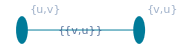
{("∂")_("t")("Γ")^("_")("")_("t")^(""",""v""u")}==-Graphics-

```mathematica
FRG`wetterichEq`FS3;
Cases[(#["body"]/.CM[a__,b_NCM]:>List@@b),HoldPattern[comp[FS`vertex[___],__]]]&/@KeySortBy[FS`propagator`groupBy[Flatten@{%[[2]]/.Plus->List},None],-First[#]&][{4}];
%/.comp[v_FS`vertex,μ__]:>Cases[{μ},HoldPattern[idx[_,_,False]]];
v1=Flatten[#,1]&/@%;

FRG`wetterichEq`FS3;
Cases[(#["body"]/.CM[a__,b_NCM]:>List@@b),HoldPattern[comp[FS`vertex[___],__]]]&/@KeySortBy[FS`propagator`groupBy[Flatten@{%[[2]]/.Plus->List},None],-First[#]&][{3}];
%/.comp[v_FS`vertex,μ__]:>Cases[{μ},HoldPattern[idx[_,_,False]]];
e=#/.{a___,{c_,d_},b___}:>UndirectedEdge[Flatten@{a,c,d,b},Flatten@{a,d,c,b}]&/@%;
eLabel=MapThread[#1->Style[ToString[StandardForm[#2]],Background->White]&,{%,%%}];

Graph[v1,e,VertexSize->Tiny,EdgeShapeFunction->"Line",VertexLabels->"Name"];
VertexCoordinates/.AbsoluteOptions[%,VertexCoordinates];
v1Cords=MapThread[#1->#2&,{v1,%}];

FRG`wetterichEq`FS3;
Cases[(#["body"]/.CM[a__,b_NCM]:>List@@b),HoldPattern[comp[FS`vertex[___],__]]]&/@KeySortBy[FS`propagator`groupBy[Flatten@{%[[2]]/.Plus->List},None],-First[#]&][{2}];
%/.comp[v_FS`vertex,μ__]:>Cases[{μ},HoldPattern[idx[_,_,False]]];
v2=%;
v2Cords=#->Mean[v1Cords[[All,2]]]&/@%;

#->ToString[StandardForm[#]]&/@Join[v1,v2];
Join[Style[#,{EdgeForm[{AbsoluteThickness[0],GUCD`goetheBlau}],GUCD`goetheBlau}]&/@v1,Style[#,{EdgeForm[{AbsoluteThickness[0],GUCD`hellesGruen}],GUCD`hellesGruen}]&/@v2];
FRG`wetterichEq`FS3Graph3D=Graph[%,
	Style[#,GUCD`goetheBlau]&/@e,VertexSize->Small,EdgeShapeFunction->"Line",VertexLabels->%%,
	VertexCoordinates->Join[v1Cords,v2Cords],EdgeLabels->eLabel,ImageSize->300
];
{FRG`wetterichEq`FS3[[1]]/2}==Show[FRG`wetterichEq`FS3Graph3D]//CellPrintDisplayFormulaNumbered

ClearAll[v1,v1Cords,e,eLabel,v2,v2Cords]
```

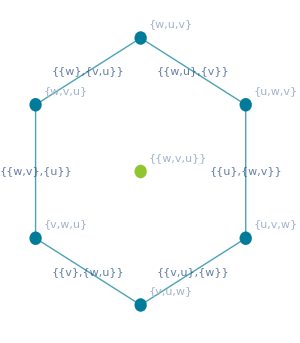
{("∂")_("t")("Γ")^("_")("")_("t")^(""",""w""v""u")}==-Graphics-

```mathematica
FRG`wetterichEq`FS4;
Cases[(#["body"]/.CM[a__,b_NCM]:>List@@b),HoldPattern[comp[FS`vertex[___],__]]]&/@KeySortBy[FS`propagator`groupBy[Flatten@{%[[2]]/.Plus->List},None],-First[#]&][{5}];
%/.comp[v_FS`vertex,μ__]:>Cases[{μ},HoldPattern[idx[_,_,False]]];
v1=Flatten[#,1]&/@%;

FRG`wetterichEq`FS4;
Cases[(#["body"]/.CM[a__,b_NCM]:>List@@b),HoldPattern[comp[FS`vertex[___],__]]]&/@KeySortBy[FS`propagator`groupBy[Flatten@{%[[2]]/.Plus->List},None],-First[#]&][{4}];
%/.comp[v_FS`vertex,μ__]:>Cases[{μ},HoldPattern[idx[_,_,False]]];
e=#/.{a___,{c_,d_},b___}:>UndirectedEdge[Flatten@{a,c,d,b},Flatten@{a,d,c,b}]&/@%;
eLabel=MapThread[#1->Style[ToString[StandardForm[#2]],Background->White]&,{%,%%}];

Graph3D[v1,e,VertexSize->Tiny,EdgeShapeFunction->"DashedLine",VertexLabels->"Name"];
VertexCoordinates/.AbsoluteOptions[%,VertexCoordinates];
v1Cords=MapThread[#1->#2&,{v1,%}];

FRG`wetterichEq`FS4;
Cases[(#["body"]/.CM[a__,b_NCM]:>List@@b),HoldPattern[comp[FS`vertex[___],__]]]&/@KeySortBy[FS`propagator`groupBy[Flatten@{%[[2]]/.Plus->List},None],-First[#]&][{3}];
v2=%/.comp[v_FS`vertex,μ__]:>Cases[{μ},HoldPattern[idx[_,_,False]]];
{#,Flatten[Outer[Join,Permutations[Flatten@{#[[1]]}],Permutations[Flatten@{#[[2]]}],1],1]}&/@%;
v2Cords=#[[1]]->Mean[#[[2]]/.v1Cords]&/@%;

FRG`wetterichEq`FS4;
Cases[(#["body"]/.CM[a__,b_NCM]:>List@@b),HoldPattern[comp[FS`vertex[___],__]]]&/@KeySortBy[FS`propagator`groupBy[Flatten@{%[[2]]/.Plus->List},None],-First[#]&][{2}];
v3=%/.comp[v_FS`vertex,μ__]:>Cases[{μ},HoldPattern[idx[_,_,False]]];
v3Cords=#->Mean[v1Cords[[All,2]]]&/@%;

#->ToString[StandardForm[#]]&/@Join[v1,v2,v3];
Join[Style[#,GUCD`goetheBlau]&/@v1,Style[#,GUCD`hellesGruen]&/@v2,Style[#,GUCD`gruen]&/@v3];
FRG`wetterichEq`FS4Graph3D=Graph3D[%,
	Style[#,GUCD`goetheBlau]&/@e,
	VertexSize->Small,
	EdgeShapeFunction->"Line",
	VertexLabels->%%,
	VertexCoordinates->Join[v1Cords,v2Cords,v3Cords],
	EdgeLabels->eLabel,
	Lighting->{{"Ambient", White}},ImageSize->800
];
{FRG`wetterichEq`FS4[[1]]/2}==Show[FRG`wetterichEq`FS4Graph3D]//CellPrintDisplayFormulaNumbered

ClearAll[v1,v1Cords,e,eLabel,v2,v2Cords,v3,v3Cords]
```

{("∂")_("t")("Γ")^("_")("")_("t")^(""",""x""w""v""u")}==-Graphics3D-

Number of FS diagrams: ordered Bell/Fubini numbers  (= HurwitzLerchPhi[1/2, -n, 0]/2 )

The number of FS diagrams on the r.h.s of the flow equation for ∂_k Γ_k^(n) grow with the order n faster then n!. The number of diagrams is given by the “Number of ways n competitors can rank in a competition, allowing for the possibility of ties” given by the n-th ordered Bell number ( HurwitzLerchPhi[1/2,-n,0]/2 see also [https://en.wikipedia.org/wiki/Ordered_Bell_number] and [https://oeis.org/A000670]). The first few are 1,1,3,13,75,541,4683,47293,545835,7087261,102247563, … .  Computing the flow eqs. in FS becomes extremely expensive/infeasible (with the current implementation) for larger n.

ClearAll[G,Γ,R,d,ncm]
d[exp_,x_,y__]:=Fold[d,exp,{x,y}]
G/:d[G[x_],y_]:=ncm[G[x],Γ[{x,y,x}][3],G[x]]
Γ/:d[Γ[x_List][m_],y_]:=Γ[Join[{x[[1]]},{y},x[[2;;]]]][m+1]

Format[Γ[x_List][m_]]:=Subsuperscript["Γ",Row[x],Row[{"(",m,")"}]]
Format[G[x_]]:=Superscript["G",Row[{x,x}]]
Format[R[x_]]:=Superscript["R",Row[{x,x}]]

R/:d[r_R,x_]:=0
d[ncm[a_,b__],x_]:=ncm[d[a,x],b]+ncm[a,d[ncm[b],x]]
d[Plus[a_,b__],x_]:=d[a,x]+d[Plus[b],x]

Format[ncm[a_,b__]]:=Row[{a,b},VeryThinSpaceString];
ncm[d___,Plus[a_,b__],c___]:=ncm[d,a,c]+ncm[d,Plus[b],c]
ncm[a___,ncm[b__],c___]:=ncm[a,b,c]
ncm[a___,0,b___]:=0
ncm[a_]:=a

exp=ncm[G[m],R[m]];
der={1};
Block[{$RecursionLimit=100000},
For[i=1,i<8,i++,
exp=d[exp,Unique[]];
der=Join[der,{Length@exp}];
];
der[[2]]=1;
]
Row[{Subscript["B","n"]," = ",Row[Flatten@{der,"..."},","]}]//CellPrintDisplayFormulaNumbered[#,"","	[Ordered Bell numbers, https://oeis.org/A000670]"]&

("B")_("n")" = ",","1131375541468347293"..."	[Ordered Bell numbers, https://oeis.org/A000670]

The following equation displays the Number of set compositions (ordered set partitions) of n items into k parts. which is the number of k dimensional ‘faces’ of the n dimensional permutohedron given by the “Triangle of numbers” (  T[n,k]=k!StirlingS2[n,k] [https://oeis.org/A019538]). For further details see e.g. [R. Simion, Convex Polytopes and Enumeration, Adv. in Appl. Math. 18 (1997) pp. 149-180.,  p. 18] and 
[G. M. Ziegler, Lectures on Polytopes, Springer-Verlag, Graduate Texts in Mathematics 152 (1995), p. 168]. In the context of flow eqs. T[n,k] is the number of diagrams with k vertices on the RHS of the flow eq. for the n-point function.

```mathematica
Association@Table[n->Table[k!StirlingS2[n,k],{k,1,n}],{n,1,6}];
KeyValueMap[Join[#2,ConstantArray["",Length[%]-#1],{Total[#2]}]&,%];
tab=%//TableForm[#,TableHeadings->{Array[x↦Row[{"n=",x}],Length[%]],Join[Array[x↦Row[{"k=",x}],Length[%]],{"B_n"}]}]&;

tab//ToString[#,TeXForm]&;
Fold[StringReplace,%,{
	RegularExpression["\\\\text{([^}]*)}"]:>"$1",
	RegularExpression["&([^&\\\\]*)"]:>"& \$$1\$ ",
	RegularExpression["\$([^\$]*)\$"]:>StringReplace["\$$1\$"," "->""],
	RegularExpression["n=(\\d)"]:>"\$n=$1\$","$$"->"\t"
}];
%//CopyToClipboard

tab//CellPrintDisplayFormulaNumbered[#,"","\t[Triangle of numbers, https://oeis.org/A000670]"]&
```

| "k="1 | "k="2 | "k="3 | "k="4 | "k="5 | "k="6 | "B_n"
"n="1 | 1 | "" | "" | "" | "" | "" | 1
"n="2 | 1 | 2 | "" | "" | "" | "" | 3
"n="3 | 1 | 6 | 6 | "" | "" | "" | 13
"n="4 | 1 | 14 | 36 | 24 | "" | "" | 75
"n="5 | 1 | 30 | 150 | 240 | 120 | "" | 541
"n="6 | 1 | 62 | 540 | 1560 | 1800 | 720 | 4683	[Triangle of numbers, https://oeis.org/A000670]

```mathematica
Table[{n,1/2 HurwitzLerchPhi[1/2,-n,0]},{n,0,20}];
Table[{n,n!},{n,0,20}];
p1=ListLogPlot[{%%,%},PlotStyle->{GUCD`goetheBlau,GUCD`emoRot},PlotLegends->Placed[{1/2 HurwitzLerchPhi[1/2,-n,0],n!},{Left,Top}]];

a[n_]:=1/2 HurwitzLerchPhi[1/2,-n,0];
Abs[a[n-1]n/a[n]/Log[2]-1];
Table[{n,%},{n,1,20}];
p2=ListLogPlot[%,PlotStyle->GUCD`gruen,PlotLegends->Placed[{%%},{Left,Bottom}],FrameLabel->{"n"}];

ResourceFunction["PlotGrid"][{{p1},{p2}},ImageSize->200]//CellPrintDisplayFormulaNumbered
```

-Graphics-

```mathematica
CellPrintDisplayFormulaNumbered[
	TraditionalForm[1/2 HurwitzLerchPhi[1/2,-n,0]==(n!)/(2 Log[2]^(n+1))+O[(n-1)!]],"",
	"\t[J.-P. Barthélémy, 1980, An asymptotic equivalent for the number of total preorders on a finite set, Discrete Mathematics, 29 (3): 311–313]"
]
```

1/2 1/2-n0==1/2 n! log^(-n-1)(2)+O(((n-1)!)^1)	[J.-P. Barthélémy, 1980, An asymptotic equivalent for the number of total preorders on a finite set, Discrete Mathematics, 29 (3): 311–313]